Leonid Shifrin

Mathematica programming: an advanced introduction                             < >    Ξ

Edited by Hao Feng

## Section | Functions on lists and functional programming

### Introduction

Functional programming is a programming paradigm in which the central role is played by application of functions, to both data and other functions. Functions themselves are treated as data, and thus can be arguments of other functions. Since any data structure can be represented as a (possibly nested) list, functional programming then is about application of functions to lists.

There are important differences between functional programming in Mathematica and other functional languages (LISP). One difference is that recursion on lists is inefficient in Mathematica since lists are implemented here as arrays rather than linked lists. Another difference is induced by the rule-based nature of Mathematica in the way it reflects itself in function definitions (in the case of pattern-defined functions) and evaluation procedure (global rule base, expression rewriting etc).

Apart from being concise, the functional programming style is usually the most efficient in Mathematica. Also, although we do not consider it in this chapter, in Mathematica it is possible to use functional programming techniques on expressions more general than lists - basically, on general Mathematica expressions. This is a very powerful capability.

A few words about the role of this chapter. Perhaps, it will not be an overestimation to say that this is the most important chapter of all. Mainly, this is because it introduces certain new programming style and a number of programming idioms, which will be heavily used in all later chapters and which together form a different level of programming in Mathematica, not just as technical tricks, but as a new way of thinking about the problems. Those who are familiar with functional programming languages may find some of the material familiar. However even for them, there will be a lot of new information specific to Mathematica, which must be used in order to program it most efficiently.

Examples in this chapter play an important role in the overall exposition of the material. Many of them are used to illustrate some important concepts or subtleties, since I believe that any new idea is best understood when illustrated by a few examples. To get a complete grasp of this chapter, it is recommended to go through all examples, and pay attention to the annotations attached to them. Some of the examples use admittedly rather artificial settings. This is because their primary goal is to illustrate a given language idiom in a rather simple situation.

### Core higher-order functions

#### Introduction

Roughly speaking, functional programming (FP) in Mathematica consists of application of functions to Mathematica normal expressions. A very important special case is when the normal expression is a list (i.e, it’s Head is List), and we will be mostly concerned with this one in this chapter. However, most of what can be done with lists within functional programming paradigm, can also be done with general normal expressions.

Two things make FP non-trivial:

1. Functions can take other functions as their arguments (this has an analog of function pointers in C), but also can create and/or return new functions at run-time, be that pure functions or pattern-based ones. The latter capability has no direct analog in procedural languages, where the functions definitions are determined at compile time.

2. Lists can be made of arbitrary Mathematica expressions, be those atoms (numbers, strings or symbols), or normal expressions. In particular, one may consider nested lists which can be used to implement various data structures (lists, trees etc). This also means that a single list may contain objects of different types.

There are a few characteristic features of the functional programming style which I would like to mention here in order to give a flavor of it. One is that side effects (such as variable assignments) are (almost) absent. Another is that loops are very rarely used if at all. In Mathematica, this is not an absolute restriction however - it is just more natural to use other constructs, as we will see below.

Functions which take other functions as their arguments, are called higher order functions. On the conceptual level, there are just two most important built-in higher order functions in Mathematica - Map and Apply. On the practical level, these two are still most frequently used functions, but some “less fundamental” operations are still needed so often that special built-in functions exist for them, and are also quite
handy.

We will now go through several most often used built-in higher order functions, illustrating their use with examples. Since they serve as building blocks of most of functional programs, one can do quite a lot being equipped with just these functions.

#### Map

This is one of the two most fundamental built-in higher order functions, and by far the most frequently used one. Very roughly, one may say that it is used to replace loops within the FP paradigm.

In it’s simplest form, Map takes two arguments: another function - let us call it <f> - of a single argument (I hasten to comment that the function may have no name, if it is a pure function (see section 4.11)), and an expression - let us call it <expr>, on which this function should by mapped. If <expr> is an atom, it is returned back. If <expr> is a list (or other normal expression), then f is applied to every element of the list, and the resulting list is returned.

Simple examples of use

A few simple examples

```mathematica
Clear[f];
Map[f,a]
```

a

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

In the above, the function <f> did not have any definition yet. Let us define it

```mathematica
f[x_]:=x^2;
```

Now:

```mathematica
Map[f,{a,b,c}]
```

{a^2,b^2,c^2}

```mathematica
Map[f,a]
```

a

Map is a replacement for a loop

Now we can see how it replaces a loop: in a procedural version, we will need something like this

```mathematica
Module[{i,len,expr,newexpr},For[i=1;expr={a,b,c};len=Length[expr];newexpr=Table[0,{len}],i<=len,i++,newexpr[[i]]=f[expr[[i]]]];newexpr]
```

{a^2,b^2,c^2}

Notice that I deliberately packaged the code into a Module, to make variables like <i>, <expr>, etc local and avoid global side effects.

So, even here we can already see what we win by using Map:

1. We don’t need to introduce auxiliary variables
2. We don’t need to know the length of the list beforehand
3. The code is much more concise.
4. It is not obvious at all, but in most cases the code is faster or much faster.

What really happens is that a copy of the original list is created, and then all the operations are performed on the copy. The original list remains unchanged.

Using Map with a pure function

To see how to use a pure function inside Map, let us just reproduce the previous result:

```mathematica
Map[#^2&,{a,b,c}]
```

{a^2,b^2,c^2}

In this case, there is no need for a function name. Also, pure functions (especially when used in Map) may be more efficient that the pattern-defined ones, because no pattern-matching is taking place. But this also means less protection from the bad input, as we discussed before.

Shorthand notation and precedence

As for many common operations, there is a shorthand notation for Map - a symbol /@ (slash-at). The usage is <(function/@expression)>. For example:

```mathematica
(f/@{a,b,c})
```

{a^2,b^2,c^2}

```mathematica
(#^2&/@{a,b,c})
```

{a^2,b^2,c^2}

One may use either literal <Map>, or </@>. Their action is equivalent as long as one always keeps the parentheses as shown above. In many cases, like above, they can be omitted:

```mathematica
f/@{a,b,c}
```

{a^2,b^2,c^2}

```mathematica
#^2&/@{a,b,c}
```

{a^2,b^2,c^2}

In general however they are needed to avoid precedence-related bugs. For instance, in the following example: we want to first map <f> on the list, and then square the result. For the latter part , we use a pure function in the prefix notation (function@expression). What we should get is {a^4,b^4,c^4}. Instead:

```mathematica
#^2&@f/@{a,b,c}
```

{f^2[a],f^2[b],f^2[c]}

What happens is that the function symbol is squared, and only then Mapped. Now:

```mathematica
#^2&@(f/@{a,b,c})
```

{a^4,b^4,c^4}

This sort of problem is impossible with the use of literal Map:

```mathematica
#^2&@Map[f,{a,b,c}]
```

{a^4,b^4,c^4}

Also, literal Map often makes a program easier to read. So my advice would be to use it until you become experienced with it. In practice however, the </@> form is often more handy.

Associativity

Map operation is right-associative, which means that parentheses may be omitted in the following code:

```mathematica
g/@g/@{a,b,c}
```

{g[g[a]],g[g[b]],g[g[c]]}

```mathematica
f/@f/@{a,b,c}
```

{a^4,b^4,c^4}

More examples

Let us now consider a few of the more interesting examples.

Here, by mapping Range on a list produced by another Range, we create a following list of depth 2.

```mathematica
Map[Range,Range[4]]
```

{{1},{1,2},{1,2,3},{1,2,3,4}}

Or equivalently

```mathematica
Range/@Range[4]
```

{{1},{1,2},{1,2,3},{1,2,3,4}}

This will take a list of lists and return a list of their first elements:

```mathematica
Map[First,{{a,b},{c,d},{e,f},{g,h}}]
```

{a,c,e,g}

or

```mathematica
First/@{{a,b},{c,d},{e,f},{g,h}}
```

{a,c,e,g}

This will take a list of lists, and return a list of lists of all subsets of initial lists:

```mathematica
Map[Subsets,{{a,b,c},{d,e}}]
```

{{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}},{{},{d},{e},{d,e}}}

You could have noticed already that all these examples essentially need a single loop which is replaced by Map. While by itself this is not a big deal, the main profit is another layer of abstraction - we no longer need variables and assignments, and thus don’t need to worry about them. For example, a problem of checking the array bounds just does not exist in this approach, without any toll on performance (apart
from that generally induced by Mathematica’s symbolic engine). Another added advantage is that the list of results is produced by Map internally, and thus efficiently, while in a procedural version we have to do it by hand, which is inefficient in Mathematica as we already discussed before.

Mapping a function of several arguments, with all arguments but one fixed

Let us consider another situation: what if we want to Map a function of more than one argument, but where all arguments but one are fixed. For example:

```mathematica
Clear[f,a];
f[x_,y_]:=Sin[x+y];
```

And we want to Map it on a list {1,2,3,4,5}, with the variable <y> fixed at value <a>.

Perhaps the best solution to this problem is obtained by using the built-in <Thread> command. But here, for the sake of example, we will see how we can get it with Map. Later we will return to this example again and show a solution using Thread.

One way is to define an auxiliary function g, as follows:

```mathematica
Clear[g];
Unprotect[g];
g[x_]:=f[x,a];
```

Now we can use Map:

```mathematica
Map[g,Range[5]]
```

{Sin[1+a],Sin[2+a],Sin[3+a],Sin[4+a],Sin[5+a]}

If we need to solve just this problem, the disadvantage of the present solution is that we have to introduce an auxiliary function, which we only need once. If, on the other hand, we want to perform this operation more than once, the disadvantage is that we make a function <g> implicitly depend on the global variable <a> - this is a recipe for disaster. The better solution would be to use a pure function:

```mathematica
Map[f[#,a]&,Range[5]]
```

{Sin[1+a],Sin[2+a],Sin[3+a],Sin[4+a],Sin[5+a]}

We have essentially created a curried function along the lines of section 4.11.1.12. In this case, the function is constructed on the spot, and no name or global definition is associated with it. This may be considered as one of the idioms, which is good to remember. However, keep in mind that in many cases one can use another built-in function Thread (to be covered soon) which is specially designed for this sort of situations and may be faster.

How to prevent Map from mapping on the entire list

I mentioned before that Map in its simplest form is a replacement for a loop. Since it is often useful in procedural approach to exit the loop abnormally with a Break[] command, let us discuss its analog for Map.

In the Mathematica model of computation, the best style of programming consists of operating on any composite object as a whole, and avoid breaking it into pieces, whenever possible. The functionality of Map is in full agreement with this principle - it Maps a given function on an entire list, whatever its length is. If however we want it to stop abnormally, the only way to do it I am aware of is to throw an exception.
However, if the result one is interested in is a resulting list (up to the point where the exception was thrown), then one has to either introduce auxiliary variables, or (much better), use a more sophisticated technique based on Reap-Sow operators (only version 5 onward).The Reap-Sow technique will be covered in detail in part II.

Consider an example: we want to map a function squaring its argument on a list of random numbers, but stop as soon as we encounter first non-positive number, and return the part of a list which has been processed.

Here is a list:

```mathematica
testlist=Table[RandomInteger[{-1,10}],{15}]
```

{4,2,10,9,9,3,4,1,9,4,-1,9,6,5,0}

This will be a solution

```mathematica
Module[{result={}},Catch[Map[If[#>0,AppendTo[result,#^2],Throw[result]]&,testlist]]]
```

{16,4,100,81,81,9,16,1,81,16}

While this solution is not ideal in many ways, and uses some operations (Catch-Throw) not covered yet, my point here is to illustrate 2 things:

1. It is possible to prevent Map from going through an entire list even though Map is a built-in command without such explicit capability (it sweeps through an entire list by default).

2. There is a significant price to pay in doing so. Here, we paid by:
a. Introducing a variable <result> (and then the Module construct to make it local)
b. Making a function to be Mapped more complicated (now it contains an If  statement).
c. <result> is continuously appended in place - this will become inefficient for large lists. For this last point, there are workarounds but they will make the code more complicated.
d. We loose the natural advantage that Map gives us: Map normally produces the resulting list for us. Here we instead create our own resulting list (<result> variable), and inevitably do it inefficiently as compared to a built-in Map. In fact, in this example the use of <Scan> command instead of Map would be more appropriate, but we have not covered it yet.
e. The code is less concise.

So, my suggestion would be to try designing a program such that this kind of interruption of Map is not needed - it is possible to do this in most cases. If there is no other way - then use Throw and Catch as above (avoid however appending large lists in place - there are better techniques of list creation to be discussed later) . In fact, in many cases it may be more efficient to first Map the function on an entire list,
and then pick from that list only certain elements.

Interaction with the procedural code

It is possible to enhance somewhat the functionality of Map by embedding some procedural code (essentially, side effects) inside the function being mapped. One can also view this as continuous run-time redefinitions of the function being mapped. Whatever the interpretation, Mathematica allows for such things, which is often handy. A few examples:

Example: partial sums

This will create a list of partial sums:

```mathematica
Module[{sum=0},sum+=#&/@Range[10]]
```

{1,3,6,10,15,21,28,36,45,55}

or, we can define a function

```mathematica
Clear[partSum];
partSum[x_List]:=Module[{sum=0},sum+=#&/@x];
```

```mathematica
partSum[Range[15]]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120}

Example: simulating MapIndexed

Here we will mimic the action of the MapIndexed function (covered next) in its simplest form (when it is used on a flat list) - it supplies the position of the element in a list as a second argument to the function being mapped on the list.

```mathematica
Clear[f];
Module[{pos=1},f[#,{pos++}]&/@Range[10,20]]
```

{f[10,{1}],f[11,{2}],f[12,{3}],f[13,{4}],f[14,{5}],f[15,{6}],f[16,{7}],f[17,{8}],f[18,{9}],f[19,{10}],f[20,{11}]}

We can again package this as a function:

```mathematica
Clear[myMapIndexed];
myMapIndexed[f_,x_List]:=Module[{pos=1},f[#,{pos++}]&/@x];
```

Example: moving average revisited

We can implement a version of moving average function by constantly updating a “running” list of neighbor points during mapping. Here we Map a function that does it, on a list of first 15 natural numbers, and average each number with 2 neighboring numbers on each side:

```mathematica
Module[{avlist={},result},CompoundExpression[AppendTo[avlist,#];If[Length[avlist]>=5,result=Total[avlist]/5;avlist=Rest[avlist];result]]&/@Range[15]]
```

{Null,Null,Null,Null,3,4,5,6,7,8,9,10,11,12,13}

We have to delete the first 2 m results, since they will be Null. Here is the resulting function:

```mathematica
Clear[movAverage];
movAverage[x_List,m_Integer]/;Length[x]>2m:=Drop[Module[{avlist={},result},CompoundExpression[AppendTo[avlist,#];If[Length[avlist]>=2m+1,result=Total[avlist]/(2m+1);avlist=Rest[avlist];result]]&/@x],2m];
```

Check:

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
movAverage[Range[10]^2,1]
```

{14/3,29/3,50/3,77/3,110/3,149/3,194/3,245/3}

This is another implementation where the idea of using side effects is pushed to the extreme:

```mathematica
Clear[movAverageAlt];
movAverageAlt[x_List,m_Integer]/;Length[x]>2m:=Module[{n=1},Total[Tak[x,{n,2m+n++}]]/(2m+1)&/@Drop[x,2m]];
```

Notice that here, it does not use any information from the list on which the function is mapped - this is a pure function with zero arguments (see section 4.11.1.11), so we could just as well map on a list of zeros or ones - it just needs to have the right length. C programmers may worry about the line {n,2m+n++}, since its value depends on which part of the list is evaluated first. But here this is system-independent, since the standard evaluation procedure applied to a simple flat list prescribes that the parts of such list will always be evaluated from left to right.

We can do some efficiency tests

```mathematica
movAverage[Range[10000],10];//Timing
```

{0.058052,Null}

```mathematica
movAverageAlt[Range[10000],10];//Timing
```

{0.030136,Null}

We notice that the second version is about twice faster. Let me mention that these implementations are not very efficient, and the purpose of this example was to demonstrate the construction used here.

This is one of the most efficient implementations, which we covered before in section 3.8.1.2, for comparison:

```mathematica
Clear[movingAverage];
movingAverage[x_List,m_Integer]:=(Plus@@#)/Length[#]&@Partition[x,Length[x]-2*m,1];
```

```mathematica
movingAverage[Range[10000],10];//Timing
```

{0.01594,Null}

Normally, you don’ t get a big penalty in efficiency if you use just one or two global variables for side effects inside the mapped function. But manipulations with entire lists, like those done above, are costly and should be avoided.

More general uses of Map - Mapping on a certain level in an expression

As a third optional argument, Map takes a level specification. This is the standard level specification (see section 1.1.7) used in many Mathematica constructs - here it indicates the level(s) on which the function should be mapped. Let me remind that a single integer gives the level up to which the function should be mapped, integer in parentheses means that mapping should affect only that level, and a pair of integers in
parentheses indicate a range of levels affected by mapping.

Initial examples

```mathematica
Clear[f,testexpr];
```

This is our initial list

```mathematica
testexpr=Outer[List,Range[2],Range[3]]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}}}

First, let us use simple Map:

```mathematica
Map[f,testexpr]
```

{f[{{1,1},{1,2},{1,3}}],f[{{2,1},{2,2},{2,3}}]}

The way to think about Map-ping on higher levels is that we effectively “sneak” through some number of curly braces, and then Map.

Now we Map on levels 1 and 2:

```mathematica
Map[f,testexpr,2]
```

{f[{f[{1,1}],f[{1,2}],f[{1,3}]}],f[{f[{2,1}],f[{2,2}],f[{2,3}]}]}

The same can be achieved by

```mathematica
Map[f,testexpr,{1,2}]
```

{f[{f[{1,1}],f[{1,2}],f[{1,3}]}],f[{f[{2,1}],f[{2,2}],f[{2,3}]}]}

Now we Map on levels 2 and 3:

```mathematica
Map[f,testexpr,{2,3}]
```

{{f[{f[1],f[1]}],f[{f[1],f[2]}],f[{f[1],f[3]}]},{f[{f[2],f[1]}],f[{f[2],f[2]}],f[{f[2],f[3]}]}}

Now only on level 3:

```mathematica
Map[f,testexpr,{3}]
```

{{{f[1],f[1]},{f[1],f[2]},{f[1],f[3]}},{{f[2],f[1]},{f[2],f[2]},{f[2],f[3]}}}

Negative levels can also be used. In this case negative 1 is equivalent to 3:

```mathematica
Map[f,testexpr,{-1}]
```

{{{f[1],f[1]},{f[1],f[2]},{f[1],f[3]}},{{f[2],f[1]},{f[2],f[2]},{f[2],f[3]}}}

Be aware however that for general expressions (trees, for example), there is no simple connection between negative and positive level specifications. Specification {-n} means “all sub-expressions of depth n”, while {n} means all elements at the level <n>. Negative level specifications may look exotic, but in practice they are often quite useful. One particular example where Map-ping on negative levels is useful is
when one has to grow some tree in a breadth-first manner.

Specification <-n> without parentheses means “all subexpressions of depth at least n”. For example,

```mathematica
Map[f,testexpr,-1]
```

{f[{f[{f[1],f[1]}],f[{f[1],f[2]}],f[{f[1],f[3]}]}],f[{f[{f[2],f[1]}],f[{f[2],f[2]}],f[{f[2],f[3]}]}]}

```mathematica
Map[f,testexpr,-2]
```

{f[{f[{1,1}],f[{1,2}],f[{1,3}]}],f[{f[{2,1}],f[{2,2}],f[{2,3}]}]}

```mathematica
Map[f,testexpr,-3]
```

{f[{{1,1},{1,2},{1,3}}],f[{{2,1},{2,2},{2,3}}]}

Once again, for nested lists with the same dimensions of the sublists, we see the connection to positive level specification, because on each level all elements have the same depth. In general, there is no such connection.

Less trivial example - using Map to sort sublists in a nested list

Create a list (table) of depth 4, of random numbers

```mathematica
Clear[testexpr];
testexpr=Table[RandomInteger[{1,10}],{3},{2},{3}]
```

{{{9,1,2},{1,7,6}},{{7,6,4},{2,7,10}},{{7,10,1},{9,7,7}}}

Now say we need to sort the sublists of numbers. The way to do it is to Map the Sort function on the level {2}:

```mathematica
Map[Sort,testexpr,{2}]
```

{{{1,2,9},{1,6,7}},{{4,6,7},{2,7,10}},{{1,7,10},{7,7,9}}}

If we want to sort in decreasing order, then:

```mathematica
Map[Sort[#,#1>=#2&]&,testexpr,{2}]
```

{{{9,2,1},{7,6,1}},{{7,6,4},{10,7,2}},{{10,7,1},{9,7,7}}}

This example is a little tricky and requires some explanation: the point is that Sort itself is a higher order function, which takes as a second optional argument the sorting criteria function. The criteria function depends on 2 variables, and in this case is <#1≥ #2&>. There is no confusion between the first argument of Sort # and the argument #1 from the criteria function, because the latter is completely contained in the former. To clarify this, let us do the same thing without the use of pure functions:

```mathematica
Clear[sortF,critF];
critF[x_,y_]:=x>=y;
sortF[x_List]:=Sort[x,critF];
```

Now we can Map sortF instead of Sort

```mathematica
Map[sortF,testexpr,{2}]
```

{{{9,2,1},{7,6,1}},{{7,6,4},{10,7,2}},{{10,7,1},{9,7,7}}}

The price to pay here is that two auxiliary functions have to be introduced and given names. As it happens, we can use a built-in function GreaterEqual, instead of critF:

```mathematica
result=Map[Sort[#,GreaterEqual]&,testexpr,{2}]
```

{{{9,2,1},{7,6,1}},{{7,6,4},{10,7,2}},{{10,7,1},{9,7,7}}}

The previous two solutions were presented to show how to do things in the general case, when no built-in criteria function is available. However, whenever the built-in function is available, it is always better to use a built-in.

As a next step in this example, imagine that the sublists also have to be sorted, according to which sublist has a smaller first element. For example, sorting the list {{3,1},{5,6,7},{2,8},{4,6}} should give {{2,8},{3,1},{4,6},{5,6,7}}. The proper (pure) criteria function will be in this case #1[[1]]£ #2[[1]]&, and we have to Map Sort on the first level now

```mathematica
result1=Map[Sort[#,#1[[1]]<=#2[[1]]&]&,result]
```

{{{7,6,1},{9,2,1}},{{7,6,4},{10,7,2}},{{9,7,7},{10,7,1}}}

Finally, we may want to reorder the largest sublists, according for instance to a total sum of the numbers contained.

A sub-problem: sum all the numbers contained in a nested list

For example, in the first sublist:

```mathematica
sublist=result1[[1]]
```

{{7,6,1},{9,2,1}}

The best way to sum all the numbers here is to first use Flatten, to remove internal curly braces and make a list flat. Then use Total on the resulting list:

```mathematica
numsum=Total[Flatten[sublist]]
```

26

Now that we know how to sum all the numbers, we can convert this knowledge into a pure function (sorting criteria): Total[Flatten[#1-#2]]≥ 0& (here we use that the sublists have the same structure and can thus be subtracted)

```mathematica
result2=Sort[result1,Total[Flatten[#1-#2]]>=0&]
```

{{{9,7,7},{10,7,1}},{{7,6,4},{10,7,2}},{{7,6,1},{9,2,1}}}

Notice that in this case there is no Map-ping, since we already operate on the level where we should just simply use Sort.

Let me summarize the goal and the code once again: we are given a list of depth 4 of numbers (think of it as a 3-dimensional grid), which we want to sort according to the following rules: the numbers inside the smallest sublists are sorted in decreasing order. The smallest sublists inside next smallest are sorted such that the sublist with the smallest first element comes first. Finally, the largest sublists are sorted by decreasing total of all the elements in the sublist. The sorting has to be performed starting with the smallest sublists (although in this particular example, the order is irrelevant). Here is the code packaged into a function (variables made local):

```mathematica
Clear[sortNested];
sortNested[x_List]:=Module[{result,result1,result2},result=Map[Sort[#,GreaterEqual]&,x,{2}];result1=Map[Sort[#,#1[[1]]<=#2[[1]]&]&,result];result2=Sort[result1,Total[Flatten[#1-#2]]>0&]]
```

Check:

```mathematica
sortNested[testexpr]
```

{{{9,7,7},{10,7,1}},{{7,6,4},{10,7,2}},{{7,6,1},{9,2,1}}}

Notice that we could have avoided the introduction of auxiliary variables by nesting the code, but then it would become much less readable:

```mathematica
Clear[sortNestedAlt];
sortNestedAlt[x_List]:=Sort[Map[Sort[#,#1[[1]]<=#2[[1]]&]&,Map[Sort[#,GreaterEqual]&,x,{2}]],Total[Flatten[#1-#2]]>=0&];
```

```mathematica
sortNestedAlt[testexpr]
```

{{{9,7,7},{10,7,1}},{{7,6,4},{10,7,2}},{{7,6,1},{9,2,1}}}

The lesson here is that often the advantage of readability over weights extra code needed. Try to resist a temptation of writing deeply nested functions like <sortNestedAlt>.

A general feature illustrated by this example is that pure functions, Map and a possibility to use higher-order functions greatly reduce the size of the code, and increase its flexibility. Also, in Mathematica this way of doing it will be among the most efficient ones.

Many more examples of Map in action will follow - Map is truly ubiquitous in Mathematica programming.

#### MapAt

If Map can be thought of as a machine gun, then MapAt is a precision rifle. It Maps the function to specific position(s) rather than on an entire list.

In the simplest form, MapAt takes 3 arguments: the function to be mapped, the expression, and the position of the element of this expression on which to map. For mapping on the first-level elements of the list, the position can be just the index of the element - a number. In general, the position has to be a list of indices. MapAt uses the same position specifications as Position and Extract. One can also use MapAt to map a function on several elements at once - in this case, a list of positions of these elements, rather than a single position, has to be supplied. The elements corresponding to these positions, may be at different levels in the expression. Thus, sublists representing elements’ positions can have different lengths.

Examples

```mathematica
Clear[ourlist];
ourlist={a,b,c,d}
```

{a,b,c,d}

Say, we want to Map Sine function on the second element:

```mathematica
MapAt[Sin,ourlist,2]
```

{a,Sin[b],c,d}

If we want to Map on second and third elements:

```mathematica
MapAt[Sin,ourlist,{{2},{3}}]
```

{a,Sin[b],Sin[c],d}

Notice the internal curly braces. If we omit them, Mathematica will decide that we want to Map Sine on a single element with the position {2,3}. Since there is no such element ({2,3} means third element of the second element, but the second element is an atom), this will result in an error.

```mathematica
MapAt[Sin,ourlist,{2,3}]
```

MapAt::partw: Part {2,3} of {a,b,c,d} does not exist.

MapAt[Sin,{a,b,c,d},{2,3}]

Let us now create a nested list:

```mathematica
Clear[testexpr,f];
testexpr=Table[RandomInteger[{1,10}],{3},{2},{3}]
```

{{{6,6,10},{1,1,7}},{{6,5,7},{6,5,3}},{{4,4,5},{1,3,7}}}

It is useful to consider a few examples and try to understand why each output is as it is:

```mathematica
MapAt[f,testexpr,2]
```

{{{6,6,10},{1,1,7}},f[{{6,5,7},{6,5,3}}],{{4,4,5},{1,3,7}}}

```mathematica
MapAt[f,testexpr,{{2},{3}}]
```

{{{6,6,10},{1,1,7}},f[{{6,5,7},{6,5,3}}],f[{{4,4,5},{1,3,7}}]}

```mathematica
MapAt[f,testexpr,{3,2}]
```

{{{6,6,10},{1,1,7}},{{6,5,7},{6,5,3}},{{4,4,5},f[{1,3,7}]}}

```mathematica
MapAt[f,testexpr,{{2,1},{3,2}}]
```

{{{6,6,10},{1,1,7}},{f[{6,5,7}],{6,5,3}},{{4,4,5},f[{1,3,7}]}}

```mathematica
MapAt[f,testexpr,{{2,1,1},{3,2,3}}]
```

{{{6,6,10},{1,1,7}},{{f[6],5,7},{6,5,3}},{{4,4,5},{1,3,f[7]}}}

Basically, all you have to do to unravel the above examples is to carefully trace the position: for example, {2,1,1} means: first element of the first element of the second element.

Use in conjunction with Map

MapAt is often used in conjunction with Map. For example, we want to Map <f> on the second element (number) in each small sublist. The code is

```mathematica
Map[MapAt[f,#,2]&,testexpr,{2}]
```

{{{6,f[6],10},{1,f[1],7}},{{6,f[5],7},{6,f[5],3}},{{4,f[4],5},{1,f[3],7}}}

To convince yourself that we needed to Map on the level {2}, think this way: we had to bypass 2 external curly braces to use MapAt on the first sublist. Should we Map on the first level instead, we’ d get the following:

```mathematica
Map[MapAt[f,#,2]&,testexpr]
```

{{{6,6,10},f[{1,1,7}]},{{6,5,7},f[{6,5,3}]},{{4,4,5},f[{1,3,7}]}}

which is not what we want (do you see what happened and why?).Notice that we created the pure function out of MapAt along the lines of section 4.11.1.12.

Use in conjunction with Position

Also, MapAt is often used in conjunction with Position. The logic is this: say, we want to Map certain function f on all elements of a given expression(possibly restricted to some levels), satisfying certain criteria. This can be easily done in a rule-based approach. In FP approach, we use Position to find positions of all such elements, and then plug the result into MapAt.

As an example, say we want to Map f on all even numbers in our list. The code is

```mathematica
MapAt[f,testexpr,Position[testexpr,_?EvenQ]]
```

{{{f[6],f[6],f[10]},{1,1,7}},{{f[6],5,7},{f[6],5,3}},{{f[4],f[4],5},{1,3,7}}}

Or, on all multiples of 3

```mathematica
MapAt[f,testexpr,Position[testexpr,x_/;Mod[x,3]==0]]
```

{{{f[6],f[6],10},{1,1,7}},{{f[6],5,7},{f[6],5,f[3]}},{{4,4,5},{1,f[3],7}}}

Warning: performance pitfall

However, be aware of the performance pitfall associated with this technique: when you try to use MapAt to map a function on a large number of elements at the same time (especially if all of them belong to a single subexpression), MapAt can be very slow. Please see Appendix C for a detailed discussion. In some cases, the performance of MapAt may be improved (or, rather, a more efficient implementation with a basic MapAt functionality can be found) - see chapter VI for such an example.

Application: multiple random walks

We can use MapAt to implement co-evolving random walkers, for instance. Let us say that each walker is updated with the same function, say

```mathematica
Clear[randomWalk];
randomWalk[x_]:=x+RandomInteger[{-1,1}];
```

Let us say we have n = 5 random walkers, all starting at zero:

```mathematica
nwalkers=5;
startpositions=Table[0,{nwalkers}]
```

{0,0,0,0,0}

We may either update them one by one, or in principle, update them at random. In the latter case, we will generate an “update” list of numbers from 1 to n. Each number <k> means “update walker k”.

```mathematica
totalupdates=50;
updatelist=Table[RandomInteger[{1,nwalkers}],{totalupdates}]
```

{4,2,5,5,2,5,1,5,5,3,2,3,1,1,1,1,3,1,4,4,3,4,4,2,1,5,3,2,2,2,3,3,5,2,5,4,4,4,4,4,4,2,3,4,2,5,1,4,3,4}

This gives the total evolution of all the walkers (FoldList will be covered shortly):

```mathematica
Short[result=FoldList[MapAt[randomWalk,#1,#2]&,startpositions,updatelist],10]
```

{{0,0,0,0,0},{0,0,0,-1,0},{0,1,0,-1,0},{0,1,0,-1,-1},{0,1,0,-1,0},{0,0,0,-1,0},{0,0,0,-1,1},{1,0,0,-1,1},{1,0,0,-1,1},{1,0,0,-1,2},«32»,{-3,2,-3,-4,1},{-3,2,-4,-4,1},{-3,2,-4,-5,1},{-3,2,-4,-5,1},{-3,2,-4,-5,1},{-4,2,-4,-5,1},{-4,2,-4,-5,1},{-4,2,-5,-5,1},{-4,2,-5,-4,1}}

To get individual walker’ s trajectories, we may Transpose the result.

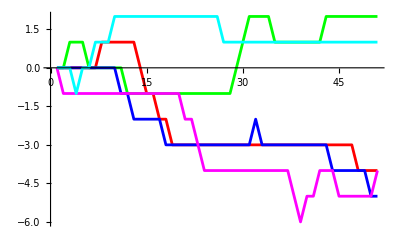

```mathematica
ListPlot[Transpose[result],Joined->True,PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,0,1],RGBColor[0,1,1]}]
```

Identical positions in the position list

When some of the positions in the position list in MapAt coincide, the function is mapped on that position several times (nested). For instance:

```mathematica
Clear[g];
MapAt[g,Range[5],{{1},{2},{4},{2},{4},{4}}]
```

{g[1],g[g[2]],3,g[g[g[4]]],5}

However, the order in which the function is mapped in this case does not correspond to the order of positions in the list of positions. The nested function calls which correspond to the duplicate positions in the position list, are grouped together before the function is evaluated. We can see that by introducing a side-effect - the counter n, and trace whether the counter values correspond to the order in which mapping positions follow - they don’ t.

```mathematica
MapAt[g[#,n++]&,n=0;Range[5],{{1},{2},{4},{2},{4},{4}}]
```

{g[1,0],g[g[2,1],2],3,g[g[g[4,3],4],5],5}

This means, in particular, that in the previous example with random walkers we won’t be able to obtain the final state of the walkers by just feeding the list of update positions to MapAt, because it would apply the random <randomWalk> function to the walkers in different order.

The order of mapping

Whenever MapAt is used to map a function to a number of elements, we already saw that MapAt does not map in the same order in which we supply the positions of the element. But what is the order in which mapping happens? The answer is that the list of positions is first reordered such that they follow as they would in a depth - first expression traversal. The reason is probably that this is the only order which is unambiguous, given that the function being mapped may in principle do any transformation with the subexpression (sub-branch) on which it is mapped, even destroy it.

Example: imitating DeleteCases

One important specific case is when we want to actually delete elements subject to some criteria. Usually, we use DeleteCases for that. For example, let us delete from all sublists of a nested list all elements that are multiples of 3. This will be our test list:

```mathematica
Clear[testexpr];
testexpr=Table[RandomInteger[{1,10}],{3},{2},{3}]
```

{{{8,10,3},{4,5,8}},{{7,6,1},{10,5,2}},{{10,6,8},{2,10,8}}}

We can imitate DeleteCases by Mapping a function #/.#:-> Sequence[]&, which effectively deletes an element from the list by replacing it by an “emptiness” (if you are feeling ambitious, try to see why we did not use a simpler form for the function being mapped - just Sequence[]&).

```mathematica
MapAt[#/.#:>Sequence[]&,testexpr,Position[testexpr,x_/;Mod[x,3]==0]]
```

{{{8,10},{4,5,8}},{{7,1},{10,5,2}},{{10,8},{2,10,8}}}

We can package this into a function:

```mathematica
Clear[myDeleteCases];
myDeleteCases[expr_,patt_]:=MapAt[#/.#:>Sequence[]&,expr,Position[expr,patt]];
```

Check again:

```mathematica
myDeleteCases[testexpr,x_/;Mod[x,3]==0]
```

{{{8,10},{4,5,8}},{{7,1},{10,5,2}},{{10,8},{2,10,8}}}

With DeleteCases, it will look like (Infinity means look at all levels)

```mathematica
DeleteCases[testexpr,x_/;Mod[x,3]==0,Infinity]
```

{{{8,10},{4,5,8}},{{7,1},{10,5,2}},{{10,8},{2,10,8}}}

#### MapAll

This function is equivalent to Map[function,expression,{0,Infinity}]. The zero here is necessary to apply the function also to entire expression, since this is what MapAll also does. We give just a single example

```mathematica
Clear[testexpr,f];
testexpr=Table[RandomInteger[{1,10}],{3},{2},{3}]
```

{{{5,3,2},{6,7,6}},{{3,9,6},{1,1,6}},{{1,8,7},{7,5,5}}}

```mathematica
MapAll[f,testexpr]
```

f[{f[{f[{f[5],f[3],f[2]}],f[{f[6],f[7],f[6]}]}],f[{f[{f[3],f[9],f[6]}],f[{f[1],f[1],f[6]}]}],f[{f[{f[1],f[8],f[7]}],f[{f[7],f[5],f[5]}]}]}]

MapAll works in a depth-first manner

As is easy to demonstrate, MapAll performs the mapping on a general Mathematica expression (which, as we recall, can always be represented as a tree), in a depth-first manner. To do this, consider the following nested list (Fold operation will be covered shortly):

```mathematica
tst=Fold[List,{},{a,b,c,d}]
```

{{{{{},a},b},c},d}

This function prints the value of its argument and then returns the argument.

```mathematica
ShowIt[x_]:=(Print[x];x)
```

Let us now map it to all levels of our expression:

```mathematica
MapAll[ShowIt,tst]
```

{}

a

{{},a}

b

{{{},a},b}

c

{{{{},a},b},c}

d

{{{{{},a},b},c},d}

{{{{{},a},b},c},d}

This clearly demonstrates that Mapping is performed in a depth-first manner. In general, MapAll should be used anytime when some function has to be applied to all levels of expression and in the depth-first manner (or when the order in which the function is applied to different pieces of expression does not matter). One example of such use follows.

Use in conjunction with ReplaceAll

MapAll is not very often used, but there is however at least one instance when it is very useful - in conjunction with rule application when rules have to be applied to the innermost parts of the expression first. This is not what happens by default. Consider the following rule:

```mathematica
ourrule={x_,y_}:>{x,y^2};
```

Now, let us try:

```mathematica
tst/.ourrule
```

{{{{{},a},b},c},d^2}

```mathematica
tst/.ourrule/.ourrule
```

{{{{{},a},b},c},d^4}

We see that the rule is always being applied to the outermost expression, since it matches. One way to proceed is of course to restrict the rule, so that, once applied, it won’t apply to the transformed expression any more:

```mathematica
ournewrule={x_,y_/;Not[MatchQ[y,Power[_,2]]]}:>{x,y^2};
```

```mathematica
tst/.ournewrule
```

{{{{{},a},b},c},d^2}

```mathematica
tst/.ournewrule/.ournewrule
```

{{{{{},a},b},c^2},d^2}

```mathematica
tst//.ournewrule
```

{{{{{},a^2},b^2},c^2},d^2}

In the above case, we had our rule applied to expression starting from the outermost level to the innermost. But this behavior is not always the desired one. We can use MapAll to change this: now we will do the same by starting from the innermost piece, since MapAll maps the function in a depth-first manner. We can monitor this by tracing the execution (we restrict the Trace command to show only the rule-substitution pieces of the evaluation tree)

```mathematica
Trace[MapAll[#/.ourrule&,tst],ReplaceAll]
```

{{{{{{{{{{}/.ourrule,{}/.{x_,y_}:>{x,y^2},{}},{a/.ourrule,a/.{x_,y_}:>{x,y^2},a}},{{},a}/.ourrule,{{},a}/.{x_,y_}:>{x,y^2},{{},a^2}},{b/.ourrule,b/.{x_,y_}:>{x,y^2},b}},{{{},a^2},b}/.ourrule,{{{},a^2},b}/.{x_,y_}:>{x,y^2},{{{},a^2},b^2}},{c/.ourrule,c/.{x_,y_}:>{x,y^2},c}},{{{{},a^2},b^2},c}/.ourrule,{{{{},a^2},b^2},c}/.{x_,y_}:>{x,y^2},{{{{},a^2},b^2},c^2}},{d/.ourrule,d/.{x_,y_}:>{x,y^2},d}},{{{{{},a^2},b^2},c^2},d}/.ourrule,{{{{{},a^2},b^2},c^2},d}/.{x_,y_}:>{x,y^2},{{{{{},a^2},b^2},c^2},d^2}}

A digression: performance improvements and the use of With

Trace also reveals that our computation is not entirely efficient since the rule definition is evaluated every time afresh. To avoid this we will use <With> to embed the rule definition textually:

```mathematica
Trace[With[{rule=ourrule},MapAll[#/.rule&,tst]],ReplaceAll]
```

{{{{{{{{{{}/.{x_,y_}:>{x,y^2},{}},{a/.{x_,y_}:>{x,y^2},a}},{{},a}/.{x_,y_}:>{x,y^2},{{},a^2}},{b/.{x_,y_}:>{x,y^2},b}},{{{},a^2},b}/.{x_,y_}:>{x,y^2},{{{},a^2},b^2}},{c/.{x_,y_}:>{x,y^2},c}},{{{{},a^2},b^2},c}/.{x_,y_}:>{x,y^2},{{{{},a^2},b^2},c^2}},{d/.{x_,y_}:>{x,y^2},d}},{{{{{},a^2},b^2},c^2},d}/.{x_,y_}:>{x,y^2},{{{{{},a^2},b^2},c^2},d^2}}

Note that the use of Module or Block won’ t have the same effect, and won’ t help us here.

The same functionality can be achieved by using Replace rather than ReplaceAll, with the level specification {0, Infinity}:

```mathematica
Trace[Replace[tst,ourrule,{0,Infinity}]]
```

{{tst,{{{{{},a},b},c},d}},{ourrule,{x_,y_}:>{x,y^2}},{{∞,∞},{0,∞}},Replace[{{{{{},a},b},c},d},{x_,y_}:>{x,y^2},{0,∞}],{{{{{},a^2},b^2},c^2},d^2}}

This is in fact a more efficient solution since more operations are done inside the kernel, but without the previous discussion the apparent differences in the functionality of ReplaceAll[expr, rules] and Replace[expr, rules, {0, Infinity}] may look like a mystery. In many cases the desired behavior is in fact the one of the latter operation - that is, apply rules to the innermost expressions first.

Also, even in the case above, the use of the construct MapAll[#/.rules&,expr] may be advantageous since, being essentially equivalent to Replace[expr, rules, {0, Infinity}], it allows for a more detailed tracing and debugging. Once the code is tested (and possibly debugged), one can change it back to Replace[expr, rules, {0, Infinity}].

Finally, it could be necessary that the rules at each level be repeatedly applied until the expression stops changing. This is achieved by  MapAll[ReplaceRepeated[#, rules]&, expr], but to my knowledge there is no simple equivalent with Replace in this case.

#### Scan

Scan is a function similar to Map, but it does not return a list of values at the end. This means that using Scan only makes sense if the function being scanned contains side effects such as assignments. The format is:

```mathematica
Scan[f,expr,levspec]
```

where <f> is the function being scanned, <expr> is an expression on which we scan the function <f>, and <levspec> is an optional level specification - the syntax is very similar to that for Map.

Simple examples

Let us, for example, scan a squaring function on a list:

```mathematica
Scan[#^2&,Range[10]]
```

We can see that no output has been produced (or, more precisely, Null has been produced). To get anything useful, we need some side effects. Here, for instance, we will use Scan to compute the sum of squares of the list elements:

```mathematica
Module[{sumsq=0},Scan[sumsq+=#^2&,Range[10]];sumsq]
```

385

Since Scan does not produce a list of results, it is somewhat faster than Map. However, there is another and perhaps more important difference between the two: Scan can be “stopped” at any moment by using a Return statement inside a function being scanned. This is not true for Map - it can be stopped only by throwing an exception. For example, we want to compute the sum of the squares but stop as the element exceeds 6:

```mathematica
Module[{sumsq=0},Scan[If[#<=6,sumsq+=#^2,Return[sumsq]]&,Range[10]]]
```

91

The Return statement will break only from Scan, but not from any scoping construct possibly enclosing Scan, such as Module above.

Example: conditional list splitting

Scan can also be thought of as a replacement for loops. Here, for example, we will use it to determine the position where to split a given list in 2 parts (this will happen as soon as the condition <cond> will first be satisfied).

```mathematica
Clear[splitWhen];
splitWhen[x_List,cond_]:=Module[{n=0},Scan[If[cond[#],Return[],n++]&,x];{Take[x,n],Drop[x,n]}]
```

Scan is a better device than just a single loop (or nested loops in most cases, for that matter), both because it is optimized and because it is more general: it receives the standard level specification and works on general symbolic trees (Mathematica expressions), not just simple lists . In particular, if asked, it traverses an expression depth-first, computing whatever side effects we instruct it to.

#### MapIndexed

This is a truly useful function, which extends in some sense the capabilities of Map. There are situations in which on one hand, a function like Map is needed, but on the other hand, which Map can not handle. These are cases when the function being mapped has to “know” where in the list it is “currently”. Let us consider an example.

Starting example and syntax

Say, we have a simple list of numbers:

```mathematica
testlist=Table[RandomInteger[{0,10}],{15}]
```

{8,0,7,2,2,0,7,3,0,3,7,5,5,0,2}

Now, say, we would like to Map on it a function (-1)^n*Sin[x], where <n> is a position of the number, and <x> is a number. In this simple case we could use Map like this:

```mathematica
Module[{n=0},Map[(-1)^(n++)Sin[#]&,testlist]]
```

{Sin[8],0,Sin[7],-Sin[2],Sin[2],0,Sin[7],-Sin[3],0,-Sin[3],Sin[7],-Sin[5],Sin[5],0,Sin[2]}

However, this is not an aesthetic solution. Also, it will not work for more complicated lists. What MapIndexed does is to provide to a function being mapped the position of the current element as a second argument. So, now the function being mapped is a function of two arguments. The rest of the syntax is the same:

```mathematica
MapIndexed[function, expression, level]
```

As before, the level specification is an optional parameter - it is 1 by default. In this particular example, we write

```mathematica
MapIndexed[(-1)^#2[[1]]*Sin[#1]&,testlist]
```

{-Sin[8],0,-Sin[7],Sin[2],-Sin[2],0,-Sin[7],Sin[3],0,Sin[3],-Sin[7],Sin[5],-Sin[5],0,-Sin[2]}

Notice that we again use here a pure function, but this time a pure function of the two arguments. Notice also that we take a first part of the second argument #2[[1]]: this is because the position is always given as a list of indexes, even for a simple list.

In principle, once again, we can use a pattern-defined function of two arguments here:

```mathematica
Clear[g];
g[x_,{n_Integer}]:=(-1)^n*Sin[x];
MapIndexed[g,testlist]
```

{-Sin[8],0,-Sin[7],Sin[2],-Sin[2],0,-Sin[7],Sin[3],0,Sin[3],-Sin[7],Sin[5],-Sin[5],0,-Sin[2]}

Another simple example: let us supply the numbers in the list with their positions

```mathematica
MapIndexed[List,testlist]
```

{{8,{1}},{0,{2}},{7,{3}},{2,{4}},{2,{5}},{0,{6}},{7,{7}},{3,{8}},{0,{9}},{3,{10}},{7,{11}},{5,{12}},{5,{13}},{0,{14}},{2,{15}}}

More examples

Example: creation of specific matrices

MapIndexed gets more non-trivial in what can be accomplished with it, as we go to nested lists and trees. For example, let us build a matrix (list of lists), with elements Sin[i-j], where i and j are column and row numbers (say,4x4)

```mathematica
(result=MapIndexed[Sin[#2[[1]]-#2[[2]]]&,IdentityMatrix[4],{2}])//MatrixForm
```

(0 | -Sin[1] | -Sin[2] | -Sin[3]
Sin[1] | 0 | -Sin[1] | -Sin[2]
Sin[2] | Sin[1] | 0 | -Sin[1]
Sin[3] | Sin[2] | Sin[1] | 0)

Notice that here we Map on the level {2}, which corresponds to numbers. Also, then, the argument #2 is now a position of the matrix element and has 2 indices (i and j). It is really easy to verify that - create a matrix where the elements will be just positions:

```mathematica
MapIndexed[#2&,IdentityMatrix[4],{2}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}}}

Now let us say we want to Map a value <a> on the two diagonals above and below the main diagonal. Here is the code:

```mathematica
(result1=MapIndexed[If[Abs[#2[[1]]-#2[[2]]]==1,a,#1]&,result,{2}])//MatrixForm
```

(0 | a | -Sin[2] | -Sin[3]
a | 0 | a | -Sin[2]
Sin[2] | a | 0 | a
Sin[3] | Sin[2] | a | 0)

Not that in this particular case, MapIndexed-based solution is not very efficient, since since the majority of matrix element tested by MapIndexed were a priori known not to be on the diagonals of interest. Later in this chapter we will give a more efficient solution based on MapThread function.

Note also that in principle this example can be generalized to create any matrix we want. All we need is to define a function which will compute a matrix element given its position in the matrix. This function will then be used by MapIndexed. Also, note that we had to start with some matrix (here we used IdentityMatrix).

Example: creation and manipulation of matrices of functions

We can do more interesting things. In particular, we can construct a matrix where all elements will be functions:

```mathematica
(result3=MapIndexed[x^Total[#2]&,IdentityMatrix[3],{2}])//MatrixForm
```

(x^2 | x^3 | x^4
x^3 | x^4 | x^5
x^4 | x^5 | x^6)

We may compute the determinant symbolically:

```mathematica
Det[result3]
```

0

We can , say, differentiate the off-diagonal elements and integrate the diagonal elements:

```mathematica
(result4=MapIndexed[Simplify[If[#2[[1]]==#2[[2]],Integrate[#1,x],D[#1,x]]]&,result3,{2}])//MatrixForm
```

(x^3/3 | 3 x^2 | 4 x^3
3 x^2 | x^5/5 | 5 x^4
4 x^3 | 5 x^4 | x^7/7)

Example: imitating the Position command

One can imitate the Position operation with MapIndexed:

```mathematica
Clear[testexpr];
testexpr=Table[RandomInteger[{1,10}],{3},{2},{3}]
```

{{{7,2,3},{9,4,4}},{{9,6,3},{4,1,10}},{{10,7,7},{5,6,2}}}

Let us find positions of all elements divisible by 3:

```mathematica
Flatten[MapIndexed[If[Mod[#1,3]==0,#2,#1/.#:>Sequence[]]&,testexpr,{3}],2]
```

{{1,1,3},{1,2,1},{2,1,1},{2,1,2},{2,1,3},{3,2,2}}

Example: imitating a Partition command

Say we have a list of numbers, and would like to partition it into some sublists (without overlaps for simplicity). This is normally done by a Partition command, but we may try to imitate it by MapIndexed.

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,10}],{15}]
```

{6,3,4,3,9,10,1,5,6,7,9,6,1,5,10}

Say we want to partition this into a sublist of 4 elements each (the last 3 elements will be lost then). First, create the proper list structure:

```mathematica
struct=Table[0,{IntegerPart[15/4]},{4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Now use MapIndexed

```mathematica
MapIndexed[testlist[[#2[[2]]+(#2[[1]]-1)*4]]&,struct,{2}]
```

{{6,3,4,3},{9,10,1,5},{6,7,9,6}}

We can now package this into a function:

```mathematica
Clear[myPartition];
myPartion[lst_List,size_Integer]:=Module[{len=Length[lst],struct},struct=Table[0,{IntegerPart[len/size]},{size}];MapIndexed[lst[[#2[[2]]+(#2[[1]]-1)*size]]&,struct,{2}]]
```

Test:

```mathematica
myPartion[teestlist,4]
```

{{10,10,7,5},{5,3,8,10},{3,2,7,2}}

```mathematica
myPartion[teestlist,3]
```

{{10,10,7},{5,5,3},{8,10,3},{2,7,2},{10,6,2}}

```mathematica
myPartion[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

It is interesting to compare the performance of our version vs. the built-in:

```mathematica
myPartion[Range[400000],3];//Timing
```

{0.518868,Null}

```mathematica
Partition[Range[400000],3];//Timing
```

{0.020949,Null}

As expected, we are not even close (difference more than a hundred times on my machine), although there are definitely ways to do it even much worse than we did. On the practical side, this once again confirms the rule: use built-in functions whenever possible, and design the programs so.

Example: computing an unsorted union of a list

Here we will use MapIndexed to create a set of rules. The problem will be to compute an unsorted Union of a list of objects. To remind, Union operation returns a sorted list of all distinct elements of an input list (removes duplicates plus sorts, see section 3.10.2). For example:

```mathematica
Union[{b,c,a,d,c,d,a,c,b}]
```

{a,b,c,d}

We now want our <unsortedUnion> function to also remove the duplicates but not to sort the resulting list. For instance, for the previous input, the answer should be

```mathematica
{a,b,c,d}
```

Our present implementation will be based on application of rules. There is an elegant alternative implementation with the Reap-Sow technique, but this we will discuss later.

The idea here will be the following: we can first create a list of rules in the form {element1-> position1,...}. Then we will use the standard Union to get the sorted union of the input list. We will then apply the rules to it, to get a list of positions where these elements are first present in the list (since in the case of a list of rules, only the first rule that matches an element is applied, and then rules are applied to the next element). We will get then a list of positions. What remains is to Sort this list and then extract the corresponding elements. So, let us now do this step by step:

This will be our test list:

```mathematica
testlist=Table[RandomInteger[{1,10}],{20}]
```

{6,1,7,7,4,5,2,4,4,5,2,6,10,7,2,3,4,10,2,8}

Now, we will use MapIndexed to create a set of rules:

```mathematica
rules=MapIndexed[Rule,testlist]
```

{6→{1},1→{2},7→{3},7→{4},4→{5},5→{6},2→{7},4→{8},4→{9},5→{10},2→{11},6→{12},10→{13},7→{14},2→{15},3→{16},4→{17},10→{18},2→{19},8→{20}}

Let us now compute the Union and apply the rules:

```mathematica
un=Union[testlist]
```

{1,2,3,4,5,6,7,8,10}

```mathematica
un/.rules
```

{{2},{7},{16},{5},{6},{1},{3},{20},{13}}

we now Sort this list:

```mathematica
Sort[un/.rules]
```

{{1},{2},{3},{5},{6},{7},{13},{16},{20}}

All that remains is to Extract the elements:

```mathematica
Extract[testlist,Sort[un/.rules]]
```

{6,1,7,4,5,2,10,3,8}

We can now combine everything together:

```mathematica
Clear[unsortedUnion];
unsortedUnion[x_List]:=Extract[x,Sort[Union[x]/.Dispatch[MapIndexed[Rule,x]]]];
```

The Dispatch command will be covered later. For now, let me just say that this command makes the rule application more efficient, by hashing together the rules which can not apply simultaneously. This is particularly relevant for our present function, since all the rules for duplicate elements will be optimized with Dispatch. Once we cover Dispatch, we will revisit this problem and make a performance test to see how much we gain from using Dispatch. For now, let us just check that the function works correctly:

```mathematica
unsortedUnion[testlist]
```

{6,1,7,4,5,2,10,3,8}

Example: computing frequencies of objects in a list

The technique based on the combination of MapIndexed , Dispatch and Union, used in the previous example, can be used also to compute frequencies of the objects in a list (I remark that in versions prior to 6.0 this function can be found in Statistics‘DataManipulation package and is implemented with the use of Split command - we covered this implementation in section 3.10.3.4. In version 6.0, the function Tally takes over this functionality, and then of course should be used since it is faster).

Let us develop the <frequencies> function. Here is our test list:

```mathematica
testlist=Table[RandomInteger[{1,20}],{40}]
```

{16,8,1,11,16,20,19,14,19,15,17,4,8,2,4,20,10,13,11,10,1,10,19,2,16,6,12,18,7,2,11,19,17,9,13,5,16,7,19,5}

The first step will be the same as before: create a set of rules <element -> position> for the Union of elements in the list, and then use these rules to replace all the elements in the initial list with these positions:

Here is the (sorted) Union of our list

```mathematica
un=Union[testlist]
```

{1,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Here is a set of rules

```mathematica
rules=MapIndexed[Rule[#1,First[#2]]&,un]
```

{1→1,2→2,4→3,5→4,6→5,7→6,8→7,9→8,10→9,11→10,12→11,13→12,14→13,15→14,16→15,17→16,18→17,19→18,20→19}

Here we have replaced all the elements by their positions, using the Dispatched version of the rules.

```mathematica
replaced=ReplaceAll[testlist,Dispatch[rules]]
```

{15,7,1,10,15,19,18,13,18,14,16,3,7,2,3,19,9,12,10,9,1,9,18,2,15,5,11,17,6,2,10,18,16,8,12,4,15,6,18,4}

Now, the idea is to create an array of counters

```mathematica
counters=Array[0&,{Length[un]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

and Scan the increment of the counter with a given position onto the list we created in the previous step:

```mathematica
Scan[counters[[#]]++&,replaced]
```

Now we have counted all the distinct objects:

```mathematica
counters
```

{2,3,2,2,1,2,2,1,3,3,1,2,1,1,4,2,1,5,2}

All that is left is to group together the elements of the <un> and respective frequencies. This can be easily accomplished by another MapIndexed, given that the frequency of a given element is contained in the array <counters> at the same position as position of this element in <un>

```mathematica
MapIndexed[{#1,counters[[#2[[1]]]]}&,un]
```

{{1,2},{2,3},{4,2},{5,2},{6,1},{7,2},{8,2},{9,1},{10,3},{11,3},{12,1},{13,2},{14,1},{15,1},{16,4},{17,2},{18,1},{19,5},{20,2}}

We now package everything into a function:

```mathematica
Clear[frequencies];
frequencies[x_List]:=With[{un=Union[x]},Module[{counters=Array[0&,{Length[un]}]},Scan[counters[[#]]++&,ReplaceAll[x,Dispatch[MapIndexed[Rule[#1,First[#2]]&,un]]]];MapIndexed[{#1,counters[[#2[[1]]]]}&,un]]];
```

Test:

```mathematica
frequencies[testlist]
```

{{1,2},{2,3},{4,2},{5,2},{6,1},{7,2},{8,2},{9,1},{10,3},{11,3},{12,1},{13,2},{14,1},{15,1},{16,4},{17,2},{18,1},{19,5},{20,2}}

For comparison, here is the implementation of frequencies function from the Statistics‘DataManipulation‘package.

```mathematica
Clear[frequenciesAlt];
frequenciesAlt[x_List]:=Map[{First[#],Length[#]}&,Split[Sort[x]]]
```

Let us compare the performance:

```mathematica
testlist=Table[RandomInteger[{1,200}],{1000}];
frequencies[testlist];//Timing
frequenciesAlt[testlist];//Timing
```

{0.002741,Null}

{0.000402,Null}

```mathematica
testlist=Table[RandomInteger[{1,2000}],{1000}];
frequencies[testlist];//Timing
frequenciesAlt[testlist];//Timing
```

{0.004389,Null}

{0.000856,Null}

```mathematica
testlist=Table[RandomInteger[{1,20000}],{1000}];
frequencies[testlist];//Timing
frequenciesAlt[testlist];//Timing
```

{0.005302,Null}

{0.00109,Null}

We see that the version based on Sort and Split is several times faster. The reason that I have included the above more complex and less efficient implementation of <frequencies> is twofold. First, it is still a good illustration of how one can combine several programming techniques together (in this case, procedural (side-effects), functional and rule-based). Second, to show once again that it is very hard to outperform certain general functions such as Sort (this refers to “pure” Sort; Sort with a user-defined comparison function can be outperformed in some cases), and it is usually advantageous to use them if the problem can be reformulated in such a way that they can be used.

#### Apply

Apply is the second “fundamental” higher-order function in the FP programming paradigm. Its action is different from that of Map or related functions. Apply takes a function <f> as its first argument, and an expression <expr>as a second one. It changes the head of <expr> from what it was to <f>. Few simple examples:

Simple examples

```mathematica
Clear[a,b,c];
Apply[List,a+b+c]
```

{a,b,c}

To understand what has happened, recall the internal form of the sum above:

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

So, the head Plus was changed to head List. Let us look at more examples like this:

```mathematica
Apply[Plus,a*b*c]
```

a+b+c

This time we changed head Times to head Plus. Now consider:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

This will give a sum of the first 10 natural numbers:

```mathematica
Apply[Plus,Range[10]]
```

55

And this will give 10!:

```mathematica
Apply[Times,Range[10]]
```

3628800

It is worth noting that this computation of the factorial is nearly as efficient as the built-in command:

```mathematica
Timing[Apply[Times,Range[10000]];]
```

{0.009263,Null}

```mathematica
Timing[10000!;]
```

{0.000701,Null}

Shorthand notation

As for other common operations, there is a shorthand notation for Apply: <@@>. So, to Apply a function <f> to expression <expr>, one uses

```mathematica
(f@@expr)
```

Once again, parentheses can often be omitted, but are generally necessary to avoid precedence-related bugs.

By now we saw enough examples to understand in which cases Apply is really needed: these are the cases when some function needs the “interior” of some normal expression (i.e., comma-separated elements inside the square brackets, but not the head). So, what Apply does is that the present head of an expression gets “eaten up” by a new head, while all the comma-separated elements are “inherited” by a new head.

More examples:

Example: computing a quadratic norm of a tensor of arbitrary rank

This example we have already considered before (see section 3.8.3.3), but now we can fully understand it. This function computes the quadratic norm of the tensor of arbitrary rank:

```mathematica
Clear[tensorNorm];
tensorNorm[tensor_List]:=Sqrt[Plus@@Flatten[tensor^2]]
```

It works as follows: first, the list is squared (many built-in functions, and Power in particular, are Listable (section 4.9.1) and thus are automatically threaded over lists, so squaring a nested list of numbers is equivalent to squaring each number). Then, we use Flatten to make the list flat, by removing all the nested list structure (internal curly braces). Then we use Apply in the shorthand notation, to change the head from List to Plus. Finally, we take a square root of the resulting number.

For example, for a vector (list):

```mathematica
tensorNorm[Range[10]]
```

√385

for a 3x4 matrix:

```mathematica
(matrix=Table[i+j,{i,3},{j,4}])//MatrixForm
```

(2 | 3 | 4 | 5
3 | 4 | 5 | 6
4 | 5 | 6 | 7)

```mathematica
tensorNorm[matrix]
```

√266

Example: conditional summing of even numbers in a list

As a next example, consider the following problem: we have to write a function which sums a list of numbers, but it has to work only on a list with all numbers even. If this condition is not fulfilled, the function should return unevaluated.

To solve a problem, first create a sample list:

```mathematica
numlist=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Summing it up is easy:

```mathematica
Plus@@numlist
```

55

we can now define a function which sums up arbitrary list (for the sake of example, we will ignore the fact that the built-in Total does exactly that):

```mathematica
Clear[sumList];
sumList[x_List]:=Plus@@x;
```

Check:

```mathematica
sumList[{1,2,3,4}]
```

10

Now we need to modify a function so that it checks our condition. Let us first work out the condition separately. The built-in function <EvenQ> checks whether the number is even. We have to do it for every number in our list, so we have to Map EvenQ on the list (again, for the sake of example we will ignore the fact that EvenQ gets automatically threaded over the list, and will do it manually). For our list:

```mathematica
Map[EvenQ,numlist]
```

{False,True,False,True,False,True,False,True,False,True}

All that is left is to plug this list into the built-in <And> command. But <And> receives not a list of expressions, but a sequence of (comma-separated) expressions, i.e, the interior of the list. Thus, the <List> head has to be “eaten up” by the <And> head, which means that we have to use Apply:

```mathematica
Apply[And,Map[EvenQ,numlist]]
```

False

or, which is the same,

```mathematica
And@@Map[EvenQ,numlist]
```

False

The final step is to insert the condition into the pattern:

```mathematica
Clear[sumListEven];
sumListEven[x_List]/;And@@Map[EvenQ,x]:=Plus@@x;
```

Check now:

```mathematica
sumListEven[{2,4,6,8}]
```

20

```mathematica
sumListEven[{2,4,6,7,8}]
```

sumListEven[{2,4,6,7,8}]

Note the location of the condition pattern operator </;> - it is after the function parameter list, not inside. This is usually a better practice since for functions of more than one argument it allows to put conditions on several function parameters. Placing condition check inside a parameter list may force Mathematica to take global values for the parameters (instead of those passed to the function) to check the condition, which is probably not what you want.

If we use the mentioned above Listable property of EvenQ (automatic threading over lists), the code will be somewhat more concise, and, more importantly, much faster:

```mathematica
Clear[sumList1];
sumList1[x_List]/;And@@EvenQ[x]:=Plus@@x;
```

Let us now add one more definition. For instance, for all numbers odd we want to multiply them all:

```mathematica
sumList1[x_List]/;And@@OddQ[x]:=Times@@x;
```

```mathematica
?sumList1
```

The rule has been added and the old one remained, although naively each definition contains the same pattern sumList1[x_List] . To resolve this paradox (see section 4.7.3), one has to realize that the condition check here is a part of the pattern. Therefore, the patterns for the two definitions really are different. This can also be seen very clearly with DownValues:

```mathematica
DownValues[sumList1]
```

{HoldPattern[sumList1[x_List]/;And@@EvenQ[x]]:>Plus@@x,HoldPattern[sumList1[x_List]/;And@@OddQ[x]]:>Times@@x}

A final word of caution: the detailed argument checks like the one in this problem, may induce a significant overhead in some cases. On the other hand, such checks are deceptively easy to write. In the present case, we were forced to do this because that’s what is asked in the formulation of our model problem. If you are solving a large problem, then the design (splitting it into sub-problems/functions) is your decision.
In this case, it is better not to supply each small function with condition checks like this (if possible), to avoid redundant checks (that is, in cases when the passed arguments are known beforehand to be fine). In terms of our “guiding principles for efficient programming”, this refers to principle 4: “avoid complicated patterns”.

Example: words containing given letters - realizing alternative patterns programmatically

For this example we again will need some list of words, like this one (taken from the Mathematica book)

```mathematica
wordlist={"Most","of","this","Part","assumes", "no", "specific", "prior", "knowledge", "of", "computer",  "science",  "Nevertheless", "some", "of","it","ventures","into","some","fairly","complicated","issues","You","can","probably","ignore" ,"these","issues","unless","they","specifically","affect","programs","you","are","writing"};
```

Now, the problem: we want to pick all the words containing any of the symbols given by some symbol list, for instance {“a”,”n”,”k”}. To solve it, let us start with a simple case when we have only one symbol, say “a”. And, as a first step, let us work out the code that will check for some single word (string), whether it contains the symbol. So, let us pick some word:

```mathematica
ourword="fairly"
```

fairly

Since I don’t want to use the string-matching functions here, the first thing we need is to split the word into its letters. This is best done by using the built-in <Characters> command:

```mathematica
Characters[ourword]
```

{f,a,i,r,l,y}

Now we need to test whether a given symbol (“a”) belongs to this list. This is done best by the built-in <MemberQ> command:

```mathematica
MemberQ[Characters[ourword],"a"]
```

True

Now we want to generalize to the case of several characters. One way would be to Map MemberQ on their list, and then use the built-in <Or>. For instance, the second character is “k”:

```mathematica
Map[MemberQ[Characters[ourword],#]&,{"a","k"}]
```

{True,False}

We need to Apply <Or> now (head List has to be “eaten up” by Or)

```mathematica
Or@@Map[MemberQ[Characters[ourword],#]&,{"a","k"}]
```

True

We are now ready to insert this condition, and use Cases command to find all the words containing either “a” or “k” (or both)

```mathematica
Cases[wordlist,x_String/;Or@@Map[MemberQ[Characters[x],#]&,{"a","k"}]]
```

{Part,assumes,knowledge,fairly,complicated,can,probably,specifically,affect,programs,are}

Finally, we package everything into a function, which will take two arguments: a list of words and a list of symbols to look for:

```mathematica
Clear[findWordsWithSymbols];
findWordsWithSymbols[wlist_List,symbols_List]:=Cases[wlist,x_String/;Or@@Map[MemberQ[Characters[x],#]&,symbols]];
```

Note that we changed the specific symbol list by the function parameter <symbols>. To check it, let us find all words containing say “e” or “r” letters:

```mathematica
findWordsWithSymbols[wordlist,{"e","r"}]
```

{Part,assumes,specific,prior,knowledge,computer,science,Nevertheless,some,ventures,some,fairly,complicated,issues,probably,ignore,these,issues,unless,they,specifically,affect,programs,are,writing}

We solved the problem, but rather inefficiently. Even within what we already know, there are ways to make it better. The main source of inefficiency which we can eliminate now is the Map-ping of <MemberQ[Characters[x],#]&> on a list of symbols. We can do better if we recall that the second argument of MemberQ is a pattern, and as such, it may be more complicated than just one symbol. In particular, we can use alternative patterns like “r”|”e”, or, which is the same, Alternatives[“r”,”e”].

```mathematica
MemberQ[Characters[ourword],Alternatives["a","k"]]
```

True

Since again our letters are initially in a list, and Alternatives requires a sequence of elements, the head <List> has to be eaten up by the head “Alternatives”, and therefore, we have to use Apply:

```mathematica
MemberQ[Characters[ourword],Apply[Alternatives,{"a","k"}]]
```

True

or, which is the same,

```mathematica
MemberQ[Characters[ourword],Alternatives@@{"a","k"}]
```

True

we can now rewrite our function:

```mathematica
Clear[findWordsWithSymbolsAlt];
findWordsWithSymbolsAlt[wlist_List,symbols_List]:=Cases[wlist,x_String/;MemberQ[Characters[x],Alternatives@@symbols]];
```

Check:

```mathematica
findWordsWithSymbolsAlt[wordlist,{"n","m"}]
```

{assumes,no,knowledge,computer,science,some,ventures,into,some,complicated,can,ignore,unless,programs,writing}

The reason that the latter version is more efficient than the former one is the following: in the latter case, the “decision” about any given word is made already on the level of the MemberQ function, while in the former case, it is promoted to another function (Or). The rule of thumb is that one has to push as much computation as possible inside the built-in function. Basically, MemberQ does not care (almost), whether it checks a single character or an alternative pattern with many characters (for small numbers of characters such as considered here). On the other hand, by Mapping MemberQ on each character, we force it to check afresh for every character. Thus, roughly we expect that the difference in performance will be a factor of the order of the length of the character list. We can check our expectations by measuring the timing for a list of symbols being the entire alphabet. We will use the <myTiming> function which measures small execution times (section 3.4.5.2). Now:

```mathematica
alphabet=Characters["abcdefghijklmnopqrstuvwxyz"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
findWordsWithSymbols[wordlist,alphabet]//Timing
```

{0.000811,{Most,of,this,Part,assumes,no,specific,prior,knowledge,of,computer,science,Nevertheless,some,of,it,ventures,into,some,fairly,complicated,issues,You,can,probably,ignore,these,issues,unless,they,specifically,affect,programs,you,are,writing}}

```mathematica
findWordsWithSymbolsAlt[wordlist,alphabet]//Timing
```

{0.000229,{Most,of,this,Part,assumes,no,specific,prior,knowledge,of,computer,science,Nevertheless,some,of,it,ventures,into,some,fairly,complicated,issues,You,can,probably,ignore,these,issues,unless,they,specifically,affect,programs,you,are,writing}}

We see that we already gain more than an order of magnitude, for this example (the difference would be less for smaller list of symbols). As a byproduct, our new function is not only more efficient, but also more concise and transparent. In Mathematica programming this is very often the case. As one of our guiding principles has it, “Shorter programs usually run faster” (although, of course, there are exceptions).
Later we will see how to make this function yet more efficient, for example with the help of the Reap-Sow technique.

Example: extracting matrix diagonals

Here we will be concerned with the following problem: given a square matrix, we need to extract all of its right diagonals (that is, diagonals going from top left to bottom right), and place them in a list. We will consider this problem in detail later in chapter VI, where 3 different solutions of it (in more general form) will be given. Now let us look at yet another one (not the most efficient), based on MapIndexed and using
Apply in few places. In fact, as we will see, this is a good example to show many of the techniques discussed so far, and in particular how several built-in functions work together.

This is our test matrix:

```mathematica
testmatr=Array[RandomInteger[{1,20}]&,{5,5}];
testmatr//MatrixForm
```

(15 | 9 | 7 | 1 | 18
17 | 3 | 11 | 19 | 8
7 | 6 | 13 | 1 | 10
6 | 8 | 5 | 9 | 17
8 | 2 | 16 | 5 | 15)

We first note that for any single right diagonal, the difference between its elements’ indices (which map directly to the position indices in a nested list that we use to represent the matrix) is constant for all the elements. This means that we can “tag” matrix elements by these differences and then collect together those for which these “tags” will be the same. The only catch is that we have to ensure that the elements
of the diagonals collected this way will be in right order. For our case, fortunately, this will be so due to the (depth-first) way how MapIndexed traverses the expressions.

So, let us start by “tagging”:

```mathematica
step1=MapIndexed[{Subtract@@#2,#1}&,testmatr,{2}]
```

{{{0,15},{-1,9},{-2,7},{-3,1},{-4,18}},{{1,17},{0,3},{-1,11},{-2,19},{-3,8}},{{2,7},{1,6},{0,13},{-1,1},{-2,10}},{{3,6},{2,8},{1,5},{0,9},{-1,17}},{{4,8},{3,2},{2,16},{1,5},{0,15}}}

We used Apply to give to Subtract the interior of the position list for each element - that is, a sequence of vertical and horizontal positions rather than a list of them (which is the second argument that MapIndexed supplies to the function being mapped). We also see that we have to map on level {2}, since this is the level of individual matrix elements.

There are extra list brackets on level 1 which reflect the original separation of elements into rows, but which we don’ t need any more. Thus, let us use Flatten on level 1:

```mathematica
step2=Flatten[step1,1]
```

{{0,15},{-1,9},{-2,7},{-3,1},{-4,18},{1,17},{0,3},{-1,11},{-2,19},{-3,8},{2,7},{1,6},{0,13},{-1,1},{-2,10},{3,6},{2,8},{1,5},{0,9},{-1,17},{4,8},{3,2},{2,16},{1,5},{0,15}}

We will now sort this list with respect to the “tag”, to make the elements of the same diagonal be adjacent to each other:

```mathematica
step3=Sort[step2,First[#1]>First[#2]&]
```

{{4,8},{3,2},{3,6},{2,16},{2,8},{2,7},{1,5},{1,5},{1,6},{1,17},{0,15},{0,9},{0,13},{0,3},{0,15},{-1,17},{-1,1},{-1,11},{-1,9},{-2,10},{-2,19},{-2,7},{-3,8},{-3,1},{-4,18}}

Notice the use of Sort with a user-defined pure sorting criteria (in this case, sorting according to the “tag” which is a first element of each sublist).

This was actually a tricky step since here we are dependent on a particular way Sort works: there was no guarantee in principle that in the process of sorting it will not change the order of elements with the same value of the “tag”. Fortunately for us, it works this way.

As a next step, we will use Split to group together the elements corresponding to the same diagonal:

```mathematica
step4=Split[step3,First[#1]==First[#2]&]
```

{{{4,8}},{{3,2},{3,6}},{{2,16},{2,8},{2,7}},{{1,5},{1,5},{1,6},{1,17}},{{0,15},{0,9},{0,13},{0,3},{0,15}},{{-1,17},{-1,1},{-1,11},{-1,9}},{{-2,10},{-2,19},{-2,7}},{{-3,8},{-3,1}},{{-4,18}}}

The next thing to do now is to extract the second element of each small sublist (which is the original matrix element) while preserving the structure of larger sublists which form the diagonals. This can be done by Mapping the second element extraction on the level {2} of our nested list:

```mathematica
step5=Map[#[[2]]&,step4,{2}]
```

{{8},{2,6},{16,8,7},{5,5,6,17},{15,9,13,3,15},{17,1,11,9},{10,19,7},{8,1},{18}}

Another (and more efficient) way to do the same is to use Part with an extended functionality given by using the All specification:

```mathematica
step51=Part[step4,All,All,2]
```

{{8},{2,6},{16,8,7},{5,5,6,17},{15,9,13,3,15},{17,1,11,9},{10,19,7},{8,1},{18}}

Since we are learning functional programming, I will keep the variant with Map in a final implementation, but again, the last one is more efficient and in principle should be used instead (if we were ultimately for efficiency, we should have chosen a different method in the first place - see chapter VI for details. Also, the use of Sort with a user-defined sorting function like above is not optimal).

The resulting lists are pretty much the diagonals, as you can see, but the elements in them are in reverse order (this is conventional. Our convention is that the diagonal starts at the top left corner). So, the last thing we have to do is to Map the Reverse function on our diagonal list:

```mathematica
result=Reverse/@step5
```

{{8},{6,2},{7,8,16},{17,6,5,5},{15,3,13,9,15},{9,11,1,17},{7,19,10},{1,8},{18}}

Now we combine everything into a function:

```mathematica
Clear[matrixRightDiags];
matrixRightDiags[matr_?MatrixQ]/;Equal@@Dimensions[matr]:=Map[Reverse,Map[#[[2]]&,Split[Sort[Flatten[MapIndexed[{Subtract@@#2,#1}&,matr,{2}],1],First[#1]>First[#2]&],First[#1]==First[#2]&],{2}]]
```

Notice that we used the MatrixQ predicate to test that the input is a matrix, used a conditional pattern with the condition that the matrix is a square matrix, inside the condition used a built-in Dimensions which gives dimensions for a tensor, in a list, and used Apply another time to “eat up” the List head and give toEqual the sequence of matrix dimensions rather than a list.

So, we check once again:

```mathematica
matrixRightDiags[testmatr]
```

{{8},{6,2},{7,8,16},{17,6,5,5},{15,3,13,9,15},{9,11,1,17},{7,19,10},{1,8},{18}}

This seems like a lot of work for something which can be in principle done with a doubly nested loop. But believe it or not, in practice, and with some experience, it is quite fast to write functions like this. Also, debugging is much easier than for a procedural version, because each line of code does a complete transformation and can be tested separately. Also (take it on faith for now, or have a look at chapter VI), for this particular problem the loop version will be terribly slow in Mathematica, even compared with the present one (not the most efficient). And in fact, if we think about it, MapIndexed used on level {2} represents exactly a nested loop, but done internally by Mathematica. Finally, this is a nice example of the interplay of different techniques (conditional patterns, mapping, level specification, Sort and Split with user-defined functions, pure functions) that we discussed in separation before.

As an exercise, you may consider the case of left diagonals (that is, those which start at bottom left and go to top right).

Supplying a sequence of arguments to functions

There is one more very common use of Apply, which we will discuss now. This is when we have a partial list of arguments for some function stored in a separate list, and want to use that list in a function. As a simple example, let us define a function of five variables, which simply sums them up:

```mathematica
Clear[addFive,x,y,z,t,s,a,b];
addFive[x_,y_,z_,t_,s_]:=x+y+z+t+s;
```

Suppose that we want to keep the first and the last arguments fixed, say at <a> and <b>. Now, say we have a list of 3-number lists:

```mathematica
testlist=Table[RandomInteger[{1,10}],{10},{3}]
```

{{8,10,1},{2,3,6},{7,5,8},{6,10,8},{8,1,6},{7,10,7},{5,1,9},{2,10,7},{6,6,3},{6,9,4}}

We would like to use our function on each sub-list, so that the numbers in the sublist will fill the three slots for the variables in the middle. In other words, we would like to Map our function on the list above, but in a way somewhat different from what we discussed before. As in the previous discussion (section 5.2.2.7), one solution would be to define an auxiliary function, which takes a list of three numbers:

```mathematica
Clear[g];
g[lst_List]/;Length[lst]==3:=addFive[a,lst[[1]],lst[[2]],lst[[3]],b];
```

Now we can Map <g>:

```mathematica
g/@testlist
```

{19+a+b,11+a+b,20+a+b,24+a+b,15+a+b,24+a+b,15+a+b,19+a+b,15+a+b,19+a+b}

The problems with this solution are the same as with its analog that we discussed before. Before, we managed to find an alternative by using pure functions. Can we do the same here? To answer this, let us make our first attempt:

```mathematica
Map[addFive[a,#,b]&,testlist]
```

{addFive[a,{8,10,1},b],addFive[a,{2,3,6},b],addFive[a,{7,5,8},b],addFive[a,{6,10,8},b],addFive[a,{8,1,6},b],addFive[a,{7,10,7},b],addFive[a,{5,1,9},b],addFive[a,{2,10,7},b],addFive[a,{6,6,3},b],addFive[a,{6,9,4},b]}

We see now that we are almost there. The only stumbling block is the presence of a List head (curly braces) inside, which we would like to remove. We also know that Apply removes the head of an expression. But usually, it substitutes it by another (new) head, while here we would like none. It turns out that there exists a special head in Mathematica, which means exactly “no head”. It is <Sequence>. So, our solution would be to Apply Sequence:

```mathematica
Map[addFive[a,Sequence@@#,b]&,testlist]
```

{19+a+b,11+a+b,20+a+b,24+a+b,15+a+b,24+a+b,15+a+b,19+a+b,15+a+b,19+a+b}

Now it works and has the same advantages as the solution discussed before (section 5.2.2.7). I hasten to comment though that if one needs to Map function on a long list like here (or much longer still), sometimes there are better solutions available, like the one using built-in Thread (to be discussed below).

Using Apply in conjunction with Map

Apply is often used in conjunction with Map. The typical situation is that we need the operation Apply[function,expression] to be Mapped on some list.

As an example, consider the following problem: we have a list of lists of numbers. The sublists have various length. We have to multiply all the numbers in each sublist. For example:

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,10}],{10},{RandomInteger[{2,6}]}]
```

{{6,9,8,5},{3,4,4,4,5,3},{10,1,10,3,2,2},{4,4},{6,8,8,6},{4,1,9,3},{4,2,7},{8,7},{4,3,4,9,7,3},{6,8,5,9,10}}

To multiply numbers in a single list, we use Apply[Times, list]. Now we have to Map it:

```mathematica
Map[Apply[Times,#]&,testlist]
```

{2160,2880,1200,16,2304,108,56,56,9072,21600}

The same can be done using the extended syntax for Apply, and supplying level as a third argument:

```mathematica
Apply[Times,testlist,1]
```

{2160,2880,1200,16,2304,108,56,56,9072,21600}

This operation is so common that a special shorthand notation exists for it: Map[Apply[f, #]&, expr]==Apply[f, expr, 1]==(f@@@expr). In our case:

```mathematica
Times@@@testlist
```

{2160,2880,1200,16,2304,108,56,56,9072,21600}

Once again, one should be careful with the precedence, and generally the parentheses around the whole expression can not be dropped. For Mapping on the level(s) deeper than the first, there is no built-in shorthand notation, and one has to use Map with a proper level specification, or Apply with a third argument (again with a proper level specification).

#### When short-hands let us down: the Heads option

For all the functions described above, just as for functions such as Cases, Position etc. described in the previous chapter, there exists the Heads option. This option tells whether or not to make heads of expressions visible for these commands. Let me illustrate this on a few examples:

With Map:

```mathematica
Map[f,{{1,2,3},{4,5,6}}]
Map[f,{{1,2,3},{4,5,6}},Heads->True]
```

{f[{1,2,3}],f[{4,5,6}]}

f[List][f[{1,2,3}],f[{4,5,6}]]

With MapIndexed

```mathematica
MapIndexed[f,{{1,2,3},{4,5,6}}]
MapIndexed[f,{{1,2,3},{4,5,6}},Heads->True]
```

{f[{1,2,3},{1}],f[{4,5,6},{2}]}

f[List,{0}][f[{1,2,3},{1}],f[{4,5,6},{2}]]

With Scan

```mathematica
parts={};
Scan[AppendTo[parts,#]&,{{1},{2}},Infinity];
parts
```

{1,{1},2,{2}}

```mathematica
parts={};
Scan[AppendTo[parts,#]&,{{1},{2}},Infinity,Heads->True];
parts
```

{List,List,1,{1},List,2,{2}}

What these examples illustrate is that setting Heads -> True makes the heads of (sub) expressions visible to Map, MapIndexed, Scan, MapAll or Apply (the latter with explicit levspec given).

Note that for the above function, the default is Heads -> False. It is not possible to set this option when shorthands like /@, @@ , @@@ are used.

If you will be the only user of a particular program you are writing, it is perhaps less important to keep track of this option settings since you can always correct things yourself. Besides, since the default is Heads -> False, which in the overwhelming majority of cases is what is needed, there seems nothing to worry about. However, if your program will be used by someone else, it is essential to indicate the Heads-> False option explicitly (even though this is the default) every time that you use one of the above commands. The point is that if you don’t, and the person who uses your function (perhaps, yourself a few months later!) has set Heads -> True globally by SetOptions command (which is a bad practice by the way), for Map or Apply etc, then your program will use that option instead, and consequently will probably not work correctly. This issue is especially important when writing packages - the custom extensions of Mathematica to some domain. And for this reason, it is best to avoid short-hand notation for Map, Apply etc in the final version of the code, since you can not set this option in the short-hand notation.

### Generalizations

#### Thread

This function threads a function of several variables over the list in which first sublist gives all first arguments, second gives second arguments, etc. For example:

Initial examples

```mathematica
Clear[f];
Thread[f[Range[10],Range[11,20]]]
```

{f[1,11],f[2,12],f[3,13],f[4,14],f[5,15],f[6,16],f[7,17],f[8,18],f[9,19],f[10,20]}

```mathematica
Thread[f[Range[10],Range[11,20],Range[21,30]]]
```

{f[1,11,21],f[2,12,22],f[3,13,23],f[4,14,24],f[5,15,25],f[6,16,26],f[7,17,27],f[8,18,28],f[9,19,29],f[10,20,30]}

The lists of arguments need not be the same length, and this is in fact quite useful at times:

```mathematica
Thread[f[Range[10],1]]
```

{f[1,1],f[2,1],f[3,1],f[4,1],f[5,1],f[6,1],f[7,1],f[8,1],f[9,1],f[10,1]}

When used in cases like above, Thread may be thought of as a generalization of Map.

However, the input like this is ambiguous, and the system complains:

```mathematica
Thread[f[Range[10],{1,2}]]
```

Thread::tdlen: Objects of unequal length in f[{1,2,3,4,5,6,7,8,9,10},{1,2}] cannot be combined.

f[{1,2,3,4,5,6,7,8,9,10},{1,2}]

Example: imitating Thread

As an amusing exercise, we may imitate the workings of Thread in the first case above. This will also clarify how it works in that case.

This will imitate Thread for the inputs with equal number of all arguments

```mathematica
Clear[myThread];
myThread[f_[x__List]]/;Equal@@Map[Length,{x}]:=f@@@Transpose[{x}];
myThread[x_List]:=x;
```

In the above, the pattern checks that all elements are lists, and the condition checks that all lengths of all lists are the same (the second definition is needed to reproduce the behavior of the built-in Thread on simple lists). We then Transpose the lists, for instance:

```mathematica
Transpose[{Range[10],Range[11,20],Range[21,30]}]
```

{{1,11,21},{2,12,22},{3,13,23},{4,14,24},{5,15,25},{6,16,26},{7,17,27},{8,18,28},{9,19,29},{10,20,30}}

and we want to Map f on the resulting list of lists containing arguments. Since the List head in each sublist has to be substituted by the head <f>, we actually Map the Apply[f, #]&, and then use the shorthand notation discussed before (see section 5.2.7.5).

```mathematica
myThread[f[Range[10],Range[11,20],Range[21,30]]]
```

{f[1,11,21],f[2,12,22],f[3,13,23],f[4,14,24],f[5,15,25],f[6,16,26],f[7,17,27],f[8,18,28],f[9,19,29],f[10,20,30]}

It is left as an exercise for the reader to imitate the behavior of Thread in other cases (like the one where some of the arguments are not lists but atoms, like in the second example above).

Of course, we expect our function to be much slower than the built-in. Let us see how much slower:

```mathematica
(myThread[f[Range[100],Range[101,200],Range[201,300]]];)//Timing
```

{0.000107,Null}

```mathematica
(Thread[f[Range[100],Range[101,200],Range[201,300]]];)//Timing
```

{0.000072,Null}

In this case, the difference is about 50-100%, which should mean that we did not a bad job (however keep in mind that we did not cover more complicated uses of Thread in our function - this is likely to increase the gap in performance)

Performance study: redoing the Mapping-a-function-with-several-arguments example with
Thread

Let us return to the example

```mathematica
Thread[f[Range[10],1]]
```

{f[1,1],f[2,1],f[3,1],f[4,1],f[5,1],f[6,1],f[7,1],f[8,1],f[9,1],f[10,1]}

It shows that one of the cases when Thread is particularly useful is when one needs to supply a function with some arguments which are the same (don’t change). We already discussed how to do this using Map and Apply, and here is an alternative. We may now redo our previous examples using Thread:

In our first example (c.f. section 5.2.2.7) we have a function:

```mathematica
Clear[f,a];
f[x_,y_]:=Sin[x+y];
```

And we want to Map it on a list {1,2,3,4,5}, with the variable <y> fixed at value <a>. This is how we would do it with Thread:

```mathematica
Thread[f[Range[5],a]]
```

{Sin[1+a],Sin[2+a],Sin[3+a],Sin[4+a],Sin[5+a]}

Since this is a more direct use of the built-in commands, we should expect it to be more efficient than the previous one with Map.

```mathematica
Map[f[#,a]&,Range[5]]
```

{Sin[1+a],Sin[2+a],Sin[3+a],Sin[4+a],Sin[5+a]}

We may now verify this:

```mathematica
(Thread[f[Range[50],a]];)//Timing
```

{0.000082,Null}

```mathematica
(Map[f[#,a]&,Range[50]];)//Timing
```

{0.000121,Null}

We see that we gain about 30-40% here, even though the method with Map is by far not the worst.

Performance study: redoing a supplying-function-arguments example with Thread

Let us also redo the second example:

```mathematica
Clear[addFive,x,y,z,t,s,a,b];
addFive[x_,y_,z_,t_,s_]:=x+y+z+t+s;
```

We want to keep the first and the last arguments fixed, say at <a> and <b>. Here is the list of other arguments

```mathematica
testlist=Table[RandomInteger[{1,10}],{10},{3}]
```

{{6,8,1},{7,2,2},{7,10,3},{4,6,7},{7,4,10},{2,1,6},{1,4,7},{5,5,4},{5,9,9},{5,4,4}}

Version with map and Apply:

```mathematica
Map[addFive[a,Sequence@@#,b]&,testlist]
```

{15+a+b,11+a+b,20+a+b,17+a+b,21+a+b,9+a+b,12+a+b,14+a+b,23+a+b,13+a+b}

For the version with Thread:

```mathematica
Thread[addFive[a,Sequence@@Transpose[testlist],b]]
```

{15+a+b,11+a+b,20+a+b,17+a+b,21+a+b,9+a+b,12+a+b,14+a+b,23+a+b,13+a+b}

To be able to use Thread, we had here to Transpose the list and then Apply Sequence, since the list was already in the form where all arguments for each function application are grouped together, while Thread normally works with them stored in a separate lists. We can now check the performance:

```mathematica
Map[addFive[a,Sequence@@#,b]&,testlist];//Timing
```

{0.000069,Null}

```mathematica
Thread[addFive[a,Sequence@@Transpose[testlist],b]];//Timing
```

{0.00008,Null}

Notice that the difference is about 4 times, even given an additional command had to be executed inside the Thread! So, here we gain an increase in performance by several times. Once again, this teaches us that in Mathematica programming it is important to choose the right idiom. Here, for instance, the length of the code is comparable in both cases, but the solution using Thread picked a better idiom for this particular problem. In order to understand this behavior, we should realize that in Thread, the parameters <a> and <b> are treated internally by Thread. Also, the substitution of the middle arguments to f is performed case-by-case in the approach with Map, while done internally for all elements in the list by Thread. It basically does the same thing that we do with the Map command, but does more of it internally, and thus does it faster.

In this respect the Mathematica language is more like the natural language than one of the more standard programming languages. Like in the natural language, there are plenty of ways to express the same thing. And like in the natural language, using the most precise idiom is advantageous. It takes some time to develop this skill but it pays off - after all, there are not so many fundamental commands in Mathematica. Once you get to know how to use them, the rest will follow.

Example: simple encoding - using Thread to create a list of rules

One particular case when Thread is quite useful is when we have to create a set of rules. In this example we will build a function which does simple encodings, by substituting each letter in a message by some another letter.

To start, let us create an alphabet list:

```mathematica
alphabet=Characters["abcdefghijklmnopqrstuvwxyz"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Now, let us shift all the letters by, say,10:

```mathematica
shifted=RotateRight[alphabet,10]
```

{q,r,s,t,u,v,w,x,y,z,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p}

Now we will create the encoding rules:

```mathematica
coderules=Thread[Rule[alphabet,shifted]]
```

{a→q,b→r,c→s,d→t,e→u,f→v,g→w,h→x,i→y,j→z,k→a,l→b,m→c,n→d,o→e,p→f,q→g,r→h,s→i,t→j,u→k,v→l,w→m,x→n,y→o,z→p}

What happened was that the function Rule was threaded over the lists, producing a list of rules, in full agreement with the general way the Thread works. It may help to look at the FullForm here:

```mathematica
FullForm[coderules]
```

List[Rule["a","q"],Rule["b","r"],Rule["c","s"],Rule["d","t"],Rule["e","u"],Rule["f","v"],Rule["g","w"],Rule["h","x"],Rule["i","y"],Rule["j","z"],Rule["k","a"],Rule["l","b"],Rule["m","c"],Rule["n","d"],Rule["o","e"],Rule["p","f"],Rule["q","g"],Rule["r","h"],Rule["s","i"],Rule["t","j"],Rule["u","k"],Rule["v","l"],Rule["w","m"],Rule["x","n"],Rule["y","o"],Rule["z","p"]]

To proceed, consider some test message, like

```mathematica
message="never say never"
```

never say never

To apply the rules, we have to break the message into characters:

```mathematica
Characters[message]
```

{n,e,v,e,r, ,s,a,y, ,n,e,v,e,r}

We now apply the rules:

```mathematica
Characters[message]/.coderules
```

{d,u,l,u,h, ,i,q,o, ,d,u,l,u,h}

Finally, we have to assemble the encoded message back. For this, we will use the StringJoin built-in function, and since the head List has to be eaten up, we use Apply:

```mathematica
Apply[StringJoin,Characters[message]/.coderules]
```

duluh iqo duluh

Now we can package these steps into an encoding function:

```mathematica
Clear[encode];
encode[mes_String,rules_List]:=Apply[StringJoin,Characters[mes]/.rules];
```

Check:

```mathematica
coded=encode[message,coderules]
```

duluh iqo duluh

To decode the message back, we don’t need another function. All we need to do is to reverse the rules. These are the rules:

```mathematica
coderules
```

{a→q,b→r,c→s,d→t,e→u,f→v,g→w,h→x,i→y,j→z,k→a,l→b,m→c,n→d,o→e,p→f,q→g,r→h,s→i,t→j,u→k,v→l,w→m,x→n,y→o,z→p}

If you look now at the FullForm (above), it is clear that we have to reverse the order of letters inside each Rule. There is a built-in function Reverse. Let us check on a single Rule that it will work:

```mathematica
Clear[a];
Reverse["a"->"q"]
```

q→a

All we have to do now is to Map it on our list of rules:

```mathematica
revrules=Reverse/@coderules
```

{q→a,r→b,s→c,t→d,u→e,v→f,w→g,x→h,y→i,z→j,a→k,b→l,c→m,d→n,e→o,f→p,g→q,h→r,i→s,j→t,k→u,l→v,m→w,n→x,o→y,p→z}

Now we can decode the message back:

```mathematica
decoded=encode[coded,revrules]
```

never say never

This is a simple example where you can see a nice coexistence and complementarity of rule-based and functional programming styles.

Example: unsorted union problem revisited

One of the past examples for the <MapIndexed> function was to create an unsorted union of elements for some list. In particular, a set of rules for elements to their positions was constructed using MapIndexed.

The code for the <unsortedUnion> function looked like:

```mathematica
Clear[unsortedUnion];
unsortedUnion[x_List]:=Extract[x,Sort[Union[x]/.Dispatch[MapIndexed[Rule,x]]]];
```

The same rules can be created using Thread, which we will do now. This will be our test list:

```mathematica
testlist=Table[RandomInteger[{1,10}],{20}]
```

{9,2,2,9,2,10,9,2,1,5,3,5,4,9,10,7,6,10,5,2}

This will create a set of rules similar to the one we have previously created by MapIndexed:

```mathematica
Thread[Rule[testlist,Range[Length[testlist]]]]
```

{9→1,2→2,2→3,9→4,2→5,10→6,9→7,2→8,1→9,5→10,3→11,5→12,4→13,9→14,10→15,7→16,6→17,10→18,5→19,2→20}

The only difference is that the positions are not wrapped in curly braces (lists), as they were for MapIndexed:

```mathematica
MapIndexed[Rule,testlist]
```

{9→{1},2→{2},2→{3},9→{4},2→{5},10→{6},9→{7},2→{8},1→{9},5→{10},3→{11},5→{12},4→{13},9→{14},10→{15},7→{16},6→{17},10→{18},5→{19},2→{20}}

We could Map List on the result in our Thread-based realization, like this:

```mathematica
Thread[Rule[testlist,List/@Range[Length[testlist]]]]
```

{9→{1},2→{2},2→{3},9→{4},2→{5},10→{6},9→{7},2→{8},1→{9},5→{10},3→{11},5→{12},4→{13},9→{14},10→{15},7→{16},6→{17},10→{18},5→{19},2→{20}}

However, there is a more efficient realization - to keep the list as it is, but use Part instead of Extract (Part has a somewhat different syntax and in particular accepts a simple list of positions like the one generated by Thread). So, this is the final version:

```mathematica
Clear[unsortedUnionNew];
unsortedUnionNew[x_List]:=Part[x,Sort[Union[x]/.Dispatch[Thread[Rule[x,Range[Length[x]]]]]]];
```

Check:

```mathematica
unsortedUnionNew[testlist]
```

{9,2,10,1,5,3,4,7,6}

We can now compare performance on some large list:

```mathematica
testlist=Table[RandomInteger[{1,1000}],{4000}];
```

```mathematica
unsortedUnion[testlist];//Timing
unsortedUnionNew[testlist];//Timing
```

{0.004328,Null}

{0.003105,Null}

The performance is roughly the same.

There are more capabilities of the Thread command. Some of them are discussed in Mathematica Help. We will eventually discuss them as we get to examples where they are useful.

#### MapThread

MapThread is a close cousin of Thread, with several important differences. First, the format of the command is somewhat different:

```mathematica
MapThread[function,{arglist1, arglist2, ...}]
```

For MapThread, unlike Thread, the lists of arguments <arglist1,...> should all be of the same length.

Simple examples

Threading

This does the same as Thread, for a generic head (function) <f>:

```mathematica
Clear[f];
MapThread[f,{Range[10],Range[11,20]}]
```

{f[1,11],f[2,12],f[3,13],f[4,14],f[5,15],f[6,16],f[7,17],f[8,18],f[9,19],f[10,20]}

Multiplying numbers pairwise in two lists

Here we use a concrete function Times to multiply the numbers in the two lists pairwise.

```mathematica
MapThread[Times,{Range[10],Range[11,20]}]
```

{11,24,39,56,75,96,119,144,171,200}

Notice that this operation is done easier by just multiplying two lists (this is possible because Times is a Listable operation):

```mathematica
Range[10]*Range[11,20]
```

{11,24,39,56,75,96,119,144,171,200}

As it became a habit, let us digress to measure relative performance:

```mathematica
MapThread[Times,{Range[100],Range[101,200]}];//Timing
```

{0.000097,Null}

```mathematica
Range[100]*Range[101,200];//Timing
```

{0.000043,Null}

Here we find a 15-20 times difference! In fact, by trying smaller and larger lists you can convince yourself that this factor is not constant. Instead, the performance gap increases even more as the lists get longer. The reason is that the operations like list multiplication (also dot product etc) are highly optimized in Mathematica, while MapThread is a good, but general purpose command.

For the record, in this particular case, and for machine-size numbers, a cheap way to speed-up Map-Thread is to compile the code:

```mathematica
(comp=Compile[{{x,_Integer,1},{y,_Integer,1}},MapThread[Times,{x,y}]])//Timing
```

{0.000152,CompiledFunction[…]}

```mathematica
comp[Range[100],Range[101,200]];//Timing
```

{0.00004,Null}

As is clear from these timings, this will pay off (as compared to the uncompiled version) if many operations such as this are needed, since compilation also takes some time. And also, even the compiled version is about 3 times slower than the one based on Times being Listable.

Thread and MapThread: important difference in evaluation

There is one more important difference between Thread and MapThread which I would like to illustrate now. For this purpose, let us measure also the performance of Thread on the same problem:

```mathematica
Thread[Times[Range[100],Range[101,200]]];//Timing
```

{0.000072,Null}

It looks like Thread performs here an order of magnitude faster than MapThread. But this is an illusion.To see what really happens, let us Trace the execution for small lists:

```mathematica
Thread[Times[Range[10],Range[11,20]]]//Trace
```

{{{Range[10],{1,2,3,4,5,6,7,8,9,10}},{Range[11,20],{11,12,13,14,15,16,17,18,19,20}},{1,2,3,4,5,6,7,8,9,10} {11,12,13,14,15,16,17,18,19,20},{11,24,39,56,75,96,119,144,171,200}},Thread[{11,24,39,56,75,96,119,144,171,200}],{11,24,39,56,75,96,119,144,171,200}}

What we see is that the Times command is evaluated, producing the final list, before Thread has any chance to execute. Thus, the role of Thread here is just to stay idle. This is why the performance is so close to the one given by direct multiplication - the main work is again done by the Times command. In fact, what happened was to be expected: the standard evaluation procedure consists in evaluating inner expressions before the outer ones. So, Thread evaluates its arguments in the standard way.

While MapThread also evaluates arguments in a standard way, it has a different syntax where the function to be threaded is a separate argument of MapThread. Thus, the above behavior can not happen here. This constitutes one important difference between Thread and MapThread functionality.

Case study: checking lists for equality

Checking lists for equality

One could use MapThread for element-by-element comparison of several lists:

```mathematica
MapThread[Equal,{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}]
```

{True,True,True,True,True}

Now,

```mathematica
MapThread[Equal,{{1,2,10,4,5},{1,2,3,4,5},{1,2,3,4,5}}]
```

{True,True,False,True,True}

We need to Apply And to get a final result:

```mathematica
And@@MapThread[Equal,{{1,2,10,4,5},{1,2,3,4,5},{1,2,3,4,5}}]
```

False

Making a listEqualQ function

We can now make a function:

```mathematica
Clear[listEqualQ];
listEqualQ[lists__List]/;Equal@@Map[Length,{lists}]:=And@@MapThread[Equal,{lists}];
listEqualQ[lists__List]:=False;
```

I have used this opportunity to illustrate several issues. First, the pattern <lists__List> immediately ensures that the function is defined on any non-zero number of lists, and only lists - otherwise the pattern will not match. Next, we attach a condition that all lists are of equal length. If this is not so, the conditional pattern in the first line will not match, but the pattern in the second definition is more general and will match - we will get False then, since we consider the lists of different lengths to be always different. At the same time, this condition-checking ensures that MapThread on the r.h.s will always receive lists of equal length, which is a pre-requisite for MapThread.

Check:

```mathematica
listEqualQ[{1,2,3},{1,2,3}]
```

True

```mathematica
listEqualQ[{1,2,3},{1,2,4}]
```

False

```mathematica
listEqualQ[{1,2,3},a,{1,2,3}]
```

listEqualQ[{1,2,3},a,{1,2,3}]

Notice the last case: the function remained unevaluated rather than giving False. This behavior is consistent with the general Mathematica ideology that whenever the system can not decide, the expression should return unevaluated. In particular, we may consider the following code:

```mathematica
Clear[a];
answer=listEqualQ[{1,2,3},a,{1,2,3}];
a={1,2,3};
answer
```

True

At the time when <answer> was computed, the value of <a> was such that there was no definite result (<a> had no value). Later <a> received a value, which enabled <answer> to evaluate do a definite value (True in this case). I don’t want to encourage this style of programming (dependence on global variables in this fashion), but just to illustrate that our function <listsEqualQ> has a standard behavior, expected normally from Mathematica built-in functions. Had we used as a second definition something like <listsEqualQ[x_]:=False>, this would produce False on any input not matching the pattern of the first definition, and the behavior would be different. In general, it is a good practice to try make your own functions behave as much as built-in ones, as possible.

Performance analysis

Let us look now at the performance of our function. An immediate comment here is that the built-in Equal works on lists, which means that our function will almost certainly be slower or much slower. Let us see how much slower:

```mathematica
listEqualQ[Range[1000],Range[1000],Range[1000]];//Timing
```

{0.000499,Null}

```mathematica
Equal[Range[1000],Range[1000],Range[1000]];//Timing
```

{0.000039,Null}

I get about 100 times difference on my machine, for the length of the lists equal 1000. In fact, this coefficient is not constant but depends on the size of the lists and will increase with it - here we have different computational complexities. Let us see how much faster we can go if we drop the equal-length condition and pattern-matching:

```mathematica
And@@MapThread[Equal,{Range[1000],Range[1000],Range[1000]}];//Timing
```

{0.000502,Null}

We see that we get about 1.5 increase in performance by doing so, but are still miles away from the built-in function Equal. In the particular case of the present problem, there exists another way of doing this with performance roughly equivalent to our previous implementation:

```mathematica
Apply[And,Equal@@@Transpose[{Range[10],Range[10],Range[10]}]]
```

True

```mathematica
Apply[And,Equal@@@Transpose[{Range[1000],Range[1000],Range[1000]}]]//Timing
```

{0.000683,True}

Do you understand the way the code works in this case?

A faster implementation

To complete this story, let me display a solution which is more tricky, still much slower than the built-in Equal, but can give a factor of 4-5 increase in performance as compared to the above (in fact, the difference is more in Mathematica 5.. versions than in Mathematica 6, where the code below seems to work about twice slower for some reason):

```mathematica
Clear[listEqualQNew];
listEqualQNew[lists__List]/;Equal@@Map[Length,{lists}]:=Plus@@Flatten[Abs[Apply[Subtract,{lists}[[#]]&/@Partition[Range[Length[{lists}]],2,1]]]]===0;
listEqualQNew[lists__List]:=False;
```

The idea is that we pairwise subtract the lists, using a high-performance Subtract operation which also works on lists of the same length. Then we take an absolute values of the results and sum them all. The result has to be zero if all lists are equal, otherwise it will be non-zero. To account for symbolic expressions, the <SameQ> (===) operator is used. <Partition> operator is used to create a list of pairs of
positions, and <{lists}[[#]]&> function extracts from the list {lists} the pair of lists corresponding to those positions. It is a good exercise to take some small lists and dissect this function, to understand each step.

We check now:

```mathematica
listEqualQNew[{1,2,3},{1,2,3},{1,2,3}]
```

True

```mathematica
listEqualQNew[{1,2,3},{1,2,4},{1,2,3}]
```

False

```mathematica
listEqualQNew[Range[1000],Range[1000],Range[1000]]//Timing
```

{0.000587,True}

```mathematica
Equal[Range[1000],Range[1000],Range[1000]]//Timing
```

{0.000029,True}

A tricky point, and more on attributes

Notice however, that there is one instance in which the latter implementation will not work correctly: when the tested lists contain sublists of different lengths (well, it sort of works, but generates error messages):

```mathematica
listEqualQNew[{{1,2},{3,4}},{{1,2,3},{1}}]
```

Subtract::argr: Subtract called with 1 argument; 2 arguments are expected.

General::stop: Further output of Subtract::argr will be suppressed during this calculation.

False

This is because the addition and subtraction is defined on lists, but of the same length (this is what Listable attribute does). We can get rid of this by temporarily removing the Listable attribute for Subtract function - this is the first tricky point. The second is that we also have to do the same for Plus function (this may not be obvious, but Subtract is really more like a wrapper, the real work being done by Plus). Our new
function will look like:

```mathematica
Clear[listEqualQNew1];
listEqualQNew1[lists__List]/;Equal@@Map[Length,{lists}]:=
Module[{result},ClearAttributes[{Plus,Subtract},Listable];
result=(Plus@@Flatten[Abs[Apply[Subtract,{lists}[[#]]]&/@Partition[Range[Length[{lists}]],2,1]]]===0);
AppendTo[Attributes[Plus],Listable];
AppendTo[Attributes[Subtract],Listable];
Return[result]];
listEqualQNew1[lists__List]:=False;
```

Notice that we remove the attributes first, with the help of another useful command: ClearAttributes. Then we compute the function result proper, and then restore the attributes. Notice that we did not use the SetAttributes function to change attributes in this example. In fact, if we try to use SetAttributes on Plus, it does not work:

```mathematica
SetAttributes[Plus,DeleteCases[Attributes[Plus],Listable]];
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

We see that when we attempt to do it in this way, Listable attribute remains.

Note also that neither did we Unprotect Plus. The idiom Attributes[command] = {attribute list} is then rather dangerous because one can easily change the behavior of the built-in functions with it, and no warning message will be generated. The protection of functions by Protected attribute protects the function symbol, but not the function attributes.

Anyway, let us check our function:

```mathematica
listEqualQNew1[{{1,2},{3,4}},{{1,2,3},{1}}]
```

False

It works fine now. The above modification leads to a slight decrease in performance however:

```mathematica
listEqualQNew1[Range[1000],Range[1000],Range[1000]]//Timing
```

{0.000554,True}

Again, for some reason this function works 2-3 times faster in version 5.2 (where it is then 5-6 times faster than our previous less sophisticated implementation), than in version 6.

We see that our best implementation is still way slower than a built-in. Note however that in cases where you need not only a final answer about equality, but for example the information about which elements in the list break that equality, you will need something like what we implemented above, since the built-in Equal does not give you such details.

More examples

Example: replacing the main diagonal in the square matrix

Consider the following problem: we are given a square matrix of dimension <n> (say,5), and a list of the same length. We want to replace the main diagonal of the matrix by this list.

Say, this is our matrix:

```mathematica
(matrix=Table[RandomInteger[{1,10}],{5},{5}])//MatrixForm
```

(4 | 10 | 2 | 6 | 10
10 | 10 | 7 | 4 | 4
4 | 4 | 4 | 8 | 1
7 | 4 | 9 | 8 | 7
7 | 7 | 4 | 8 | 2)

And this is our replacement list:

```mathematica
Clear[a,b,c,d,e];
replist={a,b,c,d,e}
```

{a,b,c,d,e}

To solve the problem, we will use the built-in function ReplacePart, in the form in which it takes 3 arguments: the expression, the new value of the element, and its position in the expression. For instance,

```mathematica
ReplacePart[{1,2,3,4,5},a,3]
```

{1,2,a,4,5}

Then, this is the code to solve our problem:

```mathematica
result=MapThread[ReplacePart,{matrix,replist,Range[5]}]
```

{{a,10,2,6,10},{10,b,7,4,4},{4,4,c,8,1},{7,4,9,d,7},{7,7,4,8,e}}

Be sure to understand how this code works. To display the result in the form of the matrix, we use MatrixForm:

```mathematica
result//MatrixForm
```

(a | 10 | 2 | 6 | 10
10 | b | 7 | 4 | 4
4 | 4 | c | 8 | 1
7 | 4 | 9 | d | 7
7 | 7 | 4 | 8 | e)

The other way to perform the same operation is using MapIndexed:

```mathematica
MapIndexed[If[Equal@@#2,replist[[#2[[1]]]],#1]&,matrix,{2}]
```

{{a,10,2,6,10},{10,b,7,4,4},{4,4,c,8,1},{7,4,9,d,7},{7,7,4,8,e}}

What this does it to Map on every element of the matrix a function which changes the element to a corresponding element of the replacement list, if the element is on the diagonal, and returns the element back if it is not. However, here we know a priori that this implementation will be inefficient compared to the previous one, since its complexity is quadratic with the matrix size while it is linear for the previous one
(in the former case, it sweeps through all matrix elements, not just the diagonal ones).

Finally we package our solution into a function:

```mathematica
Clear[replaceDiagonal];
replaceDiagonal[matrix_?MatrixQ,replist_List]/;Equal[Length[replist],Sequence@@Dimensions[matix]]:=MapThread[ReplacePart,{matrix,replist,Range[Length[replist]]}];
```

I used this opportunity to introduce another two built-in functions: <Dimensions>, which gives a list of dimensions of a nested list (a matrix in this case), and the predicate <MatrixQ> which determines whether or not an object is a matrix. I also used the idiom Apply[Sequence,expression] once again (section 5.2.7.5).

Basically, the attached condition checks that both matrix dimensions are the same and equal to the length of the replacement list. Let us check now:

```mathematica
replaceDiagonal[matrix,Range[5]^3]//MatrixForm
```

(1 | 10 | 2 | 6 | 10
10 | 8 | 7 | 4 | 4
4 | 4 | 27 | 8 | 1
7 | 4 | 9 | 64 | 7
7 | 7 | 4 | 8 | 125)

```mathematica
replaceDiagonal[{{1,2},{3,4}},{0,0}]//MatrixForm
```

(0 | 2
3 | 0)

```mathematica
replaceDiagonal[{{1,2},{3,4}},{0,0,1}]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[ReplacePart,{{{1,2},{3,4}},{0,0,1},{1,2,3}}]; dimensions are 2 and 3.

MapThread[ReplacePart,{{{1,2},{3,4}},{0,0,1},{1,2,3}}]

It is left as an exercise to the reader to package an alternative solution with MapIndexed into another function, test it and then study the relative performance of the two functions on matrices of various sizes, to confirm our expectations of linear vs quadratic complexity of the two solutions.

Example: appending sublists of a nested list

Here we are concerned with the following problem. Given a nested list of numbers (with sublists of generally different length), and a list of separate list of numbers of the same length as the nested list, append each number of the simple list to the end of the corresponding sublist of the nested list.

This is our nested list

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,10}],{10},{RandomInteger[{2,6}]}]
```

{{5,5,3},{4,3,2,1},{3,4,2,3,6,4},{1,10,3,3},{3,3,5,4,10},{8,5,8,4,9,7},{6,6,8,5},{2,8},{8,8,6,5,9,8},{7,10}}

This is our simple list

```mathematica
addlist=Table[RandomInteger[{1,10}],{10}]
```

{5,10,6,9,3,2,9,3,5,4}

This is the code that solves the problem

```mathematica
result=MapThread[Append,{testlist,addlist}]
```

{{5,5,3,5},{4,3,2,1,10},{3,4,2,3,6,4,6},{1,10,3,3,9},{3,3,5,4,10,3},{8,5,8,4,9,7,2},{6,6,8,5,9},{2,8,3},{8,8,6,5,9,8,5},{7,10,4}}

This is how the resulting function will look like:

```mathematica
Clear[appendSublists];
appendSublists[x_List,newelems_List]/;Length[x]==Length[newelems]:=MapThread[Append,{x,newelems}];
```

Example: deleting from each sublist of a nested list given number of elements at the beginning

The problem to solve here is the following: given a list of lists, delete from the beginning of each sublist a number of elements given by the element of another (single) list.

To prepare the “delete” list, we first find a list of sublists lengths:

```mathematica
lengths=Length/@result
```

{4,5,7,5,6,7,5,3,7,3}

Then we randomly generate a number of elements to be deleted for each list, not exceeding the number of elements in it:

```mathematica
dellist=Map[Min[RandomInteger[{1,4}],#]&,lengths]
```

{1,3,4,2,4,2,4,3,3,3}

This is the code which does the job:

```mathematica
MapThread[Drop,{result,dellist}]
```

{{5,3,5},{1,10},{6,4,6},{3,3,9},{10,3},{8,4,9,7,2},{9},{},{5,9,8,5},{}}

This is how the function will look:

```mathematica
Clear[dropFromSublists];
dropFromSublists[{sublists__List},dellengths_List]/;Length[{sublists}]==Length[dellengths]:=MapThread[If[Length[#1]<#2,{},Drop[#1,#2]]&,{{sublists},dellengths}];
```

Check:

```mathematica
dropFromSublists[result,dellist]
```

{{5,3,5},{1,10},{6,4,6},{3,3,9},{10,3},{8,4,9,7,2},{9},{},{5,9,8,5},{}}

Note the pattern used in a function: it guarantees that all the elements of the nested list are lists themselves, and the attached condition checks that the list of lengths of element sequences to be dropped has the same length as a nested list. Also, the function inside MapThread has been modified to account for cases when the instructed number of elements to be dropped is larger than the length of the sublist - in this case all elements are dropped, and an empty list is returned.

A digression: stricter error - checking

If this convention is unsatisfactory, and one needs a stricter condition which would issue an error message in such an event, then it is best to relegate this to patterns by modifying them appropriately:

```mathematica
Clear[dropFromSublistsStrict];
dropFromSublistsStrict[{sublists__List},dellengths_List]:=MapThread[Drop,{{sublists},dellengths}]/;And[Length[{sublists}]==Length[dellengths],Sequence@@Map[NonNegative,Map[Length,{sublists}]-dellengths]];

dropFromSublistsStrict[{sublists__List},dellengths_List]/;Length[{sublists}]==Length[dellengths]:="Some of the element numbers to delete larger than the corresponding sublist length";

dropFromSublistsStrict[{sublists__List},dellengths_List]:="The nested list and delete lengths list should be of the same length";
```

Note that the other possibility would be to again use the If statement inside the MapThread, which should then take the proper action when an erroneous input is encountered. But this solution is typically worse for several reasons: a) Some part of the evaluation would typically have happened. This may be undesirable both because time has been wasted and because side effects may have been introduced. b) MapThread, like many other functional constructs, can not be normally “stopped” - thus, one will have to throw an exception. c) A minor one: presence of If slows the function down a bit.

This sort of solution can be used when the error condition can not be determined solely by input data, but instead depends on the results already obtained in the course of execution of a given function. However, such behavior is not typical for programs designed within the functional programming paradigm (at least, in Mathematica), mainly because it is usually caused by side-effects such as run-time assignments or in-
place data modifications.

Returning to the code above, I used the opportunity to illustrate another possible way to attach a condition to the function definition: instead of attaching it right after the “declaration” part, we can attach it at the end, after the right hand side of the definition. Also, notice once again that we have exploited the way in which Mathematica applies definitions (rules, associated with a function) - more specific before more general, to implement error-checking.

Be sure to understand the use of Map , Apply and Sequence in the first definition above code. Check:

```mathematica
dropFromSublistsStrict[{{1,2,3},{4,5,6},{7,8,9}},{1,2,3}]
```

{{2,3},{6},{}}

```mathematica
dropFromSublistsStrict[{{1,2,3},{4,5,6},{7,8,9}},{1,2,4}]
```

Some of the element numbers to delete larger than the corresponding sublist length

```mathematica
dropFromSublistsStrict[{{1,2,3},{4,5,6},{7,8,9}},{1,2,3,4}]
```

The nested list and delete lengths list should be of the same length

Of course, instead of printing error messages, any other desired action can be taken. In fact, returning error messages in the above fashion (or, worse yet, printing them with the Print command) may be ok for quick-and-dirty functions you write for yourself (say, in the exploratory stage), but not when you place your functions into packages. There exists a much better mechanism of Messages one should use in
package writing. This topic is generally beyond the scope of our present discussion, so consult the books of Maeder and Wagner, as well as Mathematica Help and Mathematica Book, for details.

The additional error-checking overhead due to the pattern-matching is usually not too considerable if the patterns are mostly syntactic in nature (such as {__Integer}), or when they do some simple things like checking the list sizes. Of course, error-checking has to be done in any case if one wants to have a robust functionality. Sometimes, however, the user of the function knows for sure that the supplied data are
correct (for instance, they come as a result of another function), in which case error-checking may be redundant. One possibility is to provide an option (say, with the name ArgTest) which will tell whether or not to perform the error checking:

```mathematica
fun[args__,opts___?OptionQ]/;If[ArgTest/.Flatten[{opts}]/.ArgTest->True,code-to-check-arguments,True]:=r.h.s
```

This is however not completely safe in general, since this assumes a high level of competence (with this particular functionality) from the user. This sort of solution can be used in functions that are used only by a developer to build something on top of them.

A safer alternative would be to place several related functions in a package, so that the auxiliary ones may exchange information without redundant type checks, and the interface ones which are exported to the end user do the type checks, but only once.

Example: rotating each sublist in a nested list differently

This is our final example of the same logic as the previous ones. Here we want to rotate the individual sublists (say, to the right) according to the list of rotations. This is our nested list

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,10}],{10},{RandomInteger[{2,6}]}]
```

{{2,10,7,9,1,2},{9,10,7,6,1,7},{9,4,1},{3,2,3},{4,9,9,9},{7,9},{7,8},{8,8,2},{5,3,1,5,8,8},{3,5,8,2}}

Here is the list of rotations

```mathematica
rotatelist=Table[RandomInteger[{2,6}],{Length[testlist]}]
```

{3,3,2,2,4,4,4,5,3,2}

This code does the job

```mathematica
MapThread[RotateRight,{testlist,rotatelist}]
```

{{9,1,2,2,10,7},{6,1,7,9,10,7},{4,1,9},{2,3,3},{4,9,9,9},{7,9},{7,8},{8,2,8},{5,8,8,5,3,1},{8,2,3,5}}

The function will look like

```mathematica
Clear[rotateSublists];
rotateSublists[{sublists__List},{rotatenums__Integer}]/;Length[{sublists}]==Length[{rotatenums}]:=MapThread[RotateRight,{{sublists},{rotatenums}}];
```

As we will see in chapter VI, for the problem of fast extraction of all matrix diagonals, the most efficient solution will be based on this example.

All of the three examples above can be also done using Map and Apply, and pure functions, along the lines outlined above. We leave it as an exercise to the reader to implement these versions. The point however is that, as we also already discussed, doing it with Thread or MapThread may be several times more efficient. In fact, this should be precisely the reason why these operations were implemented as separate commands - in practice they are needed quite frequently, and using Map in such situations in the symbolic environment of Mathematica may induce significant overhead.

Example: imitating Transpose

Consider the following example:

```mathematica
MapThread[List,{Range[10],Range[11,20]}]
```

{{1,11},{2,12},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20}}

If we look carefully at the result, we realize that what we obtained is a list Transposed with respect to the original input. Indeed:

```mathematica
Transpose[{Range[10],Range[11,20]}]
```

{{1,11},{2,12},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20}}

Thus, we may imitate the action of the Transpose command:

```mathematica
Clear[myTranspose];
myTranspose[x_List]:=MapThread[List,x];
```

We can now compare the performance

```mathematica
perfterst=Table[i+j,{i,20},{j,30}];
```

```mathematica
myTranspose[perfterst];//Timing
```

{0.000047,Null}

```mathematica
Transpose[perfterst];//Timing
```

{0.000053,Null}

We come to the usual conclusion that the built-in operations are favored. However, there is more to it in this particular example. What we compare here is not just two realizations - ours vs built-in, but two styles of programming: functional vs. structure operations. The typical commands of the latter style are: Transpose, Partition, Flatten, perhaps also Inner , Outer (although we cover them in this chapter) , RotateRight, RotateLeft, and some others. All these commands are extremely fast and efficient. So, if any of these can be used, they are usually favored with respect to a functional realization, which, in terms of efficiency, comes next. The rule-based realization usually comes after functional, and the procedural realization is
very often the last in our performance winners list.

Heuristically, this can be understood as follows. Structural operations are the most precise, in the sense that the structures they operate on are rather specific (for instance, Transpose requires sublists of the same length, etc). Also, their role is mostly in rearranging the existing structure, but not transforming the pieces. Functional style is still quite precise (since one needs to have a clear idea of the structure of an expression before using Map and Apply), but somewhat less restrictive. Also, here we can transform pieces by Mapping and Applying functions to them. The rule-based approach is less precise in the sense that we don’t need to know beforehand where in the expression the rule applies - if we construct the rule correctly, it will apply to all places where needed. The overhead induced here is mostly due to the pattern-matcher
which has to determine for us the correct places where to apply the rules. I hastily comment that there are cases when rule-based approach is extremely efficient, but this usually means that rules and patterns are very well matched to expressions they operate on, by a programmer who has a very good and precise idea of how these rules will be applied (so that the pattern-matcher “wastes” as little time as possible on false matches). Finally, in procedural approach we don’t use the natural advantage of many Mathematica’s functions which work with whole expressions, but break them into pieces (e.g. array indexing), which means that we are going in directions entirely orthogonal to those for which the system has been optimized.

#### Inner

As it is nicely stated in Mathematica Help, Inner is a generalization of an inner product. The format of the command is

```mathematica
Inner[f,list1,list2,g]
```

The lists <list1> and <list2> have to be of the same length. The function f plays a role of multiplication, and g - of addition.

Simple examples

```mathematica
Inner[f,{a,b,c},{d,e,f},g]
```

g[f[a,d],f[b,e],f[c,f]]

We can get back a standard inner product for a vector:

```mathematica
Inner[Times,{a,b,c},{d,e,f},Plus]
```

a d+b e+c f

Example: Imitating Inner

We can imitate the workings of Inner with MapThread and Apply in the following manner: Inner[f, list1, list2, g]==Apply[g, MapThread[f, {list1, list2}]]
where the equality sign means “acts similarly”. For instance:

```mathematica
g@@MapThread[f,{{a,b,c},{d,e,f}}]
```

g[f[a,d],f[b,e],f[c,f]]

Alternatively, Inner[f,list1,list2,g]==Apply[g,f@@@Transpose[{list1,list2}]]

```mathematica
Apply[g,f@@@Transpose[{{a,b,c},{d,e,f}}]]
```

g[f[a,d],f[b,e],f[c,f]]

It is good to realize that Inner is in some sense a more specialized function, than say Thread or MapThread (it takes only two lists, for instance, and they have to have the same length). This means that in certain situations, we can expect it to give a better performance.

Example: Creating a list of rules

Here, for example, we can use Inner to create a list of rules:

```mathematica
Inner[Rule,Range[10],Range[11,20],List]
```

{1→11,2→12,3→13,4→14,5→15,6→16,7→17,8→18,9→19,10→20}

The function will look like

```mathematica
Clear[createRules];
createRules[lhs_List,rhs_List]/;Length[lhs]==Length[rhs]:=Inner[Rule,lhs,rhs,List]
```

We can compare its performance with that of Thread:

```mathematica
Inner[Rule,Range[100],Range[101,200],List];//Timing
```

{0.000129,Null}

```mathematica
MapThread[Rule,{Range[100],Range[101,200]}];//Timing
```

{0.000105,Null}

Example: Comparing two lists

As another example, here we use Inner to compare two lists and return positions where the elements of the two lists are different:

```mathematica
Inner[Equal,{1,2,3,4,5,6},{1,2,1,4,2,6},Position[{##},False]&]
```

{{3},{5}}

we can express this as a function:

```mathematica
Clear[compareLists];
compareLists[list1_List,list2_List]/;Length[list1]==Length[list2]:=Inner[SameQ,list1,list2,Position[{##},False]&]
```

check:

```mathematica
compareLists[{1,2,3,4,5,6},{1,2,1,4,2,6}]
```

{{3},{5}}

As an alternative, we may consider such an implementation:

```mathematica
Clear[compareListsAlt];
compareListsAlt[list1_List,list2_List]/;Length[list1]==Length[list2]:=Position[Abs[list1-list2],_?Positive]
```

check:

```mathematica
compareListsAlt[{1,2,3,4,5,6},{1,2,1,4,2,6}]
```

{{3},{5}}

The last one is based on exploiting the fast Subtract operation which operates on entire lists. We can compare the performance:

```mathematica
compareLists[Range[1000],Range[1000]];//Timing
```

{0.00092,Null}

```mathematica
compareListsAlt[Range[1000],Range[1000]];//Timing
```

{0.000868,Null}

The result is interesting. In the Inner-based implementation, the most expensive operation is to thread Equal on a list of pairs of elements of our original lists (that’s what it does internally). In the implementation based on subtraction, the most expensive is Position with the <_?Positive> pattern, and it turns out to be slower. In addition to this, the Subtract - based implementation is less general since it will work correctly only on numeric lists - otherwise the <_?Positive> pattern will not match.

Example: reconstructing a number from its factorized form

Say, we are given some number, like for instance:

```mathematica
num=3628800
```

3628800

Let us factorize it, using the built-in command FactorInteger:

```mathematica
factored=FactorInteger[num]
```

{{2,8},{3,4},{5,2},{7,1}}

In each sublist, the first number is a base, and the second - an exponent (the power). Now, we want to perform the opposite operation: reconstruct the number back from its factorized form. It is clear that the idiom of Inner matches this problem in principle. What we have to do though is to Transpose the initial list, and then Apply Sequence to it:

```mathematica
Inner[Power,Sequence@@Transpose[factored],Times]
```

3628800

We can now write a function:

```mathematica
Clear[multiplyFactored];
multiplyFactored[fact_List]:=Inner[Power,Sequence@@Transpose[fact],Times];
```

I leave it as an exercise to the reader to add the condition to check that the input list contains sublists of the same length. We now check:

```mathematica
multiplyFactored[FactorInteger[100]]
```

100

For this problem, there exists an alternative solution in terms of core functions Map and Apply:

```mathematica
Clear[multiplyFactoredAlt];
multiplyFactoredAlt[fact_List]:=Apply[Times,Power@@@fact];
```

Make sure you understand the code. This solution is more concise, and we may expect that it has some what better performance. We can check it:

First check that it works:

```mathematica
multiplyFactoredAlt[factored]
```

3628800

This will be our test factorized number (50!)

```mathematica
testfact=FactorInteger[50!]
```

{{2,47},{3,22},{5,12},{7,8},{11,4},{13,3},{17,2},{19,2},{23,2},{29,1},{31,1},{37,1},{41,1},{43,1},{47,1}}

We now test:

```mathematica
multiplyFactored[testfact]//Timing
```

{0.000136,30414093201713378043612608166064768844377641568960512000000000000}

```mathematica
multiplyFactoredAlt[testfact]//Timing
```

{0.000099,30414093201713378043612608166064768844377641568960512000000000000}

This shows that sometimes the core functions give a more direct solution, which make us once again appreciate their usefulness and versatility.

#### Outer

This is another very useful and widely used function. It takes several lists and basically creates all possible combinations of the elements of different input lists (Cartesian product). Then it can apply some function to these combinations. The format of the command in the simplest form is:

```mathematica
Outer[function, list1, list2, ...]
```

Simple examples

```mathematica
Outer[List,{a,b},{c,d}]
```

{{{a,c},{a,d}},{{b,c},{b,d}}}

```mathematica
Outer[List,{a,b},{c,d},{e,f}]
```

{{{{a,c,e},{a,c,f}},{{a,d,e},{a,d,f}}},{{{b,c,e},{b,c,f}},{{b,d,e},{b,d,f}}}}

As you can see, the result is a nested list where innermost sublists correspond to sweeping through the rightmost of the input lists, and so on.The lists are not necessarily of the same length:

```mathematica
Outer[f,{a,b},{c,d,e}]
```

{{f[a,c],f[a,d],f[a,e]},{f[b,c],f[b,d],f[b,e]}}

We can use Outer for construction of certain matrices

```mathematica
Outer[f,{1,2,3},{4,5}]//MatrixForm
```

(f[1,4] | f[1,5]
f[2,4] | f[2,5]
f[3,4] | f[3,5])

Example: natural numbers

This creates first 100 natural numbers (if we count 0 as one)

```mathematica
Flatten[Outer[#1*10+#2&,Range[0,9],Range[0,9]]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99}

Example: binary numbers

This gives binary forms of numbers 0-31. Note the Flatten operator - it is a frequent companion of Outer.

```mathematica
Flatten[Outer[List,Sequence@@Table[{0,1},{5}]],4]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

Example: table of values for trigonometric functions

Here we will use Outer to create a table of values of the main 4 trigonometric functions for various typical values of the argument. Here are our functions:

```mathematica
functions={Sin,Cos,Tan,Cot}
```

{Sin,Cos,Tan,Cot}

And the values of the angle:

```mathematica
args={0,Pi/6,Pi/4,Pi/2}
```

{0,π/6,π/4,π/2}

Here is a table of values:

```mathematica
values=Outer[#2[#1]&,args,functions]
```

{{0,1,0,ComplexInfinity},{1/2,(√3)/2,1/(√3),√3},{1/(√2),1/(√2),1,1},{1,0,ComplexInfinity,0}}

Now we will add names of functions and values of the argument, for displaying purposes.

```mathematica
info=Transpose[Prepend[Transpose[Prepend[values,functions]],Join[{"\\"},args]]]
```

{{\,Sin,Cos,Tan,Cot},{0,0,1,0,ComplexInfinity},{π/6,1/2,(√3)/2,1/(√3),√3},{π/4,1/(√2),1/(√2),1,1},{π/2,1,0,ComplexInfinity,0}}

Finally, we display the table

```mathematica
TableForm[info]/.ComplexInfinity->∞//TraditionalForm
```

\ | Sin | Cos | Tan | Cot
0 | 0 | 1 | 0 | ∞
π/6 | 1/2 | (√3)/2 | 1/(√3) | √3
π/4 | 1/(√2) | 1/(√2) | 1 | 1
π/2 | 1 | 0 | ∞ | 0

Example: creating interpolations for functions of several variables

Say, we have a function of two variables, for instance

```mathematica
Clear[f];
f[x_,y_]:=Sin[2Sqrt[x^4+y^4]]
```

We want to get an interpolation of this function on a rectangular grid 0<= x<= 2, 0<= y<= 2, with a step 0.4 in x direction and 0.5 in y direction. We first create one-dimensional grids:

```mathematica
xgrid=Range[0.,2.,0.4]
```

{0.,0.4,0.8,1.2,1.6,2.}

```mathematica
ygrid=Range[0.,2.,0.5]
```

{0.,0.5,1.,1.5,2.}

Now we use Outer to construct the values of the function on all possible combinations of the points in these two grids:

```mathematica
(vals=Outer[{#1,#2,f[#1,#2]}&,xgrid,ygrid])//Short[#,7]&
```

{{{0.,0.,0.},{0.,0.5,0.479426},{0.,1.,0.909297},{0.,1.5,-0.97753},{0.,2.,0.989358}},«4»,{{2.,0.,0.989358},«3»,{2.,2.,-0.949821}}}

We used here the pure function {#1,#2,f[#1,#2]}&, since we also need the coordinates of the point on the 2D grid, in addition to the value of the function. We now have to use Flatten, to remove one layer of internal curly (list) braces:

```mathematica
Flatten[vals,1]//Short[#,5]&
```

{{0.,0.,0.},{0.,0.5,0.479426},{0.,1.,0.909297},«25»,{2.,1.5,0.243524},{2.,2.,-0.949821}}

Now we can use the Interpolation command on these values:

```mathematica
intfun=Interpolation[Flatten[vals,1]]
```

InterpolatingFunction[…]

We can use Plot3D to visualize our function:

```mathematica
Plot3D[intfun[x,y],{x,0,2},{y,0,2}]
```

-Graphics3D-

We obviously considered a grid too coarse to grasp all important details in the behavior of our function. Let us now create a function which will take a name of the function to be interpolated, the list of {start,end,step} for each direction, and return an interpolated function:

```mathematica
Clear[giveInterpolated];
giveInterpolated[fn_Symbol,xpars_List,ypars_List]:=Interpolation[Flatten[Outer[{#1,#2,fn[#1,#2]}&,Apply[Sequence,Range@@@{xpars,ypars}]],1]];
```

Here we need to Apply Sequence since Outer receives a sequence of lists. Range@@@{xpars,ypars} creates a list of two grids.

And now let us use more points:

```mathematica
newintfun=giveInterpolated[f,{0.,2.,0.1},{0.,2.,0.1}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[newintfun[x,y],{x,0,2},{y,0,2}]
```

-Graphics3D-

We can see how well our interpolation approximates the original function

```mathematica
Plot3D[newintfun[x,y]-f[x,y],{x,0,2},{y,0,2}]
```

-Graphics3D-

Notice that here we created our own higher-order function, since it takes a name of another function as one of its arguments.

The same method will work for functions with more variables. The only real change will be that we will have to Flatten the list of values to more depth.

Example: imitating Outer

In this example, we will try to imitate Outer in the case when we have only two lists, with the functions that we already know. Let us start with a sub-problem: given a list of elements and an object, form all the pairs of this object with the elements of the list. For example, our list will be {a, b, c}, and our stand-alone element will be d. Then the solution will be:

```mathematica
Clear[a,b,c,d,e,f];
Thread[List[{a,b,c},d]]
```

{{a,d},{b,d},{c,d}}

To create all possible combinations of elements of the two lists, say {a,b,c} and {d,e,f}, we have to repeat this operation with the same list {a,b,c} but different elements (d,e, and f). This means that we have to do something like this:

```mathematica
Map[Thread[List[{a,b,c},#]]&,{d,e,f}]
```

{{{a,d},{b,d},{c,d}},{{a,e},{b,e},{c,e}},{{a,f},{b,f},{c,f}}}

Finally, we have to generalize to any head, which amounts to substituting List in the code by that head (this is why I used here the literal head List instead of {} from the beginning - to make this transition natural):

```mathematica
Map[Thread[g[{a,b,c},#]]&,{d,e,f}]
```

{{g[a,d],g[b,d],g[c,d]},{g[a,e],g[b,e],g[c,e]},{g[a,f],g[b,f],g[c,f]}}

Thus, our final function will look like:

```mathematica
Clear[myOuter];
myOuter[g_,list1_List,list2_List]:=Map[Thread[g[#,list2]]&,list1];
```

I have interchanged list1 and list2, and also the order of arguments inside g, to get exactly the same output that Outer gives, where the innermost sublists in the output list correspond to the sweeping through the rightmost input list.

Check:

```mathematica
myOuter[g,{a,b,c},{d,e,f}]
```

{{g[a,d],g[a,e],g[a,f]},{g[b,d],g[b,e],g[b,f]},{g[c,d],g[c,e],g[c,f]}}

```mathematica
Outer[g,{a,b,c},{d,e,f}]
```

{{g[a,d],g[a,e],g[a,f]},{g[b,d],g[b,e],g[b,f]},{g[c,d],g[c,e],g[c,f]}}

Let us check the performance:

```mathematica
(myOuter[List,Range[15],Range[20]]//Short[#,2]&)//Timing
```

{0.00005,{{{1,1},{1,2},{1,3},«14»,{1,18},{1,19},{1,20}},«13»,{«1»}}}

```mathematica
(Outer[List,Range[15],Range[20]]//Short[#,2]&)//Timing
```

{0.000016,{{{1,1},{1,2},{1,3},«14»,{1,18},{1,19},{1,20}},«13»,{«1»}}}

We are actually fairly close (at least for these lists), given that Outer is a built-in function.

For completeness, let me mention that there exists (at least one more) solution with comparable (slightly worse) performance. This solution may be obtained along the lines discussed above, where we noticed that whenever a function is Mapped onto a list with some arguments fixed, this can be rewritten using MapThread. Here is the solution:

```mathematica
Clear[myOuter1];
myOuter1[g_,list1_List,list2_List]:=MapThread[Thread[g[##]]&,{list1,Table[list2,{Length[list1]}]}];
```

I leave it as an exercise to the reader to figure out precisely how it works. For now, let us check:

```mathematica
myOuter1[g,{a,b},{d,e,f}]
```

{{g[a,d],g[a,e],g[a,f]},{g[b,d],g[b,e],g[b,f]}}

```mathematica
(myOuter1[List,Range[15],Range[20]]//Short[#,2]&)//Timing
```

{0.000071,{{{1,1},{1,2},{1,3},«14»,{1,18},{1,19},{1,20}},«13»,{«1»}}}

Case study: creating ordered subsets for a given set

Creating ordered pairs

We can use Outer to create all possible pairs of elements in a given list. For example:

```mathematica
pairs=Flatten[Outer[List,{a,b,c},{a,b,c}],1]
```

{{a,a},{a,b},{a,c},{b,a},{b,b},{b,c},{c,a},{c,b},{c,c}}

This is almost the same as all ordered subsets of length 2 - the difference is that we have also lists of identical elements. The latter may easily be eliminated in this case:

```mathematica
DeleteCases[pairs,{z_,z_}]
```

{{a,b},{a,c},{b,a},{b,c},{c,a},{c,b}}

Let us now write a general function which will create all ordered subsets for a given set (list) of distinct elements. As a first step, we will re-package our code into a function (for ordered pairs)

```mathematica
Clear[orderedPairs];
orderedPairs[set_List]:=DeleteCases[Flatten[Outer[List,set,set],1],{z_,z_}]
```

check:

```mathematica
orderedPairs[{a}]
```

{}

```mathematica
orderedPairs[{a,b}]
```

{{a,b},{b,a}}

```mathematica
orderedPairs[{a,b,c,d}]
```

{{a,b},{a,c},{a,d},{b,a},{b,c},{b,d},{c,a},{c,b},{c,d},{d,a},{d,b},{d,c}}

Generalizing to ordered subsets

To generalize to higher tuples, we need to duplicate <set> in Outer several times, to Flatten to a deeper level, and to use a more complicated pattern:

```mathematica
Clear[orderedSubsets];
orderedSubsets[set_List,order_Integer]:=DeleteCases[Flatten[Outer[List,Sequence@@Table[set,{order}]],order-1],{x___,t_,y___,t_,z___}]
```

Check now:

```mathematica
orderedSubsets[{a,b,c,d},2]
```

{{a,b},{a,c},{a,d},{b,a},{b,c},{b,d},{c,a},{c,b},{c,d},{d,a},{d,b},{d,c}}

```mathematica
orderedSubsets[{a,b,c,d},3]
```

{{a,b,c},{a,b,d},{a,c,b},{a,c,d},{a,d,b},{a,d,c},{b,a,c},{b,a,d},{b,c,a},{b,c,d},{b,d,a},{b,d,c},{c,a,b},{c,a,d},{c,b,a},{c,b,d},{c,d,a},{c,d,b},{d,a,b},{d,a,c},{d,b,a},{d,b,c},{d,c,a},{d,c,b}}

```mathematica
orderedSubsets[{a,b,c,d},4]
```

{{a,b,c,d},{a,b,d,c},{a,c,b,d},{a,c,d,b},{a,d,b,c},{a,d,c,b},{b,a,c,d},{b,a,d,c},{b,c,a,d},{b,c,d,a},{b,d,a,c},{b,d,c,a},{c,a,b,d},{c,a,d,b},{c,b,a,d},{c,b,d,a},{c,d,a,b},{c,d,b,a},{d,a,b,c},{d,a,c,b},{d,b,a,c},{d,b,c,a},{d,c,a,b},{d,c,b,a}}

```mathematica
orderedSubsets[{a,b,c,d},5]
```

{}

In the last case, the result is an empty list due to the pigeonhole principle: we have only 4 distinct elements and are trying to create subsets of length 5, which means that in any such subset at least two elements will be the same, and it is then eliminated by DeleteCases.

Efficiency analysis

Even though our code works correctly, it does not work efficiently. For instance:

```mathematica
orderedSubsets[{a,b,c,d},7]//Timing
```

{0.028839,{}}

This is because, a huge list is created first to be completely eliminated later. We will be better off by adding an explicit condition:

```mathematica
Clear[orderedSubsets];
orderedSubsets[set_List,order_Integer]/;order<=Length[set]:=DeleteCases[Flatten[Outer[List,Sequence@@Table[set,{order}]],order-1],{x___,t_,y___,t_,z___}]

orderedSubsets[set_List,order_Integer]/;order>Length[set]={};
```

As usual, we may ask is how efficient is our implementation.The main source of inefficiency here is that many of the combinations generated will have identical elements and will then be deleted later. It would be better if they were not generated from the beginning. Thus, in terms of this factor, our implementation is rather efficient for ordered pairs and large <set>, but completely inefficient for subsets of length comparable to the length of initial set itself.

Improving orderedPairs

Another suspected source of inefficiency is the pattern-matching in DeleteCases. For ordered pairs, we can eliminate the pattern-matching stage the help of MapThread:

```mathematica
Clear[orderedPairsNew];
orderedPairsNew[set_List]:=Flatten[MapThread[Drop,{Outer[List,set,set],Map[List,Range[Length[set]]]}],1];
```

What happens is that first, second, etc elements are dropped from first, second, etc sublists of a list generated by Outer. These are exactly the elements containing duplicates. Make sure you understand how the code works. Check:

```mathematica
orderedPairsNew[{a,b,c,d}]
```

{{a,b},{a,c},{a,d},{b,a},{b,c},{b,d},{c,a},{c,b},{c,d},{d,a},{d,b},{d,c}}

We can now check how much did we gain if at all:

```mathematica
(orderedPairs[Range[70]]//Short[#,2]&)//Timing
```

{0.000947,{{1,2},{1,3},{1,4},{1,5},«4823»,{70,67},{70,68},{70,69}}}

```mathematica
(orderedPairsNew[Range[70]]//Short[#,2]&)//Timing
```

{0.000515,{{1,2},{1,3},{1,4},{1,5},«4823»,{70,67},{70,68},{70,69}}}

We see that we get a 2-3 times difference which is substantial (this factor is not constant. It will be less for smaller sets and larger for larger sets). Thus, this is currently our best implementation of the ordered pairs.

For the case of general subsets, there is no point in checking, since we already did the analysis and found that our implementation is inefficient. Can we find a better one?

A better overall implementation

Let us try to find an alternative implementation for the ordered subsets function. One possibility is the following: there is a built-in function Subsets, which generates all distinct subsets of a given size. All that remains is to create all permutations for any of the subsets generated. Another built-in command Permutations will help us with this. So, let us start with the test set, for instance

```mathematica
Clear[a,b,c,d];
testset={a,b,c,d}
```

{a,b,c,d}

Now, let us find say all subsets of length 3:

```mathematica
Subsets[testset,{3}]
```

{{a,b,c},{a,b,d},{a,c,d},{b,c,d}}

Let us pick one of them, say a first one. To make all the permutations, we use the Permutations command:

```mathematica
Permutations[{a,b,c}]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

All that remains to be done is to Map Permutations on the list generated by Subsets, and then Flatten the latter

```mathematica
Flatten[Permutations/@Subsets[testset,{3}],1]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a},{a,b,d},{a,d,b},{b,a,d},{b,d,a},{d,a,b},{d,b,a},{a,c,d},{a,d,c},{c,a,d},{c,d,a},{d,a,c},{d,c,a},{b,c,d},{b,d,c},{c,b,d},{c,d,b},{d,b,c},{d,c,b}}

We expect this implementation to be vastly superior to the previous one, due to a more direct use of built-in commands, but most of all, the fact that we avoided creation of large number of elements which then have to be deleted. Let us package this solution into a function:

```mathematica
Clear[orderedSubsetsNew];
orderedSubsetsNew[set_List,order_Integer]:=Flatten[Map[Permutations,Subsets[set,{order}],1]];
```

Let me remark that there is also some notion of beauty or aesthetics which we can assign to the implementations in Mathematica. This implementation is certainly more beautiful than the previous one (at least, in my taste).

Let us compare the performance in the case where our solution is not that bad - for ordered pairs:

```mathematica
(orderedSubsetsNew[Range[70],2]//Short[#,2]&)//Timing
```

{0.001502,{1,2,2,1,1,3,3,1,1,4,«9640»,69,68,68,70,70,68,69,70,70,69}}

```mathematica
(orderedPairsNew[Range[70]]//Short[#,2]&)//Timing
```

{0.000739,{{1,2},{1,3},{1,4},{1,5},«4823»,{70,67},{70,68},{70,69}}}

We observe that for ordered pairs, our specialized solution based on Outer is slightly better than an implementation based on Subsets-Permutations pair. However, already for 3-tuples our general <orderedSub -sets> function is hopelessly slower:

```mathematica
(orderedSubsets[Range[70],3]//Short[#,2]&)//Timing
```

{0.354571,{{1,2,3},{1,2,4},{1,2,5},«328435»,{70,69,67},{70,69,68}}}

```mathematica
(orderedSubsetsNew[Range[70],3]//Short[#,2]&)//Timing
```

{0.060864,{1,2,3,1,3,2,2,1,3,2,«985300»,70,69,70,68,70,68,69,70,69,68}}

This looks like quite a long execution time even for the better solution. But let us see how many combinations (3-tuples) have been produced:

```mathematica
orderedSubsetsNew[Range[70],3]//Length
```

985320

We see that for the general case (not just ordered pairs), the Outer-based solution is miles away from the Subsets-Permutations based one. The main reason is of course that while the Outer was a possible choice, it was not exactly the right idiom in this case. It produces a lot of combinations that have to be eliminated later, which means that this is just a bad algorithm for general tuples (but reasonable for pairs).

Using Outer in more complicated cases: a caution

Outer may be used in more general setting, in particular when the input lists are not simple, but nested lists. There is one specific instance of that case which I would like to discuss now.

Consider the following situation:

```mathematica
Clear[f];
Outer[f,{{1,2},{3,4}},{{5,6},{7,8}}]
```

{{{{f[1,5],f[1,6]},{f[1,7],f[1,8]}},{{f[2,5],f[2,6]},{f[2,7],f[2,8]}}},{{{f[3,5],f[3,6]},{f[3,7],f[3,8]}},{{f[4,5],f[4,6]},{f[4,7],f[4,8]}}}}

This output is not what one would immediately expect. What if I want to get my function <f> applied to the sublists, like {{f[{1,2},{5,6}],...}}. To achieve this, we have to tell Outer that it should treat sublists as individual elements. This is done by specifying elements on which level of the input lists (first in this case) should be treated as individual elements:

```mathematica
Outer[f,{{1,2},{3,4}},{{5,6},{7,8}},1]
```

{{f[{1,2},{5,6}],f[{1,2},{7,8}]},{f[{3,4},{5,6}],f[{3,4},{7,8}]}}

Now we get what we wanted. In this particular case, another possibility to get it is to use Distribute:

```mathematica
Distribute[f[{{1,2},{3,4}},{{5,6},{7,8}}],List]
```

{f[{1,2},{5,6}],f[{1,2},{7,8}],f[{3,4},{5,6}],f[{3,4},{7,8}]}

For more details on Distribute, consult Mathematica Help and Mathematica Book.

### Nest Family

#### Nest and NestList

This function is used to repeatedly apply the same function on an expression. The format is:

```mathematica
Nest[function, expression,n]
```

where <n> should be an integer giving the number of times that the function has to be applied. For example:

Simple examples

```mathematica
ClearAll[f,x];
Nest[f,x,5]
```

f[f[f[f[f[x]]]]]

Consider, for instance,

```mathematica
f[x_]:=x^2;
```

```mathematica
Nest[f,2,3]
```

256

NestList

The function NestList is really the same as Nest but it gives more information, since its output is a list of all intermediate steps of the application of Nest. For the above example:

```mathematica
NestList[f,2,3]
```

{2,4,16,256}

```mathematica
NestList[f,x,3]
```

{x,x^2,x^4,x^8}

We also see that the first element in the NestList is always the original expression, which corresponds to the function <f> applied zero times.

It is important that NestList is as efficient as Nest - there is no penalty for getting all the intermediate results. Indeed, the function still has to apply in stages - once, twice, etc - so the intermediate results are in principle internally available to the system. Simple Nest just does not collect them.

Pure functions

Both Nest and NestList work with pure functions as well:

```mathematica
NestList[#^2&,2,3]
```

{2,4,16,256}

Example: imitating Nest

It is not at all difficult to write our own version of Nest. And this is perhaps one of the rare cases where the procedural programming style is quite good:

```mathematica
myNest[f_,x_,n_Integer]:=Module[{var=x},Do[var=f[var],{n}];var];
```

Let us check:

```mathematica
Clear[f];
myNest[f,x,5]
```

f[f[f[f[f[x]]]]]

Our function will also work with pure functions:

```mathematica
myNest[#^2&,x,4]
```

x^16

Let us compare the performance with that of a built-in one:

```mathematica
Nest[#^1.001&,2,100]//Timing
```

{0.000283,2.15116}

```mathematica
myNest[#^1.001&,2,100]//Timing
```

{0.000143,2.15116}

We still have several times difference in this example.

The reason that I insert the rather boring performance comparisons in so many places is to point out one single thing: try to avoid writing your own functions if you can find a better idiom to solve your problem, which matches some of the built-in ones. The fact that we can rewrite most of the built-in functions and imitate their behavior shows once again that in some sense Mathematica’s language is overcomplete. Why, then, all these extra functions were written? The answer is simple: to give better performance in certain cases. Also, note that while the functions like Nest and others considered in this chapter are in some sense specific, they are on the other hand quite abstract and then can handle a lot of different problems. The
trick is to learn to translate your given problem into a right Mathematica idiom.

One can argue that in other languages like C one can always start from scratch, write any such “derivative” function with very few initial building blocks, and be sure that it will give a reasonable performance. But this is just not so given a real level of abstraction that functions like Nest, Thread, Outer, etc can handle - they can work on essentially any objects without any modification. And this leads to another important
consequence: the well-written Mathematica code is usually very concise, more so than in most other programming languages. But as Paul Graham has put it, “succinctness is power” [14].

Example: approximating the square root of a number

Nest is well-suited to be used with recursive functions (in the mathematical sense). For example, for the approximate computation of the square root of some number A, one may use a sequence:

t_(n+1)=1/2(t_n+A/t_n)

We can define a function which will do this transformation. Let us start with some fixed number, say 3. Then we can use a pure function:

```mathematica
NestList[(#+3/#)/2&,5.,5]
```

{5.,2.8,1.93571,1.74276,1.73208,1.73205}

Here our starting number was 5, and we used 5 iterations altogether. The list of intermediate results shows that this method converges quite fast. If we are interested in final result only, then we use Nest:

```mathematica
result=Nest[(#+3/#)/2&,5.,5]
```

1.73205

We can see how close we are:

```mathematica
result^2-3
```

1.08461×10^-9

Now, we would like to be able to indicate the number <A> from the beginning. One way is to make a function like this:

```mathematica
Clear[mySquareRoot];
mySquareRoot[number_?NumericQ,iternum_Integer?Positive]:=Nest[(#+number/#)/2&,1.,iternum];
```

Here we adopt a convention that our approximate solution always starts from 1. By using a more elaborate starting point which will depend on the number A, one may reduce somewhat the number of iterations needed, but the convergence is quite fast anyway.

There are two interesting details in the above code. The first is that the parameter passed to the function through the pattern-defined definition gets then embedded into a pure function inside Nest. This possibility is very often useful.

The second is the use of <NumericQ> predicate. It gives true on any object on which the application of Mathematica <N> command results in a number. For instance,

```mathematica
NumericQ[Pi]
```

True

There is another predicate of the similar type - <NumberQ>. This one however is restricted to numbers only:

```mathematica
NumberQ/@{Pi,2}
```

{False,True}

Let us now check our function, by Mapping it on a list of numbers:

```mathematica
reslist=mySquareRoot[#,5]&/@Range[10]
```

{1.,1.41421,1.73205,2.,2.23607,2.44949,2.64575,2.82843,3.,3.16228}

```mathematica
reslist^2
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

There is another solution to the problem above - to write a function that will automatically embed the number <A> into a pure function, and then use this function in Nest. But then, we have to write a function that returns a pure function. Is this possible? Well, why not:

```mathematica
Clear[iterFun];
iterFun[number_?NumericQ]:=(#+number/#)/2&;
```

We now rewrite our square root function:

```mathematica
Clear[mySquareRootNew];
mySquareRootNew[number_?NumericQ,iternum_Integer?Positive]:=Nest[iterFun[number],1.,iternum];
```

Let us test again:

```mathematica
mySquareRootNew[2,5]
```

1.41421

It is interesting that if I want to call the <iterFun> function on a particular number (which is a current approximation to the square root), I need a rather unusual syntax:

```mathematica
iterFun[2][1.4]
```

1.41429

It is actually not difficult do understand: iterFun[2] gives you a pure function

```mathematica
iterFun[2]
```

1/2 (#1+2/#1)&

So, think of this composite (normal) expression as of a function head.What is really nice is that Mathematica’s syntax allows such expressions.

To complete the story: it is not necessary for <iterFun> to return a pure function. We can define it also through SubValues, and this allows us to add an argument - check:

```mathematica
Clear[iterFunSV];
iterFunSV[number_?NumericQ][x_?NumericQ]:=(x+number/x)/2;
```

It is easy to check that this function also works when we use it in Nest.

Keep in mind that Functions <iterFunSV> and <iterFun> differ in certain subtle aspects. Unimportant here, they may become important in different circumstances. For instance, <iterFun> called on a specific number returns a pure function with this number embedded in it once and for all. We can then keep this specific one in a variable and use (call on some arguments) any number of times (this is a simple example of what is called a closure), for instance:

```mathematica
fn=iterFun[5]
```

1/2 (#1+5/#1)&

```mathematica
Map[fn,Range[10]]
```

{3,9/4,7/3,21/8,3,41/12,27/7,69/16,43/9,21/4}

In contrast, <iterFunSV> can not be called with only the first “argument” (a number to embed) - it needs both arguments at the same time:

```mathematica
{iterFunSV[5],iterFunSV[5][3]}
```

{iterFunSV[5],7/3}

In some cases this may be inefficient, but on the other hand, as we saw, we can use patterns for more detailed type checks. The bottom line: these functions are different.

Example: generating Hermite polynomials

Here we will generate the nth Hermite polynomial using the Rodriguez’s formula:

```mathematica
HoldForm[(-1)^n Exp[x^2]D[Exp[-x^2],{x,n}]]//TraditionalForm
```

(-1)^n exp(x^2) ∂^n/(∂x^n)exp(-x^2)

Here is the code:

```mathematica
Clear[ourHermiteH];
ourHermiteH[n_Integer,x_]:=Expand[(-1)^n*Exp[x^2]*Nest[D[#,x]&,Exp[-x^2],n]]
```

For the sake of example we ignored that the built-in D can take also higher-order derivatives. Here are a few first polynomials:

```mathematica
ourHermiteH[#,x]&/@Range[0,3]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3}

We check with the built-in ones:

```mathematica
HermiteH[#,x]&/@Range[0,3]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3}

If we need a long list of polynomials, it would be more efficient to use NestList. And in this case, the use of Nest (NestList) is justified even though there exists a built-in D[expr,{x,n}] which takes higher derivatives.

```mathematica
Clear[ourHermiteList];
ourHermiteList[n_Integer,x_]:=Expand[(-1)^n*Exp[x^2]*NestList[D[#,x]&,Exp[-x^2],n]]
```

Check:

```mathematica
ourHermiteList[5,x]
```

{-1,2 x,2-4 x^2,-12 x+8 x^3,-12+48 x^2-16 x^4,120 x-160 x^3+32 x^5}

We can check how much we win by using NestList. This is the version using capabilities of D to take higher derivatives (we produce first 25 polynomials)

```mathematica
(Expand[(-1)^#*Exp[x^2]*D[Exp[-x^2],{x,#}]]&/@Range[0,25]//Short[#,2]&)//Timing
```

{0.000807,{1,2 x,-2+4 x^2,-12 x+8 «1»,«19»,«1»,«1»,«18»+33554432 x^25}}

This is the same using our version with NestList

```mathematica
(ourHermiteList[25,x]//Short[#,2]&)//Timing
```

{0.002013,{-1,2 x,2-4 x^2,-12 x+8 «1»,«19»,«1»,«1»,«18»+33554432 x^25}}

We get a speed-up of about factor of 2, which is substantial.

Case study: Sorting a list of numbers

The problem

Let us start with a list of numbers:

```mathematica
testlist=Table[RandomInteger[{2,10}],{10}]
```

{9,6,9,3,5,9,7,2,6,5}

We would like now to sort this list in the decreasing order according to the following algorithm: at any given time, we maintain a list with two sublists: the first (initially empty) gives the numbers that are already sorted, the second (initially coinciding with the original list) contains the numbers not yet sorted. A single iteration consists of finding a maximal number in the unsorted part, deleting it from there and appending it to the list of sorted numbers. The number of iterations needed to sort a list is obviously equal to the length of the list.

The sketch of the solution

Here is a function which realizes a single iteration:

```mathematica
Clear[iterSort];
iterSort[{sorted_List,unsorted_List}]:=Module[{max=Max[unsorted],pos},pos=Position[unsorted,max,1,1];{Append[sorted,max],Delete[unsorted,pos]}]
```

The code is more or less self-explanatory. We use several built-in functions, such as Max, Position, Append, Delete. Let us use it now on our test list. This is how it looks at some intermediate sorting step:

```mathematica
Nest[iterSort,{{},testlist},3]
```

{{9,9,9},{6,3,5,7,2,6,5}}

To sort the list completely:

```mathematica
Nest[iterSort,{{},testlist},Length[testlist]]
```

{{9,9,9,7,6,6,5,5,3,2},{}}

Possible bugs and automatic rule reordering

It is amusing to see what happens if we by mistake use one (or more) extra iteration

```mathematica
Nest[iterSort,{{},testlist},Length[testlist]+1]
```

{{9,9,9,7,6,6,5,5,3,2,-∞},{}}

This is due to the following behavior (or convention):

```mathematica
Max[{}]
```

-∞

If we want to be on the safe side, we will add one more definition to our function <iterSort>:

```mathematica
Clear[iterSort];
iterSort[{sorted_List,unsorted_List}]:=Module[{max=Max[unsorted],pos},pos=Position[unsorted,max,1,1];{Append[sorted,max],Delete[unsorted,pos]}];

iterSort[{sorted_List,{}}]:={sorted,{}};
```

Use NestList to see intermediate steps

The existence of the NestList command allows us to see all of the intermediate steps of our sorting algorithm without any extra cost - just change Nest to NestList:

```mathematica
NestList[iterSort,{{},testlist},Length[testlist]+1]
```

{{{},{9,6,9,3,5,9,7,2,6,5}},{{9},{6,9,3,5,9,7,2,6,5}},{{9,9},{6,3,5,9,7,2,6,5}},{{9,9,9},{6,3,5,7,2,6,5}},{{9,9,9,7},{6,3,5,2,6,5}},{{9,9,9,7,6},{3,5,2,6,5}},{{9,9,9,7,6,6},{3,5,2,5}},{{9,9,9,7,6,6,5},{3,2,5}},{{9,9,9,7,6,6,5,5},{3,2}},{{9,9,9,7,6,6,5,5,3},{2}},{{9,9,9,7,6,6,5,5,3,2},{}},{{9,9,9,7,6,6,5,5,3,2},{}}}

This capability is often quite handy, in particular for debugging programs which use Nest.

Final solution

Finally, let us package our entire sort procedure into a function: first, here is our <iterSort> function once again:

```mathematica
Clear[iterSort];
iterSort[{sorted_List,unsorted_List}]:=Module[{max=Max[unsorted],pos},pos=Position[unsorted,max,1,1];{Append[sorted,max],Delete[unsorted,pos]}];

iterSort[{sorted_List,unsorted_List}]/;unsorted==={}:={sorted,{}};
```

Now, the sorting function:

```mathematica
Clear[ourSort];
ourSort[sortme_List]:=First[Nest[iterSort,{{},sortme},Length[sortme]]];
```

Test:

```mathematica
ourSort[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

#### NestWhile and NestWhileList

These commands are used to organize a <While> loop around the Nest command. Basically, they are used when Nest is appropriate but we don’t know in advance how many iterations are needed. The format of the command in the simplest form is:

```mathematica
NestWhile[function,expr,test]
```

So, the last argument of Nest is replaced by the argument <test> here. The argument <test> has to be a function (pure or pattern-defined), which applies to the result of the last iteration, and gives True or False (i.e., a predicate). Once it no longer gives True (notice that this is not the same as giving explicit False), the loop stops. Simple examples:

Simple examples

Deleting numbers from the list

Here is a list containing in general zeros, positive and negative integers.

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{-10,10}],{15}]
```

{8,4,-4,-2,-6,1,-8,-8,-7,5,6,-1,9,9,-8}

This will drop the first element in the list repeatedly until it meets a first negative number:

```mathematica
NestWhile[Drop[#,1]&,testlist,NonNegative[First[#]]&]
```

{-4,-2,-6,1,-8,-8,-7,5,6,-1,9,9,-8}

Warning: efficiency pitfall

Note that this method in fact contains a rather unobvious efficiency pitfall which will cause problems for large lists. We already discussed that it is inefficient to use Append and Prepend in creation of lists. This was so because at every stage a whole list was copied to append a single element. But let us recall that most functions in Mathematica work without side effects, which means that they create a copy and operate on this copy. Here we drop element by element, rather than append, and thus our first reaction is that things are fine (really, the size of the list does not have to be increased). But this does not matter. What matters is that Drop creates a copy of the list just as Append, and is no better in this sense. To illustrate, consider deleting elements in a loop one by one. We will create a test function and measure timings for
various list sizes: 10, 100, 1000, 10000 and 50000 elements.

```mathematica
Clear[testFun];
testFun[n_Integer]:=Module[{m=1},NestWhile[Drop[#,1]&,Range[n],m++<n&]]
```

Check:

```mathematica
Map[Timing[testFun[#]]&,{10,100,1000,10000,500000}]
```

{{0.000081,{10}},{0.00016,{100}},{0.001194,{1000}},{0.030053,{10000}},{249.33,{500000}}}

The first several numbers look as if the timing was linear as a function of the list size, and this would contradict our guess above, but this is an illusion. This simply means that for small lists, copying lists is very efficient and the main time is spent on incrementing <m> and checking the terminating condition. Indeed, this version does not involve NestWhile and condition checks:

```mathematica
Clear[testFun1];
testFun1[n_Integer]:=Module[{start=Range[n]},Do[start=Drop[start,1],{n}];start];
```

Check:

```mathematica
Map[Timing[testFun1[#]]&,{10,100,1000,10000,500000}]
```

{{0.000137,{}},{0.000158,{}},{0.001144,{}},{0.031825,{}},{238.057,{}}}

This reveals that the timing is not really linear in the list size even for smaller lists, although it is close to linear up to rather large list sizes (1000), and even better than linear for small lists. But in any case, for larger lists the timings confirm our guess above. Using a built-in NestWhile does not change the fact that the copy of the list is created at every iteration - this is a property the function being nested (Drop in this
case).

The bottom line: avoid modifying large lists in place many times by small changes like deleting or appending a single element at a time. Also, remember that most built-in functions work without side effects and this means that they necessarily make copies of objects passed to them.

Imitating FromDigits

We are given a number, say 7423. We want to split it into a list of digits (this is done by the built-in From Digits command). Here is the almost complete code:

```mathematica
NestWhile[{Prepend[#[[1]],Mod[#[[2]],10]],IntegerPart[#[[2]]/10]}&,{{},7423},#[[2]]!=0&]
```

{{7,4,2,3},0}

We see, that it remains to take the first part of the list. To see, what is going on, it would be handy to see the intermediate steps. Here we recall that NestWhileList, which is related to NestWhile in the same way as NestList is related to Nest, gives all intermediate results in a list. So:

```mathematica
NestWhileList[{Prepend[#[[1]],Mod[#[[2]],10]],IntegerPart[#[[2]]/10]}&,{{},7423},#[[2]]!=0&]
```

{{{},7423},{{3},742},{{2,3},74},{{4,2,3},7},{{7,4,2,3},0}}

So, we start with an empty first sublist and a number. Then, we place the remainders of division by 10 (i.e., digits) to the left sublist (notice the use of the Prepend command. Should we use append here, and the numbers would be in reverse order), while replacing the number by an integer part of itself divided by 10. The loop stops when this integer part becomes zero. This procedure can be trivially generalized to any base. So, our function would be

```mathematica
Clear[ourFromDigits];
ourFromDigits[num_Integer,base_Integer]:=First[NestWhile[{Prepend[#[[1]],Mod[#[[2]],base]],IntegerPart[#[[2]]/base]}&,{{},num},#[[2]]!=0&]];
```

Check:

```mathematica
ourFromDigits[10,2]
```

{1,0,1,0}

```mathematica
ourFromDigits[120,10]
```

{1,2,0}

```mathematica
ourFromDigits[120,2]
```

{1,1,1,1,0,0,0}

More general uses of NestWhile

There exist more complicated forms of NestWhile(List), which take as arguments for the test condition at most the last <m> results. The syntax is

```mathematica
NestWhile[function,expr,test,m]
```

This is potentially a very powerful capability. Let us now give a few more examples, some of which will fully explore this general form.

Example: restricted random sequences

Suppose we want to generate random integers in the range {1,10} and stop when the sum of the last 3 generated numbers exceeds some number, say 20. Here is the code:

```mathematica
NestWhileList[RandomInteger[{1,10}]&,0,Plus[##]<20&,3]
```

{0,9,8,2,4,6,7,1,10,8,5}

Warning: a tricky bug

Note that here we used the SlotSequence (##) (section 4.11.1.8). Had we used the usual slot <#> (by mistake), and only the first of the three numbers would be used in Plus. Here I construct an example which explicitly shows this behavior:

```mathematica
Module[{n=1,lst=Range[15,25]},NestWhileList[lst[[n++]]&,0,Plus[#]<20&,3]]
```

{0,15,16,17,18,19,20,21,22}

What is really important is that no error was generated in this case, due to the way pure functions treat excessive variables passed to them (they silently ignore them, see section 4.11.1.6). This sorts of bugs are hard to catch.

Example: visualizing poker probabilities

Consider a simplified version of poker where we are interested in ranks of the cards, but not suits (this will then exclude certain combinations). These are the ranks (or cards):

```mathematica
cards={2,3,4,5,6,7,8,9,10,J,Q,K,A};
```

We want to randomly deal the cards, until certain combinations occur - then we stop. The probability of each combination can be related to the average length of the generated sequence of cards (if we generate many sequences). Let us first write a function which will deal a random card:

```mathematica
Clear[randomCard];
randomCard[_]:=cards[[RandomInteger[1,13]]];
```

This definition seems fine, but it has two drawbacks. To see them, let us look at the resulting global definition of this function:

```mathematica
?randomCard
```

We see that it contains <cards>. Thus, the first flaw is that the list <cards> will be recomputed every time the function is called. The second flaw is even more important - we made a function implicitly depend on a global variable <cards>. This is a pretty bad habit. It would be nicer if we could embed the current value of the list <cards> straight into the function definition. Here is the code which does it:

```mathematica
Clear[randomCard];
With[{ourcards=cards},randomCard[_]:=ourcards[[RandomInteger[{1,13}]]]];
```

We will cover this technique in full generality later. For now, just observe the result:

```mathematica
?randomCard
```

Now we are fine - the function definition is now completely independent of the global variable <cards> and thus insensitive to possible future changes of this variable.

Let us now check the function. For instance,

```mathematica
randomCard/@Range[5]
```

{A,K,Q,8,Q}

Now, let us say we are interested in only pairs, three-of -a-kind and two-pair combinations for the time being. The way we will solve the problem is first to construct the patterns for these combinations:

```mathematica
Clear[pariPattern,twoPairPattern,threePattern,a,b,c,d];
pairPattern={a_,a_,b_,c_,d_}|{b_,a_,a_,c_,d_}|{b_,c_,a_,a_,d_}|{b_,c_,d_,a_,a_};
twoPairPattern={a_,a_,b_,b_,c_}|{c_,a_,a_,b_,b_}|{a_,a_,c_,b_,b_};
threePattern={a_,a_,a_,b_,c_}|{b_,a_,a_,a_,c_}|{b_,c_,a_,a_,a_};
```

The reason that we need only those alternatives used above is that we are going to Sort the hands of cards, and for sorted hands these alternatives exhaust all the possibilities. Now, consider, for instance, pairs. Here is the code to generate the sequence of cards.

```mathematica
NestWhileList[randomCard,{},Not[MatchQ[Sort[{##}],pairPattern]]&,5]
```

{{},2,6,9,5,5}

Notice the way that the condition testing function is written. It takes 5 arguments, which is, 5 most recently generated cards. To avoid writing explicitly every argument, we use SlotSequence (##) (section 4.11.1.8). We combine the cards into a list, and then Sort it. Then, the sorted hand of cards is compared to the pattern by MatchQ. If the pattern matches, the loop terminates. You can run it several times to get different sequences.

The next step will be to write a function that takes the card pattern and generates the sequence of cards.

```mathematica
Clear[generateCardSequence];
generateCardSequence[cardpattern_]:=Rest[NestWhileList[randomCard,{},Not[MatchQ[Sort[{##}],cardpattern]]&,5]];
```

We dropped the first element which is an empty list. Now we can check:

```mathematica
generateCardSequence[pairPattern]
```

{2,A,K,4,10,J,3,Q,5,6,A,4,J,Q,J}

```mathematica
generateCardSequence[twoPairPattern]
```

{3,6,4,3,8,A,2,Q,9,A,4,5,2,2,9,K,7,5,3,Q,Q,K,K}

```mathematica
generateCardSequence[threePattern]
```

{10,5,J,8,6,5,5,9,8,2,5,Q,A,A,2,Q,5,6,9,7,4,6,3,4,5,8,8,10,4,3,10,A,9,J,K,10,3,5,8,6,A,9,7,9,7,4,A,6,6,5,J,8,Q,3,4,J,2,2,2}

It is interesting that a pattern can also serve as an argument of the function. This idea may seem somewhat unusual since usually patterns are used to define functions (formal parameters), but not as actual arguments passed to them. The pattern in the definition of <generateCardSequence> means “any single expression”, in particular it may be another pattern.

The probability of the occurrence of a combination can be estimated by 5/<average length of the generated sequence> (one could alternatively average 5/length_i over <i>). We can define a function which will generate the given number of sequences for a given pattern and compute this quantity:

First, define an auxiliary function listAverage:

```mathematica
Clear[listAverage];
listAverage[x_List]:=N[Total[x]/Length[x]];
```

Now the main function:

```mathematica
Clear[probEstimate];
probEstimate[pattern_,numseqs_Integer?Positive]:=5/listAverage[Table[Length[generateCardSequence[pattern]],{numseqs}]];
```

Let us see. For a pair:

```mathematica
probEstimate[pairPattern,400]
```

0.856531

For a three-of-a-kind:

```mathematica
probEstimate[threePattern,400]
```

0.125849

For two pairs:

```mathematica
probEstimate[twoPairPattern,400]
```

0.206996

One has to keep in mind that for smaller probabilities, one has to consider larger number of sequences, to get a representative sample. Also, smaller probabilities mean that in general each sequence will be longer (it will take on the average more trials to produce a less probable combination). These two circumstances combined together mean that, as we go to higher-ranked combinations, our method will quickly become
inefficient.

Our implementation is perhaps not the fastest one, and probably also not the slowest one. The pattern matching here is purely syntactic and thus should be efficient enough. What I wanted to illustrate here is the use of NestWhileList and patterns in a rather non-trivial setting, so that one can see that these two seemingly disjoint programming styles may nicely coexist and complement each other.

We leave it as an exercise to the reader to create patterns for other combinations, and get estimates of their probabilities (taking into account efficiency considerations discussed above, many of the combinations will be in practice beyond the reach of the present method).

Example: generating distinct random numbers

Here is the problem: we need to generate a given number of random integers, in the specified range, but such that all generated numbers are different. The idea of the present solution would be to generate a number, then check if it is already in the list, and if so - disregard it. If not, place it in the list, until the total number of integers generated will match the requested quantity. Let me immediately comment that such
an algorithm is quite inefficient, but we will improve it along the way.

To solve this problem, we will reformulate it somewhat: instead of checking the presence of the number and then decide whether or not it has to be included, we will always add it to the least, but then take a Union operation which will eliminate redundant elements. Thus, the loop termination condition will be that the length of the resulting list is equal to a requested quantity of random integers. Since the standard Union operation sorts the numbers, we will need an alternative one which does not. Its form and use is illustrated below (we use our implementation of this function developed in section 5.2.6.2.5). A good alternative implementation can be obtained with the help of Reap and Sow commands - it is given as an example in Mathematica Help).

Here is our test list:

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,10}],{15}]
```

{4,2,9,7,2,4,10,7,5,3,3,6,3,3,10}

This is the implementation:

```mathematica
Clear[unsortedUnion];
unsortedUnion[x_List]:=Extract[x,Sort[Union[x]/.Dispatch[MapIndexed[Rule,x]]]];
```

Observe:

```mathematica
unsortedUnion[testlist]
```

{4,2,9,7,10,5,3,6}

Now, this is the code that solves the problem:

```mathematica
Clear[randomNums];
randomNums[numrange_List,n_Integer]:=NestWhile[unsortedUnion[Append[#,Random[Integer,numrange]]]&,{},Length[#]<n&]
```

The code is self-explanatory. Let us test the function. For instance:

```mathematica
randomNums[{1,15},10]
```

{1,8,15,7,4,9,2,10,11,6}

```mathematica
randomNums[{1,1000},20]
```

{442,601,158,539,391,893,100,630,881,760,931,564,362,902,851,838,580,910,146,693}

This algorithm may be made much more efficient if we append more than one random number at a time, so that we don’ t call Append and UnsortedUnion for every single number (since their use is the biggest bottleneck). If the list at the end contains more numbers than needed, the extra ones can be dropped.

```mathematica
Clear[randomNumsBetter];
randomNumsBetter[numrange_List,n_Integer,updatenum_Integer:100]:=Take[NestWhile[unsortedUnion[Join[#,Table[RandomInteger[numrange],{updatenum}]]]&,{},Length[#]<n&],n]
```

Note the use of optional pattern <updatenum_Integer: 100> to implement the default value for the <update number> argument. Let us compare the performance:

```mathematica
randomNums[{1,1000},300]//Short//Timing
```

{0.05357,{572,728,528,838,«292»,417,946,660,559}}

```mathematica
randomNumsBetter[{1,1000},300]//Short//Timing
```

{0.001956,{335,890,436,751,«292»,807,695,647,5}}

By tuning the number of random integers generated at once in a single iteration, one can further improve the performance:

```mathematica
randomNumsBetter[{1,1000},300,500]//Short//Timing
```

{0.001528,{491,430,721,577,«292»,231,116,159,617}}

This is already more or less acceptable (speed - up 100 times w.r.t. naive version for the above parameters on my machine).

If all that matters is a set of numbers but not the order in which they follow, one can further speed - up our function by replacing UnsortedUnion by Union.

```mathematica
Clear[randomNumsOrdered];
randomNumsOrdered[numrange_List,n_Integer,updatenum_Integer:100]:=With[{range=numrange},Take[NestWhile[Union[Join[#,Array[Random[Integer,range]&,{updatenum}]]]&,{},Length[#]<n&],n]];
```

Check:

```mathematica
randomNumsOrdered[{1,1000},300,500]//Short//Timing
```

{0.000667,{5,8,10,11,12,«290»,761,763,765,773,775}}

Here we make a power test by generating 30000 random numbers in the range 1 .. 1000000, and parameter <updatenum> tuned to 7000 (roughly a quarter of the total number of integers needed).

```mathematica
randomNumsOrdered[{1,1000000},30000,7000]//Short//Timing
```

{0.036592,{22,190,248,«29994»,872859,872864,872866}}

Of course, a good question to ask would be what is the resulting distribution (probability density) for the random numbers obtained in this way, and whether it is what we want, but that’ s another question.

Example: the Collatz problem

Since the previous example may have left the reader with an impression that NestWhile is only good to produce inefficient solutions, we will now consider an example where it is perhaps the most appropriate command to use, both in the sense of elegance and efficiency.

The Collatz iteration is given by:

```mathematica
Clear[c];
c[n_?OddQ]:=3*n+1;
c[n_?EvenQ]:=n/2;
```

It has been noticed that, regardless of the starting number <n>, the sequence of numbers that result from the repeated application of the function <c> will always eventually go to 1 (although this has not been rigorously proven). The most interesting question is how the length of the Collatz sequence depends on the starting number.

We will be interested in implementing the Collatz sequence. First, consider the implementation from the “Computer science in Mathematica” by Roman Maeder.

```mathematica
Clear[collatzSequence];
collatzSequence[1]={1};
collatzSequence[n_]:=Prepend[collatzSequence[c[n]],n];
```

Look carefully at this implementation. The idea behind is beautiful: we recursively define the sequence by prepending a starting number to the sequence which starts with the transformed starting number. The separate base case guarantees a proper termination of the recursion.

For example:

```mathematica
collatzSequence[99]
```

{99,298,149,448,224,112,56,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

Let us test the performance of this solution (I chose the powers of 2 since then the length of the Collatz sequence is known in advance and is equal to the power of 2)

```mathematica
Block[{$RecursionLimit=Infinity},Print[Timing[collatzSequence[2^99];],Timing[collatzSequence[2^999];],Timing[collatzSequence[2^2000];],Timing[collatzSequence[2^5000];],Timing[collatzSequence[2^9999];]];]
```

{0.000968,Null}{0.003948,Null}{0.00922,Null}{0.035613,Null}{0.103365,Null}

We had to temporarily disable a limit on number of recursive calls (recursion depth) since we will need the depth of recursion equal to the power of 2, in each case. The standard limit is 256. <Block> is used to make this modification local to its interior. We use <Block> when we want some function or expression to temporarily “forget” the associated external (global) rules.

The inefficiency is (c.f. Wagner’96) due to modifications of large lists in place at any iteration stage. This is necessary in this method, since the length of the sequence is not known an advance. The complexity of the program should be roughly roportional to N^3/2, where N is the length of the Collatz sequence.

Here is an alternative implementation using NestWhileList:

```mathematica
Clear[colSequence];
colSequence[q_Integer]:=NestWhileList[c,q,#1!=1&];
```

Check:

```mathematica
colSequence[99]
```

{99,298,149,448,224,112,56,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

We now test the performance:

```mathematica
Block[{$RecursionLimit=Infinity},Print[Timing[colSequence[2^99];],Timing[colSequence[2^999];],Timing[colSequence[2^2000];],Timing[colSequence[2^5000];],Timing[colSequence[2^9999];]];]
```

{0.000316,Null}{0.001818,Null}{0.003413,Null}{0.008008,Null}{0.014711,Null}

This version does not communicate the idea and recursive nature of the Collatz sequence so clearly (which was probably the main motivation of Maeder. Besides, NestWhileList did not exist at the time), but the performance of this version is much better. This is because, the sequence (list) is created internally inside NestWhileList, and we don’t have to modify large lists in place. The complexity of this program depends on details of internal implementation of NestWhileList, but could be even linear or log-linear, if c[x] is approximately constant-time (or log). We see that this problem is tailor-made for NestWhileList. It can be also seen by the conciseness of the code. Note that should we have only NestWhile at our disposal, this solution would not be possible - in this case we needed exactly NestWhileList.

Generally, many problems involving building large lists element by element and when the next element depends on the previous element(s), can be reformulated such that they can be solved by NestWhileList. This is advantageous in Mathematica programming, because one can think of NestWhileList as an efficient cousin of the standard procedural loops (which are usually inefficient in Mathematica). In the next
case study of the Fibonacci numbers we will further dwell on this topic.

Case study: on automatic and programmatic construction of patterns - patterns for poker
combinations revisited (not NestWhile - related)

The problem

Many problems admit in Mathematica elegant and efficient solutions based on patterns and pattern-matching. But often it may be desirable to also create the patterns programmatically, especially when a pattern is combined from a large number of alternative patterns. We will illustrate the possibility of programmatic pattern construction on the just considered example of poker combinations. Here are the patterns we had:

```mathematica
Clear[pariPattern,twoPairPattern,threePattern,a,b,c,d];
pairPattern={a_,a_,b_,c_,d_}|{b_,a_,a_,c_,d_}|{b_,c_,a_,a_,d_}|{b_,c_,d_,a_,a_};
twoPairPattern={a_,a_,b_,b_,c_}|{c_,a_,a_,b_,b_}|{a_,a_,c_,b_,b_};
threePattern={a_,a_,a_,b_,c_}|{b_,a_,a_,a_,c_}|{b_,c_,a_,a_,a_};
```

First level of automation

Essentially the same patterns can be created in a more automatic fashion:

```mathematica
Alternatives@@Map[RotateRight[{a_,a_,b_,c_,d_},#]&,Range[0,3]]
```

{a_,a_,b_,c_,d_}|{d_,a_,a_,b_,c_}|{c_,d_,a_,a_,b_}|{b_,c_,d_,a_,a_}

```mathematica
Alternatives@@Map[RotateRight[{a_,a_,a_,c_,d_},#]&,Range[0,2]]
```

{a_,a_,a_,c_,d_}|{d_,a_,a_,a_,c_}|{c_,d_,a_,a_,a_}

```mathematica
Alternatives@@Map[RotateRight[{a_,a_,b_,b_,c_},#]&,Range[1,5,2]]
```

{c_,a_,a_,b_,b_}|{b_,b_,c_,a_,a_}|{a_,a_,b_,b_,c_}

Second level of automation: constructing patterns completely programmatically

If desired, one can achieve an even higher level of automation. Consider the following function (which we will cover later in detail), which gives all distinct partitions for a given integer:

```mathematica
Clear[distinctPartitions];
disttinctPartitions[n_Integer]:=Block[{fn},fn[x_List,0]:=x;fn[x_List,num_Integer]:=Map[fn[Flatten[{x,#}],num-#]&,Range[num,If[x==={},1,x[[-1]]],-1]];Sort[Cases[fn[{},n],{__Integer},Infinity],Length[#1]<Length[#2]&]]
```

Let us realize that the following partitions of 5:

```mathematica
Rest[disttinctPartitions[5]]
```

{{1,4},{2,3},{1,1,3},{1,2,2},{1,1,1,2},{1,1,1,1,1}}

realize poker combinations four-of-a-kind, full house, three-of-a-kind, two pairs, pair and just highest rank card. The maximum number of distinct variables for patterns is clearly 5. Thus, we create 5 dummy variables:

```mathematica
vars=Table[Unique[],{5}]
```

{$11,$12,$13,$14,$15}

The function below will take a given partition, and a list of variables. It will return a combination of variables where the multiplicity of each distinct variable corresponds to one of the numbers in the partition.

```mathematica
Clear[patternVars];
patternVars[partition_List,vars_List]:=Flatten[Table[vars[[#]],{partition[[#]]}]&/@Range[Length[partition]]];
```

For example:

```mathematica
patternVars[{1,1,3},vars]
```

{$11,$12,$13,$13,$13}

To create all pattern sequences at once, we will simply use Permutations:

```mathematica
patternVars[#,vars]&/@Permutations[{1,1,3}]
```

{{$11,$12,$13,$13,$13},{$11,$12,$12,$12,$13},{$11,$11,$11,$12,$13}}

We see that the actual variable names are always different for the 3 identical cards, but for us now this is not a problem. If in some case it is, one can rewrite functions appropriately to take this into account, so that the variable names are also permuted accordingly.

The final thing is to convert this to real pattern, which we do with the code:

```mathematica
Clear[makePattern];
makePattern[varcomb_List]:=With[{varc=varcomb},Thread[Pattern[varc,Blank[]]]];
```

The With construct was used to avoid the error message which appears when the r.h.s. of an assignment contains the same pattern as used in the l.h.s. This situation looks so to Mathematica interpreter. Now check:

```mathematica
makePattern[patternVars[{1,1,3},vars]]
```

{$11_,$12_,$13_,$13_,$13_}

Now all we have to do is to Map our makePattern on the prepared list of variable combinations:

```mathematica
Map[makePattern[patternVars[#,vars]]&,Permutations[{1,1,3}]]
```

{{$11_,$12_,$13_,$13_,$13_},{$11_,$12_,$12_,$12_,$13_},{$11_,$11_,$11_,$12_,$13_}}

And finally Apply <Alternatives>:

```mathematica
Alternatives@@Map[makePattern[patternVars[#,vars]]&,Permutations[{1,1,3}]]
```

{$11_,$12_,$13_,$13_,$13_}|{$11_,$12_,$12_,$12_,$13_}|{$11_,$11_,$11_,$12_,$13_}

So, our second function will be:

```mathematica
Clear[getTotalPattern];
getTotalPattern[partition_List]:=Module[{vars},vars=Table[Unique[],{Length[partition]}];Apply[If[Length[#]==1,Identity,Alternatives],#]&@Map[makePattern[patternVars[#,vars]]&,Permutations[partition]]]
```

We also refined the Apply Alternatives part so that when there is a single pattern, Identity head is applied (i.e., the same pattern is returned). For example:

```mathematica
getTotalPattern[{1,1,3}]
```

{$16_,$17_,$18_,$18_,$18_}|{$16_,$17_,$17_,$17_,$18_}|{$16_,$16_,$16_,$17_,$18_}

Let us now create all the patterns for our combinations. We will just need to Map the <getTotalPattern> function on a list of our combinations (partitions of 5):

```mathematica
Map[getTotalPattern,disttinctPartitions[5]]
```

{{$19_,$19_,$19_,$19_,$19_},{$20_,$21_,$21_,$21_,$21_}|{$20_,$20_,$20_,$20_,$21_},{$22_,$22_,$23_,$23_,$23_}|{$22_,$22_,$22_,$23_,$23_},{$24_,$25_,$26_,$26_,$26_}|{$24_,$25_,$25_,$25_,$26_}|{$24_,$24_,$24_,$25_,$26_},{$27_,$28_,$28_,$29_,$29_}|{$27_,$27_,$28_,$29_,$29_}|{$27_,$27_,$28_,$28_,$29_},{$30_,$31_,$32_,$33_,$33_}|{$30_,$31_,$32_,$32_,$33_}|{$30_,$31_,$31_,$32_,$33_}|{$30_,$30_,$31_,$32_,$33_},{$34_,$35_,$36_,$37_,$38_}}

In this way, we constructed completely programmatically patterns for many poker combinations. Let us collect all necessary functions together once again:

```mathematica
Clear[patternVars];
patternVars[partition_List,vars_List]:=Flatten[Table[vars[[#]],{partition[[#]]}]&/@Range[Length[partition]]];
```

```mathematica
Clear[makePattern];
makePattern[varcomb_List]:=With[{varc=varcomb},Thread[Pattern[varc,Blank[]]]];
```

```mathematica
Clear[getTotalPattern];
getTotalPattern[partition_List]:=Module[{vars},vars=Table[Unique[],{Length[partition]}];Apply[If[Length[#]==1,Identity,Alternatives],#]&@Map[makePattern[patternVars[#,vars]]&,Permutations[partition]]]
```

Case study: Fibonacci numbers

The problem

Fibonacci numbers are defined as follows: fib(0)=fib(1) =1,fib(n) = fib(n-1)+fib(n-2), n≥ 2. This is a standard example to show that the use of recursion (which seems natural in this case) may lead to a huge overhead (exponential in this case), due to the massive redundant re-computations of the same quantities. We will be considering three somewhat different problems: produce a given Fibonacci number fib(n), produce a list of first <n> Fibonacci numbers, and produce all Fibonacci numbers less than a given
number.

The standard recursive solution in Mathematica

Let me first briefly show the recursive solution to the first problem. For it, we have to transfer the definition to Mathematica code practically verbatim:

```mathematica
Clear[fib];
fib[0]:=1;
fib[1]:=1;
fib[n_Integer]:=fib[n-1]+fib[n-2];
```

Here are the first few numbers:

```mathematica
fib/@Range[0,20]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946}

Efficiency analysis

Let us produce the first few numbers and measure the performance in each case:

```mathematica
fib[3]//Timing
```

{0.00004,3}

```mathematica
fib[5]//Timing
```

{0.000028,8}

```mathematica
fib[10]//Timing
```

{0.000167,89}

```mathematica
fib[15]//Timing
```

{0.001473,987}

```mathematica
fib[20]//Timing
```

{0.01426,10946}

It is not difficult to check that the time needed to compute n-th number grows exponentially with n. The reason for this inefficiency is that smaller Fibonacci numbers are used in the computation of all higher numbers. Essentially, the recursion builds up a binary tree of function calls, of depth n, and each given mth number populates the mth level of the tree, if we count from the bottom. Thus, smaller Fibonacci numbers have to be computed exponentially many times (2^(n-m), very roughly).

To display a function call tree, we use two mutually recursive functions fib1 and fib2. Basically, fib2 is just a wrapper to keep track of the function calls:

```mathematica
Clear[fib1,fib2];
fib1[0]=fib2[0,{}];
fib1[1]=fib2[1,{}];
fib1[n_Integer]/;n>=2:=fib2[n,{fib1[n-1],fib1[n-2]}]
```

Now, for example, the 7-th Fibonacci number:

```mathematica
expr=fib1[7]
```

fib2[7,{fib2[6,{fib2[5,{fib2[4,{fib2[3,{fib2[2,{fib2[1,{}],fib2[0,{}]}],fib2[1,{}]}],fib2[2,{fib2[1,{}],fib2[0,{}]}]}],fib2[3,{fib2[2,{fib2[1,{}],fib2[0,{}]}],fib2[1,{}]}]}],fib2[4,{fib2[3,{fib2[2,{fib2[1,{}],fib2[0,{}]}],fib2[1,{}]}],fib2[2,{fib2[1,{}],fib2[0,{}]}]}]}],fib2[5,{fib2[4,{fib2[3,{fib2[2,{fib2[1,{}],fib2[0,{}]}],fib2[1,{}]}],fib2[2,{fib2[1,{}],fib2[0,{}]}]}],fib2[3,{fib2[2,{fib2[1,{}],fib2[0,{}]}],fib2[1,{}]}]}]}]

Here is a tree form of the above expression with extra wrappers <fib2> removed, which shows best the picture of recursive function calls

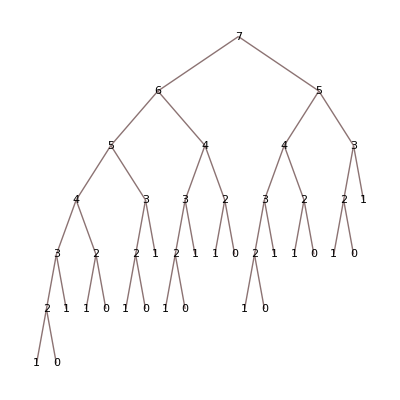

```mathematica
TreeForm[expr/.{List->Sequence}//.{fib2[x_,y__]:>x[y],fib2[x_]:>x}]
```

We can count how many times each fib2 was called. First create a list of patterns:

```mathematica
patterns=fib2[#,__]&/@Range[0,7]
```

{fib2[0,__],fib2[1,__],fib2[2,__],fib2[3,__],fib2[4,__],fib2[5,__],fib2[6,__],fib2[7,__]}

Now Map the count function:

```mathematica
{#/.fib2[a_,__]:>fib2[a],Count[{expr},#,Infinity]}&/@patterns
```

{{fib2[0],8},{fib2[1],13},{fib2[2],8},{fib2[3],5},{fib2[4],3},{fib2[5],2},{fib2[6],1},{fib2[7],1}}

The rule #/.fib2[a_,__]:->fib2[a] simply removes the pattern sign from fib2[number,__]. The funny thing is that the numbers of function calls form the reversed Fibonacci sequence - we could have guessed that.

The standard iterative solution (procedural)

There exists an elegant way in Mathematica to get an efficient implementation for the Fibonacci numbers using dynamic programming, and we will revisit this problem once we cover this topic. For now, let us see if we can find a more efficient implementation using the functions and techniques we already know.

The first thing which comes to mind is a procedural iterative implementation:

```mathematica
Clear[fibProc];
fibProc[n_Integer]:=Module[{prev,prprev,i,temp},For[prev=prprev=i=1,i<n,i++,temp=prprev;prprev=prev;prev=prev+temp;];prev];
```

For instance:

```mathematica
fibProc[7]
```

21

Producing a sequence of first n Fibonacci numbers

This above solution is decent if all one wants is to compute a given Fibonacci number. But what if we need a full sequence up to a given number? The better procedural solution then would be to create a list of numbers inside the For loop:

```mathematica
Clear[fibProcList];
fibProcList[n_Integer]:=Module[{prev,prprev,i,temp,reslist=Table[0,{n}]},For[prev=prprev=reslist[[1]]=i=1,i<n,i++,temp=prprev;prprev=reslist[[i+1]]=prev;prev=prev+temp;];reslist];
```

For example:

```mathematica
fibProcList[30]//Timing
```

{0.000184,{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}}

The timing is quite good actually (for Mathematica implementation). For this particular formulation, the procedural solution is among the best. Notice that the list to store the results is pre-allocated from the beginning. Had we started with an empty list and then Append to it repeatedly, the performance would be far worse. This leads us to appreciate another rule: pre-allocate large lists. But here, this was possible because we knew from the beginning how many numbers we want.

Producing all Fibonacci numbers less than a given number

Consider now a different formulation: we want all Fibonacci numbers smaller than a given number. Here, we don’t know a priori how large a list we will need. Of course, we can perform an analysis, make estimates etc, then preallocate a list guaranteed to be large enough, and then delete extra (unused) slots in the list at the end. But there could be similar problems for which such analysis is very difficult, and then one may end up pre-allocating huge lists where much smaller ones are actually needed, and thus waste resources.

On the other hand, Append-ing to a list repeatedly has efficiency problems well - known to us by now (this is not an absolute restriction however. In cases when the body of the loop - the function which produces the next result from the previous ones - is very computationally-demanding and takes most of the time, and at the same time the length of the list of results is not too large, the cost of Append-ing the list may be
negligible w.r.t other operations. In such cases, using Append is certainly a possibility).
Let us see if we can find another solution. What we would like to do is to make the system create a list of results internally, but stop depending on some condition applied to the results. This sounds like a good case for NestWhileList.

What is really important here is that NestWhileList has a formulation where it has access to a given number of the most recent results. On the other hand, a limitation of Nest or NestList is that a new function output is based only on the last result - the nested function does not have access to any past results except the last one. But for the Fibonacci numbers problem, we need to know the last 2 results. So, the main idea
of the solution is the following: given the use of NestWhileList in the form

```mathematica
NestWhileList[f, expr,test,m]
```

(m gives a maximal number of the most recent results to be supplied to the test condition) we can use a global variable to communicate the given number of most recent results from the <test> function to f:

```mathematica
Clear[fibList];
fibList[max_Integer]:=Module[{a=0},Drop[NestWhileList[a+#&,1,(a=#1)<max&,2],-2]];
```

What happens here is that the test function contains a side effect - an assignment to a variable <a>. A global variable <a> (well, we made it local with Module, but it is still “global” for the body of NestWhileList) is used to communicate to the function f (which is here a pure function that adds a “constant” <a> to the previous input), the current value of <a>, which is, in terms of the procedural solution, a value of <prprev> - the “previous previous” result. We have to Drop the last 2 results since they will be larger than the limiting number. Check:

```mathematica
fibList[1000000]//Timing
```

{0.000169,{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}}

We see that this solution not only does solve our present problem, but also beats our best procedural version for a previous fixed-n formulation! Also, the code is more concise and transparent, less variables are introduced etc. If we look back at the code, what happens is rather non-trivial: at every stage, a different value of <a> is embedded into a pure function, which is then used to produce a new number. In that
sense, at each stage we change a nesting function definition.

This technique should be applicable to other situations where we have to produce a list of results with the number of them unknown beforehand, and when both every next result and the termination condition depend on the results produced already.

### Fold and FoldList

#### Fold: syntax and starting examples

Fold is a generalization of Nest, for the case when the nested function is a function of two variables, rather than of a single variable. While the first supplied variable is again a result of the previous action of the function itself, a second argument is supplied externally by Fold, from a list which is a parameter to Fold.

So, the syntax:

```mathematica
Fold[f,start,secarglist]
```

Simple example:

```mathematica
Clear[f];
Fold[f,x,{a,b,c}]
```

f[f[f[x,a],b],c]

Fold is a remarkably useful function. One may think of it as follows: if <f> can be thought of as a function which realizes a transition between the states of some finite state machine each application of Fold is like “rotating the crank” of this finite state machine, and we will rotate it until there are elements left in the second argument list (this analogy belongs to David Wagner). The number of times that the function will
be nested, is equal to the length of the second argument list. The function FoldList is related to Fold in the same way as NestList to Nest - it gives all intermediate results of “rotating the crank”.

One very frequent use of Fold is recursion removal. This we will cover later in part II, chapter in recursion and iteration.

#### More examples:

Example: partial sums

```mathematica
FoldList[Plus,0,{a,b,c,d,e,f}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e,a+b+c+d+e+f}

Here, as compared to Fold, we get all the intermediate partial sums for free. At the same time, FoldList is almost as efficient as Plus@@ for the final sum:

```mathematica
FoldList[Plus,0,Range[100]]//Timing
```

{0.000085,{0,1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050}}

```mathematica
Plus@@Range[100]//Timing
```

{0.000083,5050}

The Total command is much faster on the small lists, however:

```mathematica
Total[Range[100]]//Timing
```

{0.000049,5050}

Example: position intervals for list splitting

Imagine that we are given a list of elements, and a list of partial lengths, which add to the length of the element list. The problem is to generate the list of position intervals, corresponding to splitting of the element list into sublists with the lengths given by the second list. It is not hard to convince oneself that the solution is given by:

```mathematica
Clear[splitIntervals];
splitIntervals[x_List,{lengths__Integer?NonNegative}]/;Total[{lengths}]==Length[x]:=Transpose[{Most[#],Rest[#]-1}&[FoldList[Plus,1,{lengths}]]]
```

The main idea is to generate the list of start and end points of the intervals from the partial sums of lengths, and then transpose them to get the intervals. For example:

```mathematica
splitIntervals[Range[10],{2,3,5}]
```

{{1,2},{3,5},{6,10}}

Application: splitting the list into sublists of specified lengths (generalized Take operation)

We can put the just developed function into a direct use to create a quite useful one: given a list and the list of partial lengths, split the original list into sublists of these lengths. Here is the code:

```mathematica
Clear[splitList];
splitList[x_List,{lengths__Integer?NonNegative}]/;Total[{lengths}]==Length[x]:=Map[Take[x,#]&,splitIntervals[x,{lengths}]];
```

Check:

```mathematica
splitList[Range[20],{2,1,5,6,2,4}]
```

{{1,2},{3},{4,5,6,7,8},{9,10,11,12,13,14},{15,16},{17,18,19,20}}

The final comment here is that this is an example of redundant error - checking as discussed at the end of section 5.2.7.3.2. To eliminate it in this case, it is best to embed the body of the <splitIntervals> function inside the <splitList> function, since it is really short (if we would have to write several functions using <
splitIntervals>, we would perhaps be better off putting everything into a package and making <splitIntervals> a private (internal) function - then we can remove type checks):

```mathematica
Clear[splitListAlt];
splitListALt[x_List,{lengths__Integer?NonNegative}]/;Total[{lengths}]==Length[x]:=Map[Take[x,#]&,Transpose[{Most[#],Rest[#]-1}&[FoldList[Plus,1,{lengths}]]]]
```

To see how much overhead the redundant type - checks induce in this case, we can perform a power test:

```mathematica
(splitList[Range[Total[Range[100]]],Range[100]]//Short[#]&)//Timing
```

{0.000802,{{1},«98»,{4951,4952,«96»,5049,5050}}}

```mathematica
(splitListAlt[Range[Total[Range[100]]],Range[100]]//Short[#]&)//Timing
```

{0.000058,splitListAlt[{1,2,«5046»,5049,5050},«1»]}

We see that both functions are quite fast (this is one of the fastest implementations of this function in Mathematica that I know of), and the difference is of the order of 10%. The difference would be more considerable if the patterns used in error-checking were more semantic (here they are mostly syntactic).

Example: imitating a factorial function

This is a (admittedly, rather inefficient) simulation of the factorial function with Fold.

```mathematica
Clear[ourFactorial];
ourFactorial[n_Integer?NonNegative]:=Fold[Times,1,Range[n]];
```

For instance,

```mathematica
ourFactorial/@Range[10]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

If, however, we have to generate a list of all consecutive factorials, then all we need to do is to change Fold to FoldList, and in this case this solution will be among the most efficient ones in Mathematica.

Example: imitating FromDigits

Here we will use Fold to imitate the <FromDigits> command. We are given a list of digits of a number, and the integer base. We have to reconstruct the number. If the base is not given, we should assume that it is 10. For example:

```mathematica
FromDigits[{2,4,5,2,3}]
```

24523

```mathematica
FromDigits[{1,0,0,1},2]
```

9

Here is the code using Fold:

```mathematica
Fold[#1*10+#2&,0,{2,4,5,2,3}]
```

24523

Here, we feed the digits one by one to a function which multiplies the previous result by 10 and adds a new digit at each step. It is clear how the code for the function will look like:

```mathematica
Clear[ourFromDigits];

ourFromDigits[digits_List]:=Fold[#1*10+#2&,0,digits];
ourFromDigits[digits_List,base_Integer?Positive]:=Fold[#1*base+#2&,0,digits];
```

Check:

```mathematica
ourFromDigits[{2,4,5,2,3}]
```

24523

```mathematica
ourFromDigits[{1,0,0,1},2]
```

9

We can express this as a single function by using the default values mechanism (optional patterns):

```mathematica
Clear[ourFromDigitsAlt];
ourFromDigitsAlt[digits_List,base_Integer:10]:=Fold[#1*base+#2&,0,digits];
```

Check now:

```mathematica
ourFromDigitsAlt[{2,4,5,2,3}]
```

24523

```mathematica
ourFromDigitsAlt[{1,0,0,1},2]
```

9

An interested reader may perform the efficiency analysis to see how close we get to the built-in FromDigits, for large numbers.

Example: powers of a differential operator

Here we consider the following problem: given a differential operator <oper>, construct an operator which will apply <oper> raised to some integer power, to a function <f>. However, we want to keep everything in an operator form: no explicit variables should be involved. The operator <oper> has to take a function <f>, and produce a pure function which corresponds to <oper>[f]. The new operator <oper-
Power> should take an operator <oper>, a function <f> , and an integer power  <n>, and produce a pure function <oper>^n[f]. Once any specific argument (say, <x> or <y> etc) is supplied, this has to evaluate to a function of this argument.

To be specific, consider the following operator <oper>:

```mathematica
HoldForm[x*f+D[f,x]]//TraditionalForm
```

x f+(∂f)/(∂x)

This is the code for it:

```mathematica
Clear[oper];
oper[expr_]:=(#*expr+D[expr,#])&;
```

For instance, this is the result of the single application of an operator:

```mathematica
oper[Sin[x]][x]
```

Cos[x]+x Sin[x]

What is important is that the action of an operator produces a function:

```mathematica
oper[Sin[y]][y]
```

Cos[y]+y Sin[y]

Note that <oper> defined in this way is vulnerable to misuse:

```mathematica
oper[Sin][x]//FullForm
```

Times[Sin,x]

```mathematica
oper[Sin[x]][y]
```

y Sin[x]

In both cases above the output is not what we would like. We should then consider it an auxiliary function, an input to <operPower>. Only the <operPower> should be used, and in particular it will give back the correct form of the operator <oper> if the power <n> =1.

Here is the code for operPower:

```mathematica
Clear[operPower];
operPower[oper_,f_,n_Integer?NonNegative]:=Module[{x},Fold[oper[#1][#2]&,f[x],Table[x,{n}]]/.x->#]&;
```

The code is somewhat tricky. The idea is that we use a local variable <x> and create a list like {x,x,...} of the length n. At each step, we supply it to <oper[#1][#2]&> as a second argument. But let us realize, that the result of the operation of <oper> at each step is a function, this is why we need to supply <x> to it as an argument to get an expression, and the syntax contains two pairs of square brackets one after another.
After Fold has finished, we have an expression depending only on x. We then use a substitution rule to convert the resulting expression depending on local <x> to a pure function, which is then the final result.

Check, for instance:

```mathematica
operPower[oper,Sin,0][x]
```

Sin[x]

```mathematica
operPower[oper,Sin,1][x]
```

Cos[x]+x Sin[x]

```mathematica
operPower[oper,Sin,2][x]
```

x Cos[x]+x (Cos[x]+x Sin[x])

The last case we may check also by hand:

```mathematica
x*(x*Sin[x]+D[Sin[x],x])+D[x*Sin[x]+D[Sin[x],x],x]
```

x Cos[x]+x (Cos[x]+x Sin[x])

We can also use pure functions with <operPower>:

```mathematica
operPower[oper,#^2&,3][x]
```

8 x+x^3+x (2+3 x^2)+x (2+3 x^2+x (2 x+x^3))

The advantage of this seemingly perverse solution is that we may separate functions from the arguments, and effectively carry operations on functions (internally, the arguments are used, but the user of this command does not need to know it).

Another comment: had we used FoldList instead of Fold, and we would get all the intermediate powers of our differential operator for free.

Example: autocorrelated random walks

Consider a following problem: we have a random walker, who can make unit steps to the left and to the right. Let the probability of step in each direction depend on the direction of the previous step. We may introduce a parameter <p> which tells how (anti) correlated or uncorrelated is our random walk. If <p> is close or equal to 0.5, the walk is almost or totally uncorrelated since the probability of a step to the right or to the left is the same and equal to 0.5. If <p> is close or equal to 1, the walk is  almost or totally correlated since the next step will almost certainly be in a direction of the previous step. If <p> is close to or equal to 0, then the walk is almost or totally anti - correlated since the next step will almost certainly be in the direction opposite to the previous step.

```mathematica
Clear[randomStep];
randomStep[p_Real,previous:1|-1]/;0<=p<=1:=If[previous==1,#,-#]&@Switch[p-Random[],_?Negative,-1,_?NonNegative,1]
```

Correlated situation

```mathematica
steps=NestList[randomStep[0.7,#]&,1,40]
```

{1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,1,1,1,1,-1,1,-1,-1,-1,1,-1,-1}

We need FoldList to build a trajectory from the steps:

```mathematica
trajectory=FoldList[Plus,0,steps]
```

{0,1,2,3,4,5,6,7,8,7,8,9,8,9,10,11,12,11,12,13,14,15,16,17,18,17,16,15,14,13,14,15,16,17,16,17,16,15,14,15,14,13}

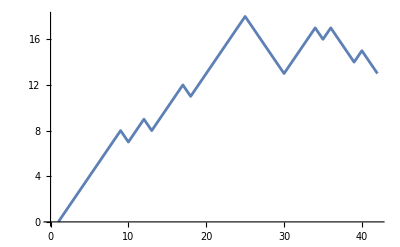

```mathematica
ListPlot[trajectory,Joined->True]
```

Anti - correlated situation

```mathematica
steps=NestList[randomStep[0.1,#]&,1,40]
```

{1,-1,1,-1,1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,-1,1}

```mathematica
trajectory=FoldList[Plus,0,steps]
```

{0,1,0,1,0,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,3,2,1,2,1,0,1}

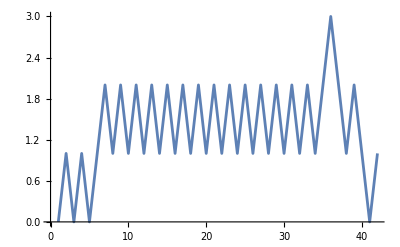

```mathematica
ListPlot[trajectory,Joined->True]
```

Example: linked lists and the fast accumulation of results

For many applications, one needs to be able to build up a list of some intermediate results obtained in some computation. The easiest way to set up such a list is to use Append or Prepend (or perhaps, AppendTo or PrependTo). However, for large lists this method is quite inefficient. The reason is that lists in Mathematica are implemented as arrays, and thus every time we add an element, the entire list is copied.

We can use FoldList to illustrate the creation of a list in such manner:

```mathematica
testlist=Table[RandomInteger[{1,15}],{10}]
```

{10,3,15,5,3,8,6,1,2,11}

```mathematica
FoldList[Append,{},testlist]
```

{{},{10},{10,3},{10,3,15},{10,3,15,5},{10,3,15,5,3},{10,3,15,5,3,8},{10,3,15,5,3,8,6},{10,3,15,5,3,8,6,1},{10,3,15,5,3,8,6,1,2},{10,3,15,5,3,8,6,1,2,11}}

Now, let us do some performance tests:

```mathematica
Fold[Append,{},Range[100]];//Timing
```

{0.000197,Null}

```mathematica
Fold[Append,{},Range[500]];//Timing
```

{0.000662,Null}

```mathematica
Fold[Append,{},Range[2000]];//Timing
```

{0.006504,Null}

```mathematica
Fold[Append,{},Range[5000]];//Timing
```

{0.03565,Null}

```mathematica
Fold[Append,{},Range[20000]];//Timing
```

{0.394937,Null}

We see that the time used by this operation is quadratic in the size of the list. We of course would like a linear time. One way to achieve this which is available starting with the Mathematica version 5.0 is to use the Reap-Sow technique (to be described in Part II). Another (perhaps, slightly less efficient) way to get a linear time is to use linked lists. We will follow the discussion in the book of David Wagner [7].

```mathematica
Clear[a,b,c,d];
```

A linked list in Mathematica is a structure of the type

```mathematica
{a,{b,{c,{d,{}}}}}
```

The advantage of this representation is that on every level, we have a list containing just 2 elements, which is easy to copy. It will not work in this way for elements that are lists themselves, but then one can replace a list by an arbitrary head <h>.

```mathematica
Clear[h];
h[a,h[b,h[c,h[d,h[]]]]]
```

To avoid a possible conflict with some <h> already defined, we can use Module[{h}, ...] to make it local.

Using Fold is the most natural way to create such structures:

```mathematica
ll1=Fold[{#2,#1}&,{},Reverse[{a,b,c,d}]]
```

{a,{b,{c,{d,{}}}}}

```mathematica
ll2=Fold[h[#2,#1]&,h[],Reverse[{a,b,c,d}]]
```

h[a,h[b,h[c,h[d,h[]]]]]

Converting them back to a normal list is just as easy with Flatten:

```mathematica
Flatten[ll1]
```

{a,b,c,d}

```mathematica
Flatten[ll2,Infinity,h]
```

h[a,b,c,d]

Notice that in the second case we used the fact that Flatten takes as an optional third argument the head which has to be Flatten-ed, and then Flatten - s only subexpressions with this head. In any case, this is another linear-time operation.

We can now write a function:

```mathematica
Clear[toLinkedList];
toLinkedList[x_List]:=Fold[{#2,#1}&,{},Reverse[x]];
```

Let us do some performance tests:

```mathematica
toLinkedList[Range[2000]];//Timing
```

{0.001052,Null}

```mathematica
toLinkedList[Range[5000]];//Timing
```

{0.001844,Null}

```mathematica
(ll3=toLinkedList[Range[20000]]);//Timing
```

{0.015404,Null}

We see that the time is roughly linear in the list size, and for example, for a list of 20000 we get already a speed-up of the order of 100 times! Flattening is even faster:

```mathematica
Flatten[ll3];//Timing
```

{0.00234,Null}

Here we assumed that the list of results is accumulated immediately, just to separate this topic from the other problem - specific part of a program. If the list is accumulated not immediately but some other operations are performed in between (which is what usually happens), one just has to use the idiom list = {newelement, list}, to achieve the same result.

Example: joining linked lists

Continuing with linked lists, consider another problem: how to efficiently join many linked lists into a single one. For example:

```mathematica
ll1=toLinkedList[Range[5]]
```

{1,{2,{3,{4,{5,{}}}}}}

```mathematica
ll2=toLinkedList[Range[6,10]]
```

{6,{7,{8,{9,{10,{}}}}}}

```mathematica
ll3=toLinkedList[Range[11,15]]
```

{11,{12,{13,{14,{15,{}}}}}}

We will now give a solution which works on lists of atoms. The key observation is that the empty list inside a linked list is always at level {-2}, and in the case of atomic lists, nothing else is on that level:

```mathematica
Level[ll2,{-2}]
```

{{}}

This means that if we want to join linked lists <x> and <y>, we just have to Map the entire list <y> on a level {-2} of the list <x>:

```mathematica
Map[ll2&,ll1,{-2}]
```

{1,{2,{3,{4,{5,{6,{7,{8,{9,{10,{}}}}}}}}}}}

If we want to join many lists, we can do it pairwise, and use Fold, to join the previously joined list with a next list at every step. So, here is a final function:

```mathematica
Clear[lljoin];
lljoin[x_List,y_List]:=Map[y&,x,{-2}];
lljoin[x__List]:=Fold[lljoin,{},{x}];
```

Check:

```mathematica
lljoin[ll1,ll2,ll3]
```

{1,{2,{3,{4,{5,{6,{7,{8,{9,{10,{11,{12,{13,{14,{15,{}}}}}}}}}}}}}}}}

#### Restriction of Fold-ed function to two arguments is spurious

Since the function to be Fold-ed can accept as a second (supplied externally by Fold) argument any expression, in particular a list, this means that we can actually supply as many arguments as we want. To illustrate this, consider the following example:

Example: random changes in the list

Here we take a list of 10 random integers in the range {1,100}. We then change the element at random position in this list by one of the symbols {a,b,c,d,e} (randomly chosen).

```mathematica
Clear[a,b,c,d,e];
```

Here is our list:

```mathematica
testlist=Table[RandomInteger[{1,100}],{10}]
```

{93,66,50,64,24,25,96,27,39,38}

```mathematica
changeList=Table[{{a,b,c,d,e}[[RandomInteger[{1,5}]]],RandomInteger[{1,10}]},{10}]
```

{{a,3},{d,1},{a,10},{c,2},{c,4},{d,5},{a,3},{a,10},{a,8},{d,10}}

We will use a combination of ReplacePart and Fold:

```mathematica
FoldList[ReplacePart[#1,Sequence@@#2]&,testlist,changeList]
```

{{93,66,50,64,24,25,96,27,39,38},{93,66,a,64,24,25,96,27,39,38},{d,66,a,64,24,25,96,27,39,38},{d,66,a,64,24,25,96,27,39,a},{d,c,a,64,24,25,96,27,39,a},{d,c,a,c,24,25,96,27,39,a},{d,c,a,c,d,25,96,27,39,a},{d,c,a,c,d,25,96,27,39,a},{d,c,a,c,d,25,96,27,39,a},{d,c,a,c,d,25,96,a,39,a},{d,c,a,c,d,25,96,a,39,d}}

We see that ReplacePart accepts 3 variables, not 2. What we did was to package the two variables {symbolToInsert, positionToReplace} into a list (single unit), and these lists were supplied to ReplacePart at every step. Plus, we used Apply[Sequence,...] idiom, which means - when package arrived, we can strip the wrapper to get the goodies.

Example: running standard deviation for an increasing or running list of data

Consider the following problem: given a data sample of N points, for which the mean <mean> and the standard deviation <sigma> have been computed, we add one more data point. We would like to compute the mean and the standard deviation of the modified sample using only the old values of <mean> and <sigma>, the number of points <N> and the value of the new added data point. Obviously, if we do this, we save a lot since we will not need to use all our points and recompute these quantities from scratch. It is not difficult to show that this can be done according to the following formulas:

x_NEW=N/(N+1)x_OLD+1/(N+1)Nest
σ_NEW=√(1/(N+1)(Nσ_OLD^2+N/(N+1)(x_OLD-new)^2))

Here are the implementations of the formula for the mean:

```mathematica
Clear[averIter];
averIter[prevaver_,n_,newel_]:=n/(n+1)*prevaver+1/(n+1)newel;
```

To check it, the code below computes the average of increasing list of natural numbers from {1} to {1, 2, 3, 4, 5}:

```mathematica
Module[{n=0},FoldList[averIter[#1,n++,#2]&,0,Range[5]]]
```

{0,1,3/2,2,5/2,3}

Below is the function for a standard deviation. Notice that there are many ways of implementing it, but we deliberately made it such that it accepts three arguments: the previous mean and previous sigma combined together in a list, the previous number of elements and the new element, and returns a list of new mean and new sigma.

```mathematica
Clear[sigmaIter];
sigmaIter[{prevaver_,prevsigma_},nold_Integer,newel_]:=Module[{newaver,newsigma},newaver=averIter[prevaver,nold,newel];newsigma=Sqrt[1/(nold+1)*((nold*prevsigma^2)+nold/(nold+1)(prevaver-newel)^2)];{newaver,newsigma}];
```

This is how we would use FoldList to generate pairs of {mean, sigma} for an increasing list of values (we use the same natural numbers as a test example):

```mathematica
Module[{n=0},Rest[FoldList[sigmaIter[#1,n++,#2]&,{0,0},Range[5]]]]
```

{{1,0},{3/2,1/2},{2,√(2/3)},{5/2,(√5)/2},{3,√2}}

Notice the use of n++ construct. This is a type of procedural code embedding which we already met discussing the Map function (see section 5.2.2.9). It is easy to check that this gives the same result as if we would use standard formulas:

```mathematica
CLear[meanSt,sigmaSt];
meanSt[x_List]:=Total[x]/Length[x];
sigmaSt[x_List]:=Sqrt[Total[(x-meanSt[x])^2/Length[x]]]
```

Note that in the part for <sigma> I used the vectorized nature (Listability) of Subtract and Power functions. Check:

```mathematica
Map[{meanSt[#],sigmaSt[#]}&,Range/@Range[5]]
```

{{1,0},{3/2,1/2},{2,√(2/3)},{5/2,(√5)/2},{3,√2}}

We can now package this into a function:

```mathematica
Clear[meanAndSigmaAccumulative];
meanAndSigmaAccumulative[x_List]:=Module[{n=0},Rest[FoldList[sigmaIter[#1,n++,#2]&,{0,0},x]]];
```

We can see how much we win on large lists:

```mathematica
(ms1=Map[{meanSt[#],sigmaSt[#]}&,Range/@Range[500]]//Short[#]&)//Timing
```

{0.082798,{{1,0},{3/2,1/2},«497»,{501/2,(√83333)/2}}}

```mathematica
(ms2=meanAndSigmaAccumulative[Range[500]]//Short[#]&)//Timing
```

{0.010362,{{1,0},{3/2,1/2},«497»,{501/2,(√83333)/2}}}

```mathematica
ms1==ms2
```

True

The complexities are different so the difference will be larger for larger lists. Also, it is not as dramatic as in other languages because the second (general) implementation is helped by the fact that operations such as list subtraction or totalizing are Listable and highly optimized in Mathematica, whereas the one with FoldList necessarily breaks the process into pieces and thus looses this advantage.

Another situation where this may be useful is when, while one point is added to the sample, some other point is removed from it. This case can be treated in the same way (it is easy to derive the corresponding formulas), and will correspond to what we can really call the “running” standard deviation. The implementation of it is left as an exercise to the reader.

#### Case study: Gram-Schmidt orthogonalization

A crash course on linear algebra and Gram-Schmidt procedure

We are given a number of vectors of dimension <n> (there can be at most <n> linearly independent). Vectors will be represented as lists of length <n>. The dot product on these vectors is defined as a sum of products of individual components (we assume flat Euclidean metric). For example:

```mathematica
vec1={a1,b1,c1}
vec2={a2,b2,c2}
```

{a1,b1,c1}

{a2,b2,c2}

Then, the dot product:

```mathematica
Dot[vec1,vec2]
```

a1 a2+b1 b2+c1 c2

where we used a built-in function Dot. Equivalently, we may write (dot is a shorthand notation for Dot)

```mathematica
vec1.vec2
```

a1 a2+b1 b2+c1 c2

A norm of the vector is defined as a square root of the dot product of vector with itself. For instance, the norm of <vec1> will be

```mathematica
Sqrt[vec1.vec1]
```

√(a1^2+b1^2+c1^2)

Geometrically the norm of the vector is its length. The above result may be considered as a generalization of a Pythagorean theorem to n-dimensional space (n=3 in this case). The vector is normalized when its norm is 1. Any vector can be normalized by dividing the vector by its norm. For instance,

```mathematica
vec1/Sqrt[vec1.vec1]
```

{a1/(√(a1^2+b1^2+c1^2)),b1/(√(a1^2+b1^2+c1^2)),c1/(√(a1^2+b1^2+c1^2))}

is normalized.

A linear combination of some number of vectors is a sum of these vectors multiplied by some coefficients - it is another vector. For instance, vector <vec3>

```mathematica
vec3=α*vec1+β*vec2
```

{a1 α+a2 β,b1 α+b2 β,c1 α+c2 β}

is a linear combination of <vec1> and <vec2> (a and b are some parameters). One may consider linear combinations of any number of vectors.

A set of vectors is said to be linearly independent if none of them can be represented as a linear combination of the others with some coefficients non-zero.

Any linearly-independent set of vectors defines a basis in a linear space, which is said to be spanned on these vectors. This means that any vector in this space can be written as a linear combination of the basis vectors, and vice versa, any vector which is a linear combination of these, belongs to this space. The dimension of this space is equal to a number of the vectors in the basis. To form a basis in the linear space
of dimension <n>, we then need <n> vectors.

Two vectors are orthogonal when their dot product vanishes. The problem of orthogonalization of a set vectors consists of finding linear combinations of these vectors which are mutually orthogonal. Most of the time, one is interested in finding an orthonormal basis in a given linear space. In other words, given a number of (not necessarily orthogonal) linearly-independent vectors, we would like to find linear combinations of these vectors which will be mutually orthogonal.

The Gram-Schmidt orthogonalization procedure consists of the following steps:

1. Pick any vector from the initial set, call it v1.
2. Pick some other vector, call it v2.
3. Construct a new vector as v2New = v2 - (v2.v1)/(v1.v1) *v1; this new vector will be orthogonal to v1, as is easy to verify.
4. Pick another vector v3, and construct a new one as v3New = v3 - (v3.v1)/(v1.v1) *v1 - (v3.v2New)/(v2New.v2New)*v2New; this one will be orthogonal to both v1 and v2New (which is also easy to verify, remembering that v2New is orthogonal to v1).
5. The procedure goes on, until all the resulting vectors are mutually orthogonal.

This description may suggest that depending on the sequence in which we orthogonalize the vectors, we may get different sets of final orthogonal basis vectors. Although this is not obvious, all these sets will be equivalent (after the vectors are normalized) up to relabeling which vector is the first, second etc.

We will now implement a one step of this procedure. Assume that we have some number <m> of orthogonal vectors of length <n> already stored in the m x n matrix <vecmat>, and a new vector <vec> which we want to make orthogonal to those in the <vecmat>.

Implementing a single step of the Gram-Schmidt procedure

Here is the code for a single step of the Gram-Schmidt procedure:

```mathematica
Clear[oneStepOrtogonalize];
oneStepOrtogonalize[vec_List,{}]:=vec;
oneStepOrtogonalize[vec_List,vecmat_?MatrixQ]:=Fold[(#1-(vec.#2)/(#2.#2)*#2)&,vec,vecmat];
```

The first rule is added to include the case of the first vector - then it has to be simply returned back.

As a simple example, consider the matrix of vectors being vecmat = {1,0,0},{0,0,1}}, and the vector to be made orthogonal to these, vec = {1,1,2}.

```mathematica
oneStepOrtogonalize[{1,1,2},{{1,0,0},{0,0,1}}]
```

{0,1,0}

The result is as we would expect - the missing basis vector. The way the code works is that the vector matrix is considered a list of second arguments to the function being Fold-ed. So, these second arguments will be vectors in this matrix. At each step, the initial vector gets transformed to be orthogonal to the vector supplied by Fold from the vector matrix at that step. When Fold is finished, the resulting vector is orthogonal to all of the vectors in the matrix.

Orthogonalization - the complete solution

Now that we worked out a single step, we have to get a complete solution, which will orthogonalize a given number of vectors.

Say, our initial vectors are

```mathematica
startVectors={{1,2,3},{5,2,7},{3,5,1}}
```

{{1,2,3},{5,2,7},{3,5,1}}

The solution is immediate with another Fold:

```mathematica
result=Fold[Append[#1,oneStepOrtogonalize[#2,#1]]&,{},startVectors]
```

{{1,2,3},{20/7,-16/7,4/7},{7/3,7/3,-7/3}}

What happens here is that a newly orthogonalized vector is appended to the current (initially empty) vector matrix. The new vector matrix is then used for orthogonalization of the next vector, etc. We can check that all the resulting vectors are mutually orthogonal:

```mathematica
Outer[Dot,result,result,1]
```

{{14,0,0},{0,96/7,0},{0,0,49/3}}

Notice the use of Outer here - we generated at once all the dot products. Since we wanted the vectors inside the matrix <result> to be treated as single units (to be plugged into Dot), we used the more general form of Outer (See section 5.3.4.8). The numbers on the diagonal are the norms squared of the three vectors. All off-diagonal elements are zero as they should be for orthogonal vectors.

Now, we can package the code into a function:

```mathematica
Clear[GSOrthogonalize];
GSOrthogonalize[startvecs_?MatrixQ]:=Fold[Append[#1,oneStepOrtogonalize[#2,#1]]&,{},startvecs];
```

And for completeness, we present once again the code for oneStepOrtogonalize:

```mathematica
Clear[oneStepOrtogonalize];
oneStepOrtogonalize[vec_List,{}]:=vec;
oneStepOrtogonalize[vec_List,vecmat_?MatrixQ]:=Fold[(#1-(vec.#2)/(#2.#2)*#2)&,vec,vecmat];
```

This is then our final implementation which solves the problem of Gram-Schmidt orthogonalization. It is concise, transparent and efficient (well, the purists will insist on eliminating Append. However, for large number of vectors, the cost of Append will be negligible w.r.t. the cost of <oneStepOrtogonalize>).

Note that the number of vectors to be orthogonalized may be smaller than the size of the vectors. But what happens if we try to orthogonalize more vectors than the size of the vector (or, dimension of the linear space)? For instance:

```mathematica
GSOrthogonalize[{{1,2},{5,3},{4,7}}]
```

{{1,2},{14/5,-7/5},{0,0}}

We see that the last vector is zero. This is as it should be - there can not be more linearly independent vectors than the length of the vector. Notice that this case was an automatic consequence of our procedure and did not require any special treatment.

Adding normalization

Now we would like to make the resulting vectors not only orthogonal, but orthonormal (orthonormalize - make them all be also normalized).

To do this, first define a function to normalize a vector:

```mathematica
Clear[normalize];
normalize[vec_List]:=vec/Sqrt[Dot[vec,vec]];
```

And now define GSOrthoNormalize

```mathematica
Clear[GSOrthoNormalize];
GSOrthoNormalize[startvecs_?MatrixQ]:=Map[normalize,GSOrthogonalize[startvecs]];
```

Now check:

```mathematica
newresult=GSOrthoNormalize[startVectors]
```

{{1/(√14),√(2/7),3/(√14)},{5/(√42),-2 √(2/21),1/(√42)},{1/(√3),1/(√3),-1/(√3)}}

What we did is just to Map <normalize> on the resulting vectors once they are obtained. It is easy to check that now all the vectors are orthonormal:

```mathematica
Outer[Dot,newresult,newresult,1]//Simplify
```

{{1,0,0},{0,1,0},{0,0,1}}

Application: generating random orthogonal matrices

As an application of the Gram-Schmidt method, we may consider a generation of random orthogonal matrices. The square matrix is called orthogonal if all the columns (rows) in it are normalized and mutually orthogonal. These matrices have important applications in various branches of science.

Basically, the procedure to generate a random orthogonal matrix is very simple: generate a plain random matrix, check that it has a non-zero determinant (if this is not so, it means that one of the columns - or rows - can be represented as a linear combination of the others. We will not consider such cases), and then simply apply our GSOrthoNormalize function to it. The result will be a random orthogonal matrix (this is of course an oversimplification. To unambiguously specify what we mean by a random matrix, we have to specify the probability distributions for all its elements. So, what we will generate here will be <some> random orthogonal matrix.

More specifically, the rows of this matrix are eigenvectors of the underlying one we start with, and for the latter one we will use the uniform [0,1] distribution for all matrix elements).

So, let us start with the example:

First generate a 3x3 random matrix

```mathematica
matrix=Table[Random[],{3},{3}]
```

{{0.578771,0.265649,0.79203},{0.788092,0.359179,0.602497},{0.373613,0.308055,0.847454}}

Check the determinant

```mathematica
Det[matrix]
```

0.037128

Apply our function (if the determinant is zero with your run, please rerun the above until it is nonzero):

```mathematica
GSOrthoNormalize[matrix]
```

{{0.569491,0.261389,0.77933},{0.711509,0.318016,-0.626594},{-0.411625,0.91134,-0.00487327}}

Now we will package this into another function:

```mathematica
Clear[randomOrthogonal];
randomOrthogonal[n_Integer?Positive]:=GSOrthoNormalize[NestWhile[Array[Random[]&,{n,n}]&,{{0}},Det[#]===0&]];
```

Here I used Array instead of Table, since it is slightly faster. But one could use Table as well. The use of NestWhile guarantees that the result of it will have a non-zero determinant. Check:

```mathematica
randomOrthogonal[3]
```

{{0.523174,0.825194,0.212942},{-0.428851,0.0389923,0.902533},{0.736462,-0.563502,0.374285}}

```mathematica
randomOrthogonal[5]
```

{{0.533457,0.681281,0.119514,0.129321,0.469332},{0.0350009,-0.470172,0.700089,0.403475,0.353267},{-0.244059,0.175256,-0.31095,0.890252,-0.143118},{0.534486,0.0352428,0.315007,0.125282,-0.773407},{-0.60742,0.531825,0.547424,-0.110637,-0.190498}}

Performance analysis

This is how much time it takes to generate 50x50 random orthogonal matrix with this method:

```mathematica
randomOrthogonal[50];//Timing
```

{0.005985,Null}

Assuming that the dot product is optimized and is roughly constant time for small vector sizes,we expect the complexity to be roughly quadratic with the matrix size for small matrices. This is because we have to ensure the mutual orthogonality of all vectors, and the number of vector pairs grows quadratically with the number of vectors. We can check our expectations:

```mathematica
randomOrthogonal[12];//Timing
```

{0.000875,Null}

```mathematica
randomOrthogonal[25];//Timing
```

{0.002122,Null}

```mathematica
randomOrthogonal[50];//Timing
```

{0.004304,Null}

```mathematica
randomOrthogonal[100];//Timing
```

{0.027016,Null}

```mathematica
randomOrthogonal[400];//Timing
```

{1.32374,Null}

We see that we actually get even a slightly better situation, due most likely to an optimized nature of Fold. One final comment: one can somewhat improve the performance by caching the norms of the vectors computed during the Gram-Schmidt procedure - we recompute them every time afresh. This can give a factor of 1.5~2 speed-up.

Appendix: the complete code for Gram-Schmidt orthogonalization

Here we just put the complete code (functions) into a single place:

```mathematica
Clear[oneStepOrthogonalize,GSOrthogonalize,normalize,GSOrthoNormalize,randomOrthogonal];
```

```mathematica
oneStepOrtogonalize[vec_List,{}]:=vec;
oneStepOrtogonalize[vec_List,vecmat_?MatrixQ]:=Fold[(#1-(vec.#2)/(#2.#2).#2)&,vec,vecmat];

GSOrthogonalize[startvecs_?MatrixQ]:=Fold[Append[#1,oneStepOrtogonalize[#2,#1]]&,{},startvecs];

normalize[vec_List]:=vec/Sqrt[Dot[vec,vec]];
GSOrthoNormalize[startvecs_?MatrixQ]:=Map[normalize,GSOrthogonalize[startvecs]];
randomOrthogonal[n_Integer?Positive]:=GSOrthoNormalize[NestWhile[Array[Random[]&,{n,n}]&,{{0}},Det[#]===0&]];
```

We see that the code is concise and transparent. This is an example of how the typical solution to a given problem looks in Mathematica.

#### Small case study: local maxima for a list

The problem

Sometimes, Fold (FoldList) allows for extremely concise and beautiful solutions. For example, here is the problem: for a given list of numbers, produce list of all its elements that are larger than any element before it, in this list (this is one of the favorite problems in many texts on Mathematica programming, so I decided to continue the tradition).

Here is our test list:

```mathematica
lst=Table[RandomInteger[{1,40}],{25}]
```

{33,17,31,6,21,17,10,27,2,19,25,8,17,11,27,14,38,7,1,37,32,19,8,25,11}

Procedural solution

It is fairly obvious how to write a procedural solution:

```mathematica
Clear[localMaxListProc];
localMaxListProc[x_List]:=Module[{i,temp,len=Length[x],reslist,solctr},For[reslist=Table[Null,{len}];temp=0;i=solctr=1,i<=len,i++,If[temp<x[[i]],reslist[[solctr++]]=temp=x[[i]]];];Drop[reslist,-(len-solctr+1)]];
```

Here, we preallocate the list of results, since we know that its length can be at most equal to the length of the initial list. As in cases before, this is done to avoid using Append and make a code more efficient. Check:

```mathematica
localMaxListProc[lst]
```

{33,38}

Functional solution with FoldList

This is essentially the same solution but expressed with FoldList:

```mathematica
Clear[localMaxList];
localMaxList[x_List]:=Union[Rest[FoldList[Max,-Infinity,x]]];
```

Check:

```mathematica
localMaxList[lst]
```

{33,38}

To see, what happens, we can dissect the function into pieces:

```mathematica
FoldList[Max,-Infinity,lst]
```

{-∞,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,38,38,38,38,38,38,38,38,38}

Here, at every iteration the result of the previous application of Max is compared with the next number from the list (we could have put Max[#1,#2]& ), and the maximum of the two becomes the current result. Thus,the next result will only be different from the previous if we get a number larger than all encountered before. The value -∞ is used as a starting number, to guarantee that the starting number will be less than any in the list (which may also contain negative numbers).

At the next stage, we delete this number with the help of Rest:

```mathematica
Rest[FoldList[Max,-Infinity,lst]]
```

{33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,38,38,38,38,38,38,38,38,38}

Finally, we take the Union to eliminate duplicate elements. Union also sorts the results in an ascending order, but in our case this is just fine.

```mathematica
Union[Rest[FoldList[Max,-Infinity,lst]]]
```

{33,38}

Performance analysis

We can now compare the performance:

```mathematica
testlst=Table[RandomInteger[{1,20000}],{5000}];
```

```mathematica
localMaxListProc[testlst];//Timing
```

{0.009046,Null}

```mathematica
localMaxList[testlst];//Timing
```

{0.003199,Null}

We see that by using Fold, we gain a factor of 3-4 in this case (for this size of the test list), even though we took care to make the procedural realization efficient, and indeed naively it looks more efficient since it does not produce an entire list and then delete similar elements. However, what it does is to break an object (list) into pieces by using array indexing. And according to one of our rules of thumb, this practice
should be avoided in Mathematica.

### FixedPoint and FixedPointList

#### The syntax and functionality

These functions are very similar to Nest and NestList. Instead of asking, how many times the function should be nested, they nest the function until the result no longer changes. The format is

```mathematica
FixedPoint[f,expr]
```

In some cases, it is desirable to have a “safety net” - to stop nesting after certain maximal allowed number of iterations regardless of whether or not the result has stabilized. To account for these cases, there is an optional third argument <n> which gives a maximal number of iterations.

Since these functions are very similar to Nest/NestList except their termination condition, we will illustrate them by revisiting certain examples considered before.

#### Example: the Collatz problem revisited

Here is the already discussed (section 5.4.2.6) Collatz iteration definition:

```mathematica
Clear[c];
c[n_?OddQ]:=3*n+1;
c[n_?EvenQ]:=n/2;
```

Previously we solved the problem of generation of the Collatz sequence by using NestWhileList. The solution was:

```mathematica
Clear[colSequence];
colSequence[q_Integer]:=NestWhileList[c,q,#1!=1&];
```

Imagine for a moment that it is unavailable (like it was in earlier versions of Mathematica). Can we find a substitute? Here is the solution that uses FixedPointList:

```mathematica
Clear[colSequenceFP];
colSequenceFP[q_Integer]:=Drop[FixedPointList[If[#!=1,c[#],1]&,q],-1];
```

(here, FP stands for “FiexedPoint”). The idea is that after the result becomes one for the first time, it will remain one due to the way the nested function is written. Then, after the next iteration, the last two results will be both equal to 1 and to each other, and thus the process will stop. For instance

```mathematica
colSequence[233]
```

{233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
colSequenceFP[233]
```

{233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

The new solution is almost as efficient as the old one. The source of inefficiency here is that the condition that the result is one, is checked as every iteration. Note by the way that both the implementation with NestWhileList and FixedPointList (as well as these constructs themselves) are a kind of compromise, appreciating that procedural style is sometimes more appropriate than functional (this is, when at every time only very small and very “local” part of a given large structure (like list) is changed).

#### How to reformulate a problem for FixedPoint

Basically, every problem where one has to generate some list by repeated nesting of a function <f>, and stop when certain condition <cond>is satisfied, can be  reformulated as a problem for FixedPoint, in the following way:

```mathematica
FixedPoint[If[cond[#],#,f[#]&,expr]]
```

The logic here is the same as for the Collatz problem just considered.

#### Example: deleting numbers from the list revisited

Here is a list containing in general zeros, positive and negative integers.

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{-5,10}],{15}]
```

{5,10,4,-2,10,5,8,-3,3,7,5,-3,-1,-5,7}

This will drop the first element in the list until it meets a first negative number - this is the solution we had before:

```mathematica
NestWhile[Drop[#,1]&,testlist,NonNegative[First[#]]&]
```

{-2,10,5,8,-3,3,7,5,-3,-1,-5,7}

The solution with FixedPoint:

```mathematica
FixedPoint[If[Negative[First[#]],#,Drop[#,1]]&,testlist]
```

{-2,10,5,8,-3,3,7,5,-3,-1,-5,7}

Note: the same performance pitfall which we discussed for the NestWhile - based solution of this problem (section 5.4.2.1), is also present here.

#### Example: approximating the square root of a number revisited

Here is the sequence that we implemented previously with Nest to get an approximation to a square root of a number:

t_(n+1)=1/2(t_n+A/t_n)

This was our solution (we take a specific number 3, and a starting number 5., as before)

```mathematica
NestList[(#+3/#)/2&,5.,5]
```

{5.,2.8,1.93571,1.74276,1.73208,1.73205}

Here our starting number was 5, and we used 5 iterations altogether. The list of intermediate results shows that this method converges quite fast. If we are interested in final result only, then we use Nest:

```mathematica
result=Nest[(#+3/#)/2&,5.,5]
```

1.73205

Now, here is the solution with FixedPoint:

```mathematica
newresult=FixedPointList[(#+3/#)/2&,5.]
```

{5.,2.8,1.93571,1.74276,1.73208,1.73205,1.73205,1.73205}

It is even simpler in this case - once the number stops changing , that’s it! This is a type of problem where FixedPoint works most directly without modifications.

The rest of the discussion of that example can be trivially transferred to the version with FixedPoint.

#### FixedPoint dangers

When used without the “safety net”, FixedPoint has an obvious danger of getting in a situation where it will never stop, because the results may happen to always be different. But even in the seemingly clear cases, this danger is not as far away as we may think. Let me use the same setting as in the previous example: we want to estimate the square root of 3, starting with a number 5. I will alter it very slightly -
forget to put the dot after 5: use <5> instead of <5.>. And, let us use a safety net of 7 iterations maximum - just in case...

```mathematica
FixedPointList[(#+3/#)/2&,5,7]
```

{5,14/5,271/140,132241/75880,34761005281/20068894160,2416609026561556205761/1395229871759180117920,11679998372406206859888818654055765884968321/6743450204443114328549416278518687526674240,272844723958823282612658628263013873237021400356408160879437661848300809304604412291841/157526974824595756512861009809263458922744712800339912508216462467898433196289773502080}

This is an unpleasant surprise. The point is that the operations are now done with arbitrary precision integer arithmetic, and the two consecutive results will never be the same. This tells us once again that we have to ensure in every case, that “sameness” is defined the same (pun unintended) for us and for Mathematica. If in doubt - put a maximum on the total number of iterations (although for final version of any program, you will be better off using the final iteration number only if there are more compelling reasons to do so, related to the structure of the problem. This comment does not apply for programs which implement certain functionality for further use, such as packages - in such cases it is always a good idea to constrain the number of iterations by some maximum value).

#### Small case study: merging overlapping intervals - Functional vs. Rule-based

The problem and a rule-based solution

Consider the following problem: given a list of intervals, some of which may overlap (such that some intervals may be entirely contained in others), write a function which will merge together those intervals which overlap, and return a modified list of intervals. The input list of intervals must be ordered in the sense that non-overlapping intervals closer to the origin should be on the left of those further from it.

Here is an elegant and concise rule-based solution shown in “Mastering Mathematica” by John Gray.

```mathematica
Clear[mergeIntervals];
mergeIntervals[ints_List]:=ints//.{e___,{a_,b_},{c_,d_},f___}/;c<=b:>{e,{a,Max[b,d]},f};
```

The code is almost self-explanatory. We saw already examples of this type of programming earlier - see the section 4.2.5. The use of //. (ReplaceRepeated) ensures that the rule will be applied until all overlapping intervals are merged. For instance:

```mathematica
mergeIntervals[{{1,3},{2,4},{5,7},{6,8},{7,9}}]
```

{{1,4},{5,9}}

A functional solution

The above solution is definitely beautiful and clear. However, it is not the most efficient one, as we will see in a minute.

Let us see what we can do within the functional style. The first thing that comes to mind is to somehow group together overlapping intervals, keeping in mind that there can be chains of more than two intervals overlapping, like the last 3 intervals in the above example. The way to do it is to use a built-in <Split> command. Split does the following: it groups together the “same” elements, and we can define what we mean by “same”, by providing to Split a comparison function. The limitation of Split is however that it can only compare adjacent elements.

So, let us define two intervals to be “the same” (for Split), when the right end of the first interval is larger than the left end of the second one:

```mathematica
step1=Split[{{1,3},{2,4},{5,7},{6,8},{7,9}},#1[[2]]>=#2[[1]]&]
```

{{{1,3},{2,4}},{{5,7},{6,8},{7,9}}}

We see that the intervals have been correctly grouped. Now we need to extract the new borders corresponding to the merged intervals. To do this, I suggest that we Flatten each group first (which means we have to Map Flatten on our list):

```mathematica
step2=Flatten/@step1
```

{{1,3,2,4},{5,7,6,8,7,9}}

Now we can Sort each Flattened sublist:

```mathematica
step3=Sort/@step2
```

{{1,2,3,4},{5,6,7,7,8,9}}

It now remains to take the first and last element of each sublist -since they are sorted, these will be the new borders:

```mathematica
step4=#[[{1,-1}]]&/@step3
```

{{1,4},{5,9}}

This is the result in this case. We can now put all the operations together:

```mathematica
Sort[Flatten[#]][[{1,-1}]]&/@Split[{{1,3},{2,4},{5,7},{6,8},{7,9}},#1[[2]]>=#2[[1]]&]
```

{{1,4},{5,9}}

This seems to solve the problem, but there is one subtle point. Consider the intervals:
{{5,9},{6,7},{8,10}}. Let us see what we get:

```mathematica
Sort[Flatten[#]][[{1,-1}]]&/@Split[{{5,9},{6,7},{8,10}},#1[[2]]>=#2[[1]]&]
```

{{5,9},{8,10}}

The problem is, that the resulting two intervals overlap and should have been combined into a single one, but this did not happen. The reason is that at the time when Split was grouping elements, the intervals {6,7} and {8,10} did not overlap - the overlap is induced by a previous interval {5,9} which entirely contains {6,7}. But since Split is limited to compare only adjacent elements, there seems to be no way
out. Our solution then will be the following: use the code above as a “single step” transformation, and apply it repeatedly to the list until the list stops changing. Here is the code for a single step merging:

```mathematica
Clear[mergeIntsOneStep];
mergeIntsOneStep[ints_List]:=Map[Part[Sort[Flatten[#]],{1,-1}]&,Split[ints,#1[[2]]>=#2[[1]]&]];
```

And this is all we need to add to solve the problem:

```mathematica
Clear[mergeInts];
mergeInts[ints_List]:=FixedPoint[mergeIntsOneStep,ints];
```

Check now:

```mathematica
mergeInts[{{1,3},{2,4},{5,7},{6,8},{7,9}}]
```

{{1,4},{5,9}}

```mathematica
mergeInts[{{5,9},{6,7},{8,10}}]
```

{{5,10}}

Comparing performance

Let us now compare the efficiency of the rule-based and procedural solutions, on interval lists of different lengths. We will generate these lists randomly. The code to generate the lists is as follows:

```mathematica
Clear[randomIntervals];
randomIntervals[min_Integer,max_Integer,maxrange_Integer?Positive,intnum_Integer?Positive]:=Module[{x},Sort[Table[{x=RandomInteger[{min,max}],x+RandomInteger[{1,maxrange}]},{intnum}],#1[[1]]<#2[[1]]&]];
```

For instance, this will be a list of 10 intervals with borders from 1 to 100 and maximal length of an interval 8:

```mathematica
testints=randomIntervals[1,100,8,10]
```

{{21,24},{34,37},{41,45},{42,44},{56,63},{68,72},{72,79},{84,85},{94,98},{96,104}}

We now test the performance:

```mathematica
mergeIntervals[testints]//Timing
```

{0.00015,{{21,24},{34,37},{41,45},{56,63},{68,79},{84,85},{94,104}}}

```mathematica
mergeInts[testints]//Timing
```

{0.000097,{{21,24},{34,37},{41,45},{56,63},{68,79},{84,85},{94,104}}}

For this very small list, the performance is roughly the same. Let us increase the number of intervals:

```mathematica
(testints=randomIntervals[1,1000,15,100])//Short
```

{{1,15},«98»,{1000,1014}}

Now:

```mathematica
mergeIntervals[testints]//Timing
```

{0.002403,{{1,15},{20,47},{59,86},{103,120},{134,156},{160,177},{181,195},{201,230},{236,247},{263,274},{303,317},{328,333},{341,347},{355,358},{362,367},{368,371},{380,393},{394,411},{425,449},{451,460},{469,479},{483,484},{486,504},{524,534},{541,553},{554,565},{582,587},{608,610},{616,627},{629,630},{646,649},{663,665},{666,673},{674,702},{711,714},{718,720},{726,740},{757,763},{764,791},{793,800},{803,810},{852,876},{886,899},{901,916},{925,933},{946,962},{974,977},{981,999},{1000,1014}}}

```mathematica
mergeInts[testints]//Timing
```

{0.000569,{{1,15},{20,47},{59,86},{103,120},{134,156},{160,177},{181,195},{201,230},{236,247},{263,274},{303,317},{328,333},{341,347},{355,358},{362,367},{368,371},{380,393},{394,411},{425,449},{451,460},{469,479},{483,484},{486,504},{524,534},{541,553},{554,565},{582,587},{608,610},{616,627},{629,630},{646,649},{663,665},{666,673},{674,702},{711,714},{718,720},{726,740},{757,763},{764,791},{793,800},{803,810},{852,876},{886,899},{901,916},{925,933},{946,962},{974,977},{981,999},{1000,1014}}}

Here we see that our functional version is already 5 times faster. Let us increase even more:

```mathematica
(testints=randomIntervals[1,4000,25,500])//Short
```

{{1,23},{5,9},«497»,{3997,4018}}

```mathematica
(mergeIntervals[testints]//Short[#]&)//Timing
```

{0.031011,{{1,65},«101»,{3997,4018}}}

```mathematica
(mergeInts[testints]//Short[#]&)//Timing
```

{0.002773,{{1,65},«101»,{3997,4018}}}

Here the difference is more than an order of magnitude. What happens is that these solutions have different computational complexities. The reason is that the functional solution is able to group more than two overlapping intervals together in a single run through the list, while the rule-based solution can only group two adjacent intervals at a time. Thus, it needs more runs through the list, and as the length of the list increases, we pay for it more and more. In other words, the inefficiency is because it repeatedly checks non-overlapping intervals for matching the overlap pattern. In terms of our rules of thumb, this is a case for this one: “avoid inefficient patterns”.

Concluding remarks

So, what should be our conclusion? Is the rule-based solution necessarily bad, should we avoid it always and at all costs? I don’t think so. It is certainly easier to write and it communicates the idea more clearly. What is important is to develop the skill to recognize inefficiency in the code, so that, if a given part of the code turns out to be time-critical, you will be able to quickly spot the “bottleneck” and rewrite the code
more efficiently.

#### Example: local (relative) maxima in a list revisited

Let us revisit a problem of finding a list of local maxima for a given list - that is, a list of all elements which are larger than any element before it in the input list. We have given a solution using Fold (the best we have) and a procedural solution, in the chapter on Fold. Now we will consider a solution based on FixedPoint. It will not be as efficient, but it represents an interesting way of thinking in my view.

So, here is our test list:

```mathematica
tlist=Table[RandomInteger[{1,40}],{20}]
```

{27,7,10,23,33,13,21,30,20,13,9,15,5,27,25,26,31,30,38,30}

Consider a following transformation of this list: we will Split it into sublists of decreasing (non-increasing) elements, and then only keep a maximum (the left - most element) of each sublist:

```mathematica
step1=Split[tlist,GreaterEqual]
```

{{27,7},{10},{23},{33,13},{21},{30,20,13,9},{15,5},{27,25},{26},{31,30},{38,30}}

```mathematica
step1=Map[First,step1]
```

{27,10,23,33,21,30,15,27,26,31,38}

Or, we can combine this as:

```mathematica
step1=Map[First,Split[#,GreaterEqual]]&[tlist]
```

{27,10,23,33,21,30,15,27,26,31,38}

Now, we can iterate a few times:

```mathematica
step2=Map[First,Split[#,GreaterEqual]]&[step1]
```

{27,23,33,30,27,31,38}

```mathematica
step3=Map[First,Split[#,GreaterEqual]]&[step2]
```

{27,33,31,38}

It is clear that this is a task for FixedPoint:

```mathematica
FixedPoint[Map[First,Split[#,GreaterEqual]]&,tlist]
```

{27,33,38}

So, our function will look like:

```mathematica
Clear[localMaxList];
localMaxList[x_List]:=FixedPoint[Map[First,Split[#,GreaterEqual]]&,x];
```

Let me note once again that this solution is less efficient than those we considered before, since it needs many iterations. However, it represents an interesting way of thinking which may be efficient in some other situations.

### Operators on functions

#### Through

Syntax and functionality

This function is quite useful at times, although generally used less than those we discussed already. Actually, my feeling is that it is used less than it deserves to be. The format is

```mathematica
Through[p[f1,f2,...,fn][x]]
```

The result is

```mathematica
Clear[p,f,g,h,x];
Through[p[f,g,h][x]]
```

p[f[x],g[x],h[x]]

Initial examples

As I said, this can be quite useful. For instance:

```mathematica
Through[(Sin*Cos)[x]]
```

Cos[x] Sin[x]

Or, when we have a list of functions:

```mathematica
Through[{f1,f2,f3}[x]]
```

{f1[x],f2[x],f3[x]}

When it goes wrong

But be careful - this for example may be a surprise:

```mathematica
Through[(Sin/Cos)[x]]
```

1/Cos[x] Sin[x]

The last output is such because division has been internally rewritten as a multiplication by the inverse, as can be seen from the FullForm:

```mathematica
FullForm[Sin/Cos]
```

Times[Power[Cos,-1],Sin]

There is an alternative (for this particular case) which will do what we failed to accomplish with Through:

```mathematica
Map[If[Head[#]===Symbol,#[x],#]&,Sin/Cos,{-1}]
```

Tan[x]

The result has been simplified to Tan[x] immediately.

Let me now illustrate the use of Through in a less trivial setting, where it is really useful.

Better example: picking list elements randomly with prescribed probabilities

Here is a problem: given a list of elements, like for instance:

```mathematica
Clear[a,b,c,d,e,f,p1,r1,action];
r1={a,b,c,d,e,f};
```

And a list of probabilities of picking these objects (which have to add to 1), like for instance

```mathematica
p1={0.1,0.2,0.1,0.15,0.25,0.2};
```

Write a function which will randomly pick an object from the list according to these probabilities.

The idea of the solution will be the following: we will split the interval [0,1] of the real line according to these probabilities. Then, we will generate a random number in the range [0,1], assuming the uniform distribution of the numbers for the built-in pseudo-random generator. We will then analyze, in which interval the generated number ends up being, and will pick the corresponding element of the list.

Let us first define an auxiliary function called <ineq>, which will take as two arguments two ends of the interval and return a pure function that checks whether a number belongs to this interval (pay attention - it returns a function)

```mathematica
Clear[ineq];
ineq[x_,y_]:=(x<#<=y&)
```

Check:

```mathematica
fn15=ineq[1,5]
```

1<#1≤5&

```mathematica
fn15/@{1,3,5}
```

{False,True,True}

Now, let us partition an interval [0,1] into several intervals, according to the probabilities. We will first create a list of partial sums with FoldList:

```mathematica
margins=FoldList[Plus,0,p1]
```

{0,0.1,0.3,0.4,0.55,0.8,1.}

These are the margins of our intervals. Now, let us use Partition to create the intervals:

```mathematica
intervals=Partition[margins,2,1]
```

{{0,0.1},{0.1,0.3},{0.3,0.4},{0.4,0.55},{0.55,0.8},{0.8,1.}}

We now Map-Apply the <ineq> function to this list (we need Apply since it takes a sequence of 2 arguments rather than a list)

```mathematica
funs=ineq@@@intervals
```

{0<#1≤0.1&,0.1<#1≤0.3&,0.3<#1≤0.4&,0.4<#1≤0.55&,0.55<#1≤0.8&,0.8<#1≤1.&}

What we have here is a list of pure functions which check whether the argument belongs to a particular interval. This is the time to generate a random number:

```mathematica
rnd=Random[]
```

0.410503

Now, we use Through:

```mathematica
results=Through[funs[rnd]]
```

{False,False,False,True,False,False}

We will now use Position to find the position of <True>

```mathematica
pos=Position[results,True]
```

{{4}}

Finally, we will use Extract to extract the corresponding element:

```mathematica
First[Extract[r1,pos]]
```

d

We will now package everything into a function which we will call <pickObject>

```mathematica
Clear[pickObject];
pickObject[objs_List,probs_List]/;And[Length[objs]==Length[probs],Plus@@probs==1]:=First[Extract[objs,Position[Through[(ineq@@@Partition[FoldList[Plus,0,probs],2,1])[Random[]]],True]]];
```

Let us check:

```mathematica
pickObject[r1,p1]
```

d

```mathematica
Table[pickObject[r1,p1],{10}]
```

{c,f,f,a,b,e,e,d,d,d}

Let us gather some statistics:

```mathematica
stat=Table[pickObject[r1,p1],{1000}];
```

These are the probabilities (to remind)

```mathematica
p1
```

{0.1,0.2,0.1,0.15,0.25,0.2}

We now count how many times each of the elements was picked:

```mathematica
Count[stat,#]&/@{a,b,c,d,e,f}
```

{100,204,96,138,253,209}

We see that we are not too far from the prescribed probabilities.

#### Operate

This is perhaps an even more exotic operation. Basically, Operate applies some function to the head of an expression, using it as data:

```mathematica
Clear[f,g,x,y];
Operate[f,g[x,y]]
```

f[g][x,y]

So, <f> plays a role of a meta-function defined on <g>. For example:

```mathematica
f[Sin]=Cos;
Operate[f,Sin[x]]
```

Cos[x]

This function may be useful for instance in the following situation: you have created several “containers” for elements and given them some names (heads). Then you write a function which will perform different operations on the objects depending on in which container they are. Then the function <f> in Operate may serve as a dispatcher which will tell which operation to perform depending on the container name. But this is a somewhat different style of programming, which will take more accent to data from functions.

### Summary

This chapter has been very important in many aspects. For one thing, we considered a large number of examples which illustrated many subtle points of Mathematica programming.

Another good thing is that we covered in details most of important built-in higher-order functions, which serve as building blocks of most Mathematica programs. We have now a toolbox ready to be used for larger or more complicated problems.

Yet another important thing is that starting with this chapter, we systematically emphasized efficiency. I tried to convey the style of programing where efficiency considerations are used from the very beginning and all the way through solving the problem, but on the other hand not to hide the essence of the problem by efficiency analysis.

Also, we went many times through typical stages of development process for Mathematica programs. It is amazingly easy to develop a program in Mathematica: we start with a very simple test case, each step is usually just one line, each step is easily tested, the final code is trivially combined from the steps of the sample solution.

But most importantly, all the considerations of this chapter taken together hopefully illustrated the functional style of programming as not just a number of clever tricks but as an entirely different way to think about programming. This is the style that will be used most frequently and heavily in the chapters that follow, so it is very important that this material is well-understood.